# Equilibria approximations, g x g x e mutualism model

## Setup:

Clear kernel of unwanted junk!

```mathematica
Quit[]
```

Setup dynamical expressions. First, I start by determining the average payoff of each host and symbiont phenotype in each environment:

```mathematica
wh1e1 = hmatch*s1e1+himsmatchρr*(1-s1e1); (*Host 1 environment 1 average payoff is the weighted average of the matching host payoff, and the payoff host 1 receives when interacting with symbiont 2 in environment 1. This means that the host receives a mismatched ρ (symbiont-environment match term) and r (host-symbiont match term)*)
wh2e1 = hmismatchrθ*s1e1+hmismatchθρ*(1-s1e1);
wh1e2=hmismatchθρ*s1e2+hmismatchrθ*(1-s1e2);
wh2e2=himsmatchρr*s1e2+hmatch*(1-s1e2);
```

```mathematica
ws1e1=smatch*h1e1+smismatchrθ*(1-h1e1);
ws2e1=smismatchρr*h1e1+smismatchθρ*(1-h1e1);
ws1e2=smismatchθρ*h1e2+smismatchρr*(1-h1e2);
ws2e2=smismatchrθ*h1e2+smatch*(1-h1e2);
```

For later analysis, here is how each of the payoffs translates into specific model parameters:

```mathematica
hostparamsnc={HM ->  (θ *r( ρ *y)),
Hθ->  θ *fr( fρ *y),
Hρ->  (fθ *fr( ρ*y)),Hr-> fθ *r( fρ*y)};
```

```mathematica
hostparamsv={hmatch ->  θ *r *ρ *y-θ^c,
himsmatchρr->  θ *fr*fρ *y-θ^c,
hmismatchrθ->  fθ *fr* ρ*y-fθ^c,hmismatchθρ-> fθ *r* fρ*y-fθ^c};
```

```mathematica
symparams={SM ->  θ*ρ* r(1-y),
Sρ->  fθ *ρ* fr(1-y),
Sθ->  θ *fρ* fr(1-y),
Sr-> fθ*fρ* r(1-y)};
```

```mathematica
symparamsb={SM ->  θ(r*ρ-1),
Sρ->  fθ (fr*ρ-1),
Sθ->  θ (fr*fρ-1),
Sr-> fθ(r*fρ-1)};
```

```mathematica
Matchparams={hmatch ->HM,
himsmatchρr-> Hh,
hmismatchrθ->  Hs,hmismatchθρ->Hg,smatch ->  SM,
smismatchrθ-> Ss,
smismatchρr-> Sh,
smismatchθρ-> Sg};
```

Finally, apply the replicator equation to give the frequency of each strategist in each patch and allow dispersal between the patches:

```mathematica
H1E1=h1e1*(1-h1e1)*(wh1e1-wh2e1)+d*h1e2-d*h1e1;
H1E2= h1e2*(1-h1e2)*(wh1e2-wh2e2)-d*h1e2+d*h1e1;
S1E1=s1e1*(1-s1e1)*(ws1e1-ws2e1)+d*s1e2-d*s1e1;
S1E2=s1e2*(1-s1e2)*(ws1e2-ws2e2)-d*s1e2+d*s1e1;
```

```mathematica
{H1E1d,H1E2d,S1E1d,S1E2d}={H1E1,H1E2,S1E1,S1E2}/.Matchparams
```

{-d h1e1+d h1e2+(1-h1e1) h1e1 (-Hg (1-s1e1)+Hh (1-s1e1)+HM s1e1-Hs s1e1),d h1e1-d h1e2+(1-h1e2) h1e2 (-HM (1-s1e2)+Hs (1-s1e2)+Hg s1e2-Hh s1e2),-d s1e1+d s1e2+(1-s1e1) s1e1 (-(1-h1e1) Sg-h1e1 Sh+h1e1 SM+(1-h1e1) Ss),d s1e1-d s1e2+(1-s1e2) s1e2 (h1e2 Sg+(1-h1e2) Sh-(1-h1e2) SM-h1e2 Ss)}

## Equilibria without diffusion:

When diffusion is equal to 0 it is possible to solve for equilibria:

```mathematica
parameter={d->0};
candidates=Simplify[equilibria=Solve[{H1E1d==0,H1E2d==0,S1E1d==0,S1E2d==0}/.parameter,{h1e1,h1e2,s1e1,s1e2}]]
```

{}

I can’t analytically solve for my equilibria when there is diffusion:

```mathematica
(*This cell runs forever no matter how many conditions I feed to Solve: *)
(*Simplify[equilibriad=Solve[{{H1E1d,H1E2d,S1E1d,S1E2d}==0,{h1e1,h1e2,s1e1,s1e2}≥0,{h1e1,h1e2,s1e1,s1e2}≤ 1,{hmismatchrθ,hmismatchθρ,himsmatchρr}<hmatch,{smismatchrθ,smismatchθρ,smismatchρr}<smatch},{h1e1,h1e2,s1e1,s1e2},Reals]]*)
```

In a previous analysis I solved for the stability of these equilbria. We understand it quite well. The relative fitness effects of g x g vs g x e interactions changes the outcome of the interaction.

```mathematica
J=Simplify[{
{D[H1E1d, h1e1],D[H1E2d,h1e1],D[S1E1d,h1e1],D[S1E2d,h1e1]},{D[H1E1d, h1e2],D[H1E2d,h1e2],D[S1E1d,h1e2],D[S1E2d,h1e2]},{D[H1E1d, s1e1],D[H1E2d,s1e1],D[S1E1d,s1e1],D[S1E2d,s1e1]},{D[H1E1d, s1e2],D[H1E2d,s1e2],D[S1E1d,s1e2],D[S1E2d,s1e2]}}];
```

Here; however, I'm interested in figuring out the equilibria when there is diffusion. In this instance we cannot exactly solve our system of equations.

## Boundary Equilibria:

### First I’ll try out some boundary equilibria:

What if we just tried out all the boundaries and checked out what happens?

```mathematica
candidates=Tuples[{0,1},4];(*can also plug in candidates from no dispersal case to get same results. *)
(*Evaluate equations at candidates from no dispersal case and return those that are equilibria. *)
equilibrialist={};
Do[{eval={H1E1d,H1E2d,S1E1d,S1E2d}/. {h1e1->candidates[[i,1]],h1e2->1candidates[[i,2]],s1e1->candidates[[i,3]], s1e2->candidates[[i,4]]},If[eval=={0,0,0,0},AppendTo[equilibrialist,candidates[[i]]]]}
,{i,1,Length[candidates]}]
equilibrialist
```

{{0,0,0,0},{0,0,1,1},{1,1,0,0},{1,1,1,1}}

(h1e1,h1e2,s1e1,s1e2)
So there are only two sets of boundary equilibria. One where one genotype fixes everywhere, and another when genotypes and environments mismatch.

```mathematica
(*Equal Frequencies?*)
{H1E1d,H1E2d,S1E1d,S1E2d}/.{h1e1-> 1,h1e2-> 1,s1e1-> 0,s1e2-> 0}//FullSimplify
```

{0,0,0,0}

Let’s evaluate the Jacobian for the mismatching environment, matching genotype equilibrium:

```mathematica
J/.{h1e1-> 0,s1e1-> 0,h1e2-> 0,s1e2-> 0}//MatrixForm
J/.{h1e1-> 1,s1e1-> 1,h1e2-> 1,s1e2-> 1}//MatrixForm
(*The matrices are in block diagonal form, and the block diagonals of each equilbrium are symmetric. *)
UL=%[[1;;2,1;;2]](*Upper Left Diagonal Matrix*)
LR = (J/.{h1e1-> 1,s1e1-> 1,h1e2-> 1,s1e2-> 1})[[3;;4,3;;4]](*Lower Right Diagonal Matrix*)
```

(-d-Hg+Hh | d | 0 | 0
d | -d-HM+Hs | 0 | 0
0 | 0 | -d-Sg+Ss | d
0 | 0 | d | -d+Sh-SM)

(-d-HM+Hs | d | 0 | 0
d | -d-Hg+Hh | 0 | 0
0 | 0 | -d+Sh-SM | d
0 | 0 | d | -d-Sg+Ss)

{{-d-HM+Hs,d},{d,-d-Hg+Hh}}

{{-d+Sh-SM,d},{d,-d-Sg+Ss}}

### Equilibrium where g x g washes out g x e: (1,1,1,1), (0,0,0,0)

```mathematica
CharacteristicPolynomial[UL,r];
Collect[%,r]
CoefficientList[%,r];
a1b1=%[[2]]//FullSimplify
a2b1=%%[[1]]//FullSimplify
(*Our characteristic polynomial is now in the form r^2+a1*r+a2=0. Using the routh hurwitz criterion our equilibrium will be locally stable when a1>0 and a2>0. Let's see what these criteria look like: *)
```

d Hg-d Hh+d HM+Hg HM-Hh HM-d Hs-Hg Hs+Hh Hs+(2 d+Hg-Hh+HM-Hs) r+r^2

2 d+Hg-Hh+HM-Hs

(Hg-Hh) (HM-Hs)+d (Hg-Hh+HM-Hs)

So this is a criterion for stability. If everything is determined by dispersal our requirement is that average payoff for host 1 across both environments be greater than average payoff for host 2 in both environments. This is a very permissive criterion, it’s similar to that of a1, except that it doesn’t have the additional 2d term. 

If everything is determined by local conditions (d=0) our criterion is harder to meet. Now with symbiont 1 fixed, host 1 must receive a higher payoff in environment 1 and environment 2.

If we have a mishmash of the two, we end up somewhere in between.

```mathematica
CharacteristicPolynomial[LR,r];
Collect[%,r]
CoefficientList[%,r];
a1=%[[2]]/.Matchparams
a2=%%[[1]]/.Matchparams
Collect[%,d]//Simplify
(*Our characteristic polynomial is now in the form r^2+a1*r+a2=0. Using the routh hurwitz criterion our equilibrium will be locally stable when a1>0 and a2>0. Let's see what these criteria look like: *)
```

r^2+d Sg-d Sh-Sg Sh+d SM+Sg SM+r (2 d+Sg-Sh+SM-Ss)-d Ss+Sh Ss-SM Ss

2 d+Sg-Sh+SM-Ss

d Sg-d Sh-Sg Sh+d SM+Sg SM-d Ss+Sh Ss-SM Ss

-(Sh-SM) (Sg-Ss)+d (Sg-Sh+SM-Ss)

These are the same stability criteria as the host case, but now in terms of the symbiont parameters. Locally, absolute payoffs must be greater, but in the global case, averages need only be greater.

### Equilibrium where there’s a environment and genotypic mismatch: (1,1,0,0) & (0,0,1,1):

```mathematica
J/.{h1e1-> 0,h1e2-> 0,s1e1-> 1,s1e2-> 1}//MatrixForm
J/.{h1e1-> 1,h1e2-> 1,s1e1-> 0,s1e2-> 0}//MatrixForm
UL=%[[1;;2,1;;2]](*Upper Left Diagonal Matrix*)
LR = %%[[3;;4,3;;4]](*Lower Right Diagonal Matrix*)
```

(-d+HM-Hs | d | 0 | 0
d | -d+Hg-Hh | 0 | 0
0 | 0 | -d+Sg-Ss | d
0 | 0 | d | -d-Sh+SM)

(-d+Hg-Hh | d | 0 | 0
d | -d+HM-Hs | 0 | 0
0 | 0 | -d-Sh+SM | d
0 | 0 | d | -d+Sg-Ss)

{{-d+Hg-Hh,d},{d,-d+HM-Hs}}

{{-d-Sh+SM,d},{d,-d+Sg-Ss}}

Upper left:

```mathematica
CharacteristicPolynomial[UL,r];
Collect[%,r];
CoefficientList[%,r];
a1b2=%[[2]]
a2b2=%%[[1]]/.Matchparams;
Collect[%,d]//Simplify
Solve[%==0,d]
Solve[a1b2==0,d]
```

2 d-Hg+Hh-HM+Hs

(Hg-Hh) (HM-Hs)+d (-Hg+Hh-HM+Hs)

{{d→((Hg-Hh) (HM-Hs))/(Hg-Hh+HM-Hs)}}

{{d→1/2 (Hg-Hh+HM-Hs)}}

As d-> infinity a1 is stable. a2 can be stable if Hθ + Hρ > HM + Hr.

Consider the payoff received from each environment for each strategist: 
Environment | Strategy | Frequency | Payoff
E1 | H1 | 1 | Hh
E1 | H2 | 0 | Hg
E2 | H1 | 1 | Hs
E2 | H2 | 0 | HM
Thus, we see that the average host 1 payoff with symbionts fixed (Hθ+Hρ) must exceed the average host 2 payoff with symbionts fixed (HM + Hr). This will be possible if r and fr are very small relative to θ and ρ. a1 will become more stable as diffusion increases. Thus, both a1 and a2 can be stable.

For d on the order of the payoffs, a1 can be stable if Hh + Hs + 2d > HM + Hg.

a2 can be stable if d > (product of difference of host payoffs in each patch)/(average payoff difference). As the absolute values of payoff differences increase this requirement is impossible to meet, but when the values of the differences are all below 1 (their sum is greater than their product) it is possible to meet the requirement. Generally satisfied when the r values are itty bitty relative to everything else. 
So here’s how the stability of the equilibrium changes with respect to dispersal: 
	1) d -> ∞:  Hh + Hs > HM + Hg. This can be stable, or can be unstable depending on this sum. 
	2) Intermediate d: the ratio of the sum to the product of the differences is smaller than d, and 2d>HM+Hg-Hh-Hs.  This condition will generally be satisfied when the difference between the payoffs is small (less than 1), and Hg >Hh. Strength of diffusion dynamics stronger than local dynamics. 
	3) d=0: This equilibrium cannot be stable. It requires that Hg > Hh (for a2) and if Hh + Hs > HM + Hg (for a1). However, HM is greater than all the other payoffs by definition, so HM > Hs. Therefore, Hh + Hs > HM + Hg cannot be satisfied.

```mathematica
Manipulate[{Plot[{a1b2,a2b2}/.{HM->HMm, Hg-> 0.1,Hh-> 0.9, Hs-> 0.9 },{d,0,2}]},{HMm,0.91,2,0.01}]
```

```mathematica
{a1b2,a2b2}/.{HM->0.91, Hg-> 0.1,Hh-> 0.9, Hs-> 0.9 ,d-> 0}
```

{0.79,-0.008}

What if we translated to parameters?

```mathematica
a1/.hostparamsnc/.symparams/.y-> 1
Collect[%,{ρ,fρ}]
```

2 d-fθ fρ r+fr fρ θ+fr fθ ρ-r θ ρ

2 d+fρ (-fθ r+fr θ)+(fr fθ-r θ) ρ

```mathematica
a2//FullSimplify
a2/.hostparamsnc/.symparams/.y-> 1//FullSimplify
Collect[%,d]
```

(Hr-Hθ) (HM-Hρ)+d (-HM-Hr+Hθ+Hρ)

d fρ (-fθ r+fr θ)+(d-fθ fρ r+fr fρ θ) (fr fθ-r θ) ρ

-fθ fρ r (fr fθ-r θ) ρ+fr fρ θ (fr fθ-r θ) ρ+d (fρ (-fθ r+fr θ)+(fr fθ-r θ) ρ)

```mathematica
CharacteristicPolynomial[LR,r];
Collect[%,r];
CoefficientList[%,r];
a1s=%[[2]]
a2s=%%[[1]]/.Matchparams;
Collect[%,d]//Simplify
```

2 d-Sg+Sh-SM+Ss

-(Sh-SM) (Sg-Ss)+d (-Sg+Sh-SM+Ss)

```mathematica
Manipulate[{Plot[{a1s,a2s}/.{SM->SMm, Sg-> 0.1,Sh-> 0.9, Ss-> 0.9 },{d,0,2}]},{SMm,0.91,2,0.01}]
```

Same trends related to the same parameters as the host case, so if the host criteria are satisfied, so too will the symbiont criteria.

### Conditions for boundary equilibria instability.

What are our overall conditions on the boundary equilibria being stable? Because of the symmetry of the host and symbiont Routh-Hurwitz criteria we can, without loss of generality, only consider the host conditions for stability (i.e. the coefficients of the upper left block diagonal matrix).

```mathematica
(*First boundary condition criteria (1,1,1,1)& (0,0,0,0)*)
a1b1
a2b1
```

2 d+Hg-Hh+HM-Hs

(Hg-Hh) (HM-Hs)+d (Hg-Hh+HM-Hs)

```mathematica
(*Second boundary condition criteria (1,0,1,0)& (0,1,0,1)*)
a1b1
a2b1
```

2 d+Hg-Hh+HM-Hs

(Hg-Hh) (HM-Hs)+d (Hg-Hh+HM-Hs)

#### Case 1: d → ∞

```mathematica
(*criteria for (1,1,1,1)& (0,0,0,0) MATCHED*)
{a1b1,a2b1}/.d-> ∞//FullSimplify
```

{∞,(Hh+Hs) (-∞)+(Hg+HM) ∞}

```mathematica
(*Second boundary condition criteria (1,0,1,0)& (0,1,0,1) MISMATCHED*)
{a1b2,a2b2}/.d-> ∞//FullSimplify
```

{∞,(Hg+HM) (-∞)+(Hh+Hs) ∞}

In this case, one or the other of the boundary equilibria will ALWAYS be stable. The a1s are both always positive. If Hg+HM > Hh+Hs then the MATCHED equilibria will be positive. If Hg+HM < Hh+Hs then the MISMATCHED equilibrium will be positive.

#### Case 2: d → 0

```mathematica
(*criteria for (1,1,1,1)& (0,0,0,0) MATCHED*)
{a1b1,a2b1}/.d-> 0//FullSimplify
```

{Hg-Hh+HM-Hs,(Hg-Hh) (HM-Hs)}

This equilibrium can be stable if: Hg > Hh (a1 and a2 both positive).

```mathematica
(*Second boundary condition criteria (1,0,1,0)& (0,1,0,1) MISMATCHED*)
{a1b2,a2b2}/.d-> 0//FullSimplify
```

{-Hg+Hh-HM+Hs,(Hg-Hh) (HM-Hs)}

The MISMATCHED equilibria are ALWAYS unstable, since if a2 is positive a1 is necessarily negative and vice versa.

#### Case 3: d → an intermediate value on the order of the payoffs.

```mathematica
changeOfVariables=First@Solve[{ ΔH1==HM-Hs,ΔH2==Hg-Hh,ΔS1==SM-Sh,Sg-Ss== ΔS2},{HM,Hs,Hg,Hh,SM,Sh,Sg,Ss}];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
(*criteria for (1,1,1,1)& (0,0,0,0) MATCHED*)
a1b1
a1b1/.changeOfVariables
```

2 d+Hg-Hh+HM-Hs

2 d+ΔH1+ΔH2

For the MATCHED equilibria a1 will be stable so long as dispersal + the host 1 fitness advantages in each environment at the equilibrium are sufficiently large. 2d+ HM + Hg >Hh+Hs

Environment | Strategy | Frequency | Payoff with MATCH
E1 | H1 | 1 | HM
E1 | H2 | 0 | Hs
E2 | H1 | 1 | Hg
E2 | H2 | 0 | Hh

Another way to write this denoting payoffs such that the payoffs in E1 are denoted π1 and the payoffs in E2 are denoted π2.

d  > ( Δπ1 + Δπ2 ) /2

```mathematica
a2b1
a2b1/.changeOfVariables
```

(Hg-Hh) (HM-Hs)+d (Hg-Hh+HM-Hs)

ΔH1 ΔH2+d (ΔH1+ΔH2)

This can be rewritten: 
d ( Δπ1 + Δπ2 ) +( Δπ1  Δπ2 )  > 0 
This case is thornier. If Hg > Hh it will ALWAYS be locally stable, since the fixed host will have an advantage in both environments at the equilibrium in both environments. 
If Hg<Hh, it is still possible for this equilibrium to be stable if: 
d >( Δπ1  Δπ2 )/(Δπ1+ Δπ2)
This can only be true if d is greater than the ratio of the product of the payoff differences divided by their sum. The denominator of this expression can only exceed its numerator when the magnitude of the payoff differences are less than 1, and the differences between HM and Hs is greater than the difference between Hg and Hh.

```mathematica
(*criteria for (1,0,1,0)& (0,1,0,1) MISMATCHED*)
{a1b2,a2b2}//FullSimplify
%/.changeOfVariables
```

{2 d-Hg+Hh-HM+Hs,(Hg-Hh) (HM-Hs)+d (-Hg+Hh-HM+Hs)}

{2 d-ΔH1-ΔH2,d (-ΔH1-ΔH2)+ΔH1 ΔH2}

Our payoffs in each environment are now: 
Environment | Strategy | Frequency | Payoff with MISMATCH
E1 | H1 | 1 | Hh
E1 | H2 | 0 | Hg
E2 | H1 | 1 | Hs
E2 | H2 | 0 | HM
We can once again rewrite a1: 
d  > ( Δπ1 + Δπ2 ) /2
Now, however, this condition is harder to meet than the matched requirement, as it requires that 2d + Hh + hs > Hg + HM. The environmental payoffs +2d must exceed the sum of the match and the genotype parameters. 
For a2 our criterion is thornier still: 

d>((Hg-Hh) (HM-Hs))/((Hg-Hh)+ (HM-Hs))
HM-Hs is necessarily positive. Therefore, Hh must be sufficiently large relative to Hg (since from a1 we have that Hh>Hg). The denominator of this expression can only exceed its numerator when the magnitude of the payoff differences are less than 1, so Hh cannot be thaaat much larger than hg relative to the magnitude of dispersal. Really, it’s just that the average of the environmental payoff difference exceed the product of their difference with some ratio proportional to d. 
d>((Δπ1) (Δπ2))/((Δπ1) + (Δπ2))
This is the same as the a2 criterion for the matched case! However, now it is less likely that the condition be satisfied.

#### Overall:

```mathematica
Reduce[{a1b1> 0&&a2b1> 0&&HM>Hs&&HM>Hh&&HM>Hg},d,Reals]//Factor
```

HM>Hs&&Hh<HM&&Hh-HM+Hs<Hg<HM&&d>-((Hg-Hh) (HM-Hs))/(Hg-Hh+HM-Hs)

Here, we get a more refined stability criterion. This equilibrium will ALWAYS be stable when Hg > Hh, and can also be stable if d > -((Hg-Hh)(HM-Hs))/(Hg-Hh+HM-Hs)and HM+HG>Hh+Hs . This will only be satisfied when the magnitude of the differences between payoffs is low relative to the rate of dispersal.

```mathematica
Reduce[{{a1b2,a2b2}>   0,HM>Hs,HM>Hh,HM>Hg},d,Reals]//Factor
```

HM>Hs&&Hh<HM&&Hg<Hh-HM+Hs&&d>((Hg-Hh) (HM-Hs))/(Hg-Hh+HM-Hs)

This equilibrium will be stable if Hg +HM < Hh + Hs and d > ((Hg-Hh) (HM-Hs))/(Hg-Hh+HM-Hs). This will be satisfied when d is large and Hg < Hh. Or for intermediate d > ((Hg-Hh) (HM-Hs))/(Hg-Hh+HM-Hs)and Hg+HM<Hh+Hs. This is an extremely tricky criterion to meet as the second inequality constrains the sign of the denominator to negative values.  The denominator of ((Hg-Hh) (HM-Hs))/(Hg-Hh+HM-Hs)will always be negative when Hg +HM < Hh + Hs. Meaning (Hg-Hh)(HM-Hs) must always be smaller than the denominator and negative, or positive. If the numerator is positive Hg>Hh but Hg +HM < Hh + H must still be satisfied

### What if both boundary equilibria are unstable? What will happen then?

```mathematica
Unstableparams={HM ->1,
Hh-> 0.9,
Hs->  0.9,Hg->0.1,SM ->  1,
Ss-> 0.9,
Sh-> 0.9,
Sg-> 0.1,d-> 0.001};
a1/.%
a2/.%%
a1b2/.%%%
a2b2/.%%%%
```

-0.698

-0.0807

0.702

-0.0793

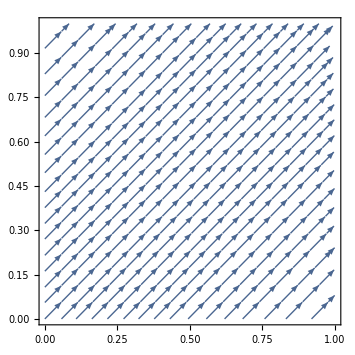

```mathematica
StreamPlot[{H1E1d,H1E1d}/.Unstableparams/.{h1e2-> 0.2,s1e2-> 0.2},{h1e1,0,1},{s1e1,0,1}]
```

So visually, it looks like there’s some sort of stable region. It could be a line, it could be a single point.

```mathematica
Sysunstable={H1E1d,H1E2d,S1E1d,S1E2d}/.Unstableparams;
ans=NSolve[Sysunstable==0,{h1e1,h1e2,s1e1,s1e2},PositiveReals]//Chop;
(**)
equilibrialist2={};
Do[ If[ ans[[i,1,2]]≤ 1&&ans[[i,2,2]]≤ 1&&ans[[i,3,2]]≤ 1&&ans[[i,4,2]]≤ 1, AppendTo[equilibrialist2,ans[[i]]]],{i,1,Length[ans]}]
equilibrialist2
```

{{h1e1→1.,h1e2→1.,s1e1→0.990012,s1e2→0.0012375},{h1e1→1.,h1e2→1.,s1e1→1.,s1e2→1.},{h1e1→0.990699,h1e2→0.00930061,s1e1→0.990699,s1e2→0.00930061},{h1e1→0.990012,h1e2→0.0012375,s1e1→1.,s1e2→1.}}

So there are a few equilibria. Let’s check their stability:

```mathematica
StableEq={};
Do[{Eigval=J/.Unstableparams/.equilibrialist2[[i]]//Eigenvalues;
If[Eigval[[1]]<0&&Eigval[[2]]<0&&Eigval[[3]]<0&&Eigval[[4]]<0, AppendTo[StableEq,{equilibrialist2[[i]],Eigval}]]},{i,1,Length[equilibrialist2]}]
StableEq
```

{{{h1e1→0.990699,h1e2→0.00930061,s1e1→0.990699,s1e2→0.00930061},{-0.112979,-0.110979,-0.100079,-0.0980793}}}

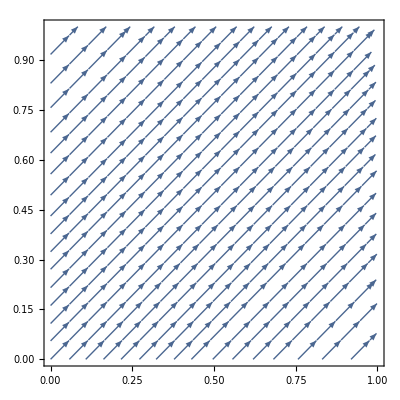

```mathematica
StreamPlot[{H1E1d,H1E1d}/.Unstableparams/.StableEq[[1,1,4]]/.StableEq[[1,1,2]],{h1e1,0,1},{s1e1,0,1}]
```

So we know that all else being unstable, we can have a stable internal equilibrium.

## Approximations:

### Itty bitty dispersal approximation of equilibria to the first order:

First, we’ll approximate the equilibria:

```mathematica
(*Try defining each variable as a taylor series and give it a go!!*)
 assumptionfn[x_] := x/.{d-> d*ϵ,h1e1->h1e10+ h1e11*ϵ,h1e2-> h1e20+h1e21*ϵ,s1e1->s1e10+s1e11* ϵ, s1e2->s1e20+s1e21* ϵ};
{H1E1d,H1E2d,S1E1d,S1E2d}//assumptionfn//Factor;
Series[%,{ϵ,0,0}]//Normal(*0th Order Approximation*);
ans=Solve[%==0,{h1e10,h1e20,s1e10,s1e20}]
```

{{h1e10→(Sg-Ss)/(Sg-Sh+SM-Ss),h1e20→0,s1e10→(Hg-Hh)/(Hg-Hh+HM-Hs),s1e20→0},{h1e10→(Sg-Ss)/(Sg-Sh+SM-Ss),h1e20→1,s1e10→(Hg-Hh)/(Hg-Hh+HM-Hs),s1e20→0},{h1e10→(Sg-Ss)/(Sg-Sh+SM-Ss),h1e20→0,s1e10→(Hg-Hh)/(Hg-Hh+HM-Hs),s1e20→1},{h1e10→(Sg-Ss)/(Sg-Sh+SM-Ss),h1e20→1,s1e10→(Hg-Hh)/(Hg-Hh+HM-Hs),s1e20→1},{h1e10→(Sg-Ss)/(Sg-Sh+SM-Ss),h1e20→(Sh-SM)/(-Sg+Sh-SM+Ss),s1e10→(Hg-Hh)/(Hg-Hh+HM-Hs),s1e20→(HM-Hs)/(Hg-Hh+HM-Hs)},{h1e10→0,h1e20→(Sh-SM)/(-Sg+Sh-SM+Ss),s1e10→0,s1e20→(HM-Hs)/(Hg-Hh+HM-Hs)},{h1e10→1,h1e20→(Sh-SM)/(-Sg+Sh-SM+Ss),s1e10→0,s1e20→(HM-Hs)/(Hg-Hh+HM-Hs)},{h1e10→0,h1e20→(Sh-SM)/(-Sg+Sh-SM+Ss),s1e10→1,s1e20→(HM-Hs)/(Hg-Hh+HM-Hs)},{h1e10→1,h1e20→(Sh-SM)/(-Sg+Sh-SM+Ss),s1e10→1,s1e20→(HM-Hs)/(Hg-Hh+HM-Hs)},{h1e10→0,h1e20→0,s1e10→0,s1e20→0},{h1e10→1,h1e20→0,s1e10→0,s1e20→0},{h1e10→0,h1e20→1,s1e10→0,s1e20→0},{h1e10→1,h1e20→1,s1e10→0,s1e20→0},{h1e10→0,h1e20→0,s1e10→1,s1e20→0},{h1e10→1,h1e20→0,s1e10→1,s1e20→0},{h1e10→0,h1e20→1,s1e10→1,s1e20→0},{h1e10→1,h1e20→1,s1e10→1,s1e20→0},{h1e10→0,h1e20→0,s1e10→0,s1e20→1},{h1e10→1,h1e20→0,s1e10→0,s1e20→1},{h1e10→0,h1e20→1,s1e10→0,s1e20→1},{h1e10→1,h1e20→1,s1e10→0,s1e20→1},{h1e10→0,h1e20→0,s1e10→1,s1e20→1},{h1e10→1,h1e20→0,s1e10→1,s1e20→1},{h1e10→0,h1e20→1,s1e10→1,s1e20→1},{h1e10→1,h1e20→1,s1e10→1,s1e20→1}}

Our 0th order equilibria are the same as those for the no dispersal case. 
Next,  we’ll plug those 0 order cases into the 0 and first order expansion, and then solve for the first order terms. 
I’ll sum the 0 order and first order terms and store them in the ApproximatedEq object.

```mathematica
ApproximatedEq={};
Do[{sys={H1E1d,H1E2d,S1E1d,S1E2d}//assumptionfn//Factor;
exp=Series[sys,{ϵ,0,1}]//Normal(*First Order Approximation*);
eval=exp/.ans[[i]]//Factor;
firstorder=Solve[eval==0,{h1e11,h1e21,s1e11,s1e21}]//Factor;
approximated={};
Do[eqi=ans[[ i,j,2]]+firstorder[[1,j,2]];
AppendTo[approximated,eqi],{j,1,4}];
AppendTo[ApproximatedEq,approximated]},{i,1,Length[ans]}]


ApproximatedEq//FullSimplify
```

{{(d (Hg-Hh+HM-Hs)+(HM-Hs) (Sg-Ss))/((HM-Hs) (Sg-Sh+SM-Ss)),(d (Sg-Ss))/((HM-Hs) (Sg-Sh+SM-Ss)),((Hg-Hh) (Sh-SM)+d (-Sg+Sh-SM+Ss))/((Hg-Hh+HM-Hs) (Sh-SM)),(d (-Hg+Hh))/((Hg-Hh+HM-Hs) (Sh-SM))},{(d (Hg-Hh+HM-Hs)+(HM-Hs) (Sg-Ss))/((HM-Hs) (Sg-Sh+SM-Ss)),1+(d (-Sh+SM))/((HM-Hs) (Sg-Sh+SM-Ss)),((Hg-Hh) (Sg-Ss)+d (-Sg+Sh-SM+Ss))/((Hg-Hh+HM-Hs) (Sg-Ss)),(d (-Hg+Hh))/((Hg-Hh+HM-Hs) (Sg-Ss))},{(d (-Hg+Hh-HM+Hs)+(Hg-Hh) (Sg-Ss))/((Hg-Hh) (Sg-Sh+SM-Ss)),(d (-Sg+Ss))/((Hg-Hh) (Sg-Sh+SM-Ss)),((Hg-Hh) (Sh-SM)+d (-Sg+Sh-SM+Ss))/((Hg-Hh+HM-Hs) (Sh-SM)),1+(d (-HM+Hs))/((Hg-Hh+HM-Hs) (Sh-SM))},{(d (-Hg+Hh-HM+Hs)+(Hg-Hh) (Sg-Ss))/((Hg-Hh) (Sg-Sh+SM-Ss)),1+(d (Sh-SM))/((Hg-Hh) (Sg-Sh+SM-Ss)),((Hg-Hh) (Sg-Ss)+d (-Sg+Sh-SM+Ss))/((Hg-Hh+HM-Hs) (Sg-Ss)),1+(d (-HM+Hs))/((Hg-Hh+HM-Hs) (Sg-Ss))},{((d (Hg-Hh+HM-Hs) (Hg-Hh-HM+Hs))/((Hg-Hh) (HM-Hs))+Sg-Ss)/(Sg-Sh+SM-Ss),(-(d (Hg-Hh+HM-Hs) (Hg-Hh-HM+Hs))/((Hg-Hh) (HM-Hs))-Sh+SM)/(Sg-Sh+SM-Ss),(Hg-Hh+(d (Sg+Sh-SM-Ss) (-Sg+Sh-SM+Ss))/((Sh-SM) (Sg-Ss)))/(Hg-Hh+HM-Hs),(HM-Hs+(d (Sg+Sh-SM-Ss) (Sg-Sh+SM-Ss))/((Sh-SM) (Sg-Ss)))/(Hg-Hh+HM-Hs)},{(d (Sh-SM))/((Hg-Hh) (-Sg+Sh-SM+Ss)),(d (Hg-Hh+HM-Hs)-(Hg-Hh) (Sh-SM))/((Hg-Hh) (Sg-Sh+SM-Ss)),(d (HM-Hs))/((Hg-Hh+HM-Hs) (Sg-Ss)),((HM-Hs) (Sg-Ss)+d (Sg-Sh+SM-Ss))/((Hg-Hh+HM-Hs) (Sg-Ss))},{1+(d (Sg-Ss))/((Hg-Hh) (Sg-Sh+SM-Ss)),(d (Hg-Hh+HM-Hs)-(Hg-Hh) (Sh-SM))/((Hg-Hh) (Sg-Sh+SM-Ss)),(d (HM-Hs))/((Hg-Hh+HM-Hs) (Sh-SM)),((HM-Hs) (Sh-SM)+d (Sg-Sh+SM-Ss))/((Hg-Hh+HM-Hs) (Sh-SM))},{(d (Sh-SM))/((HM-Hs) (Sg-Sh+SM-Ss)),(d (-Hg+Hh-HM+Hs)-(HM-Hs) (Sh-SM))/((HM-Hs) (Sg-Sh+SM-Ss)),1+(d (Hg-Hh))/((Hg-Hh+HM-Hs) (Sg-Ss)),((HM-Hs) (Sg-Ss)+d (Sg-Sh+SM-Ss))/((Hg-Hh+HM-Hs) (Sg-Ss))},{1+(d (-Sg+Ss))/((HM-Hs) (Sg-Sh+SM-Ss)),(d (-Hg+Hh-HM+Hs)-(HM-Hs) (Sh-SM))/((HM-Hs) (Sg-Sh+SM-Ss)),1+(d (Hg-Hh))/((Hg-Hh+HM-Hs) (Sh-SM)),((HM-Hs) (Sh-SM)+d (Sg-Sh+SM-Ss))/((Hg-Hh+HM-Hs) (Sh-SM))},{0,0,0,0},{1+d/(Hg-Hh),d/(HM-Hs),0,0},{d/(Hg-Hh),1+d/(HM-Hs),0,0},{1,1,0,0},{0,0,1+d/(Sg-Ss),d/(-Sh+SM)},{1+d/(-HM+Hs),d/(HM-Hs),1+d/(Sh-SM),d/(-Sh+SM)},{d/(-HM+Hs),1+d/(HM-Hs),1+d/(Sg-Ss),d/(-Sg+Ss)},{1,1,1+d/(Sh-SM),d/(-Sg+Ss)},{0,0,d/(Sg-Ss),1+d/(-Sh+SM)},{1+d/(Hg-Hh),d/(-Hg+Hh),d/(Sh-SM),1+d/(-Sh+SM)},{d/(Hg-Hh),1+d/(-Hg+Hh),d/(Sg-Ss),1+d/(-Sg+Ss)},{1,1,d/(Sh-SM),1+d/(-Sg+Ss)},{0,0,1,1},{1+d/(-HM+Hs),d/(-Hg+Hh),1,1},{d/(-HM+Hs),1+d/(-Hg+Hh),1,1},{1,1,1,1}}

all in form: (h1e1,h1e2,s1e1,s1e2): Numerical case to check which equilibria might actually fit our constraints:

```mathematica
(*filter out candidates less than 0 and greater than 1*)
Filterfxn[x_]:= {filterlist={};
Do[ If[  0≤  x[[i,1]]≤  1&&0≤  x[[i,2]]≤  1&&0≤  x[[i,3]]≤  1&&0≤  x[[i,4]]≤ 1, AppendTo[filterlist,{{i},x[[i]]}]],{i,1,Length[x]}];
filterlist}
```

```mathematica
ApproximatedEq/.Unstableparams//Filterfxn
```

{{{{10},{0,0,0,0}},{{11},{0.99875,0.01,0,0}},{{13},{1,1,0,0}},{{14},{0,0,0.99875,0.01}},{{15},{0.99,0.01,0.99,0.01}},{{17},{1,1,0.99,0.00125}},{{22},{0,0,1,1}},{{23},{0.99,0.00125,1,1}},{{25},{1,1,1,1}}}}

#### Stability of approximate equilibria:

Here, I’ll pick out the equilirium I think is most likely to be stable, and approximate its stability criterion:

```mathematica
JC = J/.{h1e1->1+d/(-HM+Hs),h1e2-> d/(HM-Hs),s1e1-> 1+d/(Sh-SM),s1e2->d/(-Sh+SM)}/.d-> d*ϵ;
(*Evaluate the Jacobian at the equilirium of interest and apply our assumption that dispersal is itty bitty. Note that the change of variables doesn't matter so much here since we have values for the frequencies from our earlier approximation. All we're really doing here is d -> d*ϵ. *)
charpoly=CharacteristicPolynomial[JC,λ];
charpolyexp=charpoly/.{λ-> λ0+λ1*ϵ};
(*First we set ϵ = 0 and solve our characteristic polynomial for our eigenvalues. This gives an approximation of the eigenvalues to the 0th order, with our small parameter (d) equal to 0: *)
b=Series[charpolyexp,{ϵ,0,0}]//Normal;
Othorderλs=Solve[b==0,λ0]
(*These are the 0th order values of λ. We don't really need to go to higher orders because they're all negative! Hooray! None of them are on the border between stability and instability. But let's go higher as an exercise. *)
a=Series[charpolyexp,{ϵ,0,1}]//Normal ;
firstorders={};
Do[AppendTo[firstorders,a/.Othorderλs[[i]]],{i,1,4}]
(* Here, I'm solving the first order taylor series expansion, using each of the λ0 terms I found earlier. *)
firstorders
Othorderλs[[1;;4,1,2]]
(* this expression is analagous to 8.49 in Otto and Day pp. 336. Also see the univariate details for this procedure on 183 and 184. 
The first order terms are all 0. *)
```

{{λ0→-HM+Hs},{λ0→-HM+Hs},{λ0→Sh-SM},{λ0→Sh-SM}}

{0,0,0,0}

{-HM+Hs,-HM+Hs,Sh-SM,Sh-SM}

So this internal equilibrium should ALWAYS be stable. Its stability criteria depend solely on the payoffs rather than the rate of dispersal. 
Now let’s check our methodology using an equilibrium we can solve analytically:

```mathematica
JC = J/.{h1e1->1,h1e2-> 1,s1e1-> 1,s1e2->1}/.d->d ϵ;
charpoly=CharacteristicPolynomial[JC,λ];
charpolyexp=charpoly/.{λ-> λ0+λ1*ϵ};
b=Series[charpolyexp,{ϵ,0,0}]//Normal;
Othorderλs=Solve[b==0,λ0]
(* Now we need to go to higher orders since our 0th order terms can potentially be on the border between stability and instability depending on our payoffs. See first output.  *)
a=Series[charpolyexp,{ϵ,0,1}]//Normal ;
firstordersp={};
Do[fun=a/.Othorderλs[[i]];
AppendTo[firstordersp,Solve[fun==0,λ1]],{i,1,4}];
firstorders= firstordersp//Flatten;
(*The total approximated eigenvalues are: *)
approximatedeigval=Othorderλs[[1;;4,1,2]]+firstorders[[1;;4,2]]
(*So it looks like all the higher order terms go to negative d! Slightly higher values of dispersal make this equilibrium stable. This tracks from our exact stability analysis.   *)
%/.Unstableparams
lessgoodparams={HM->1,Hh->0.9,Hs->0.9,Hg->0.1,SM->1,Ss->0.9,Sh->0.9,Sg->0.1,d->0.1};
%%%/.lessgoodparams
```

{{λ0→-Hg+Hh},{λ0→-HM+Hs},{λ0→Sh-SM},{λ0→-Sg+Ss}}

{-d-Hg+Hh,-d-HM+Hs,-d+Sh-SM,-d-Sg+Ss}

{0.799,-0.101,-0.101,0.799}

{0.7,-0.2,-0.2,0.7}

```mathematica
J/.{h1e1->1,h1e2-> 1,s1e1-> 1,s1e2->1}//Eigenvalues//FullSimplify
J/.{h1e1->1,h1e2-> 1,s1e1-> 1,s1e2->1};
CharacteristicPolynomial[%,λ];
Solve[%==0,λ]
%/.Unstableparams
%%/.lessgoodparams
```

{1/2 (-2 d-Hg+Hh-HM+Hs-√(4 d^2+(Hg-Hh-HM+Hs)^2)),1/2 (-2 d-Hg+Hh-HM+Hs+√(4 d^2+(Hg-Hh-HM+Hs)^2)),1/2 (-2 d-Sg+Sh-SM-√(4 d^2+(Sg+Sh-SM-Ss)^2)+Ss),1/2 (-2 d-Sg+Sh-SM+√(4 d^2+(Sg+Sh-SM-Ss)^2)+Ss)}

{{λ→1/2 (-2 d-Hg+Hh-HM+Hs-√(4 d^2+Hg^2-2 Hg Hh+Hh^2-2 Hg HM+2 Hh HM+HM^2+2 Hg Hs-2 Hh Hs-2 HM Hs+Hs^2))},{λ→1/2 (-2 d-Hg+Hh-HM+Hs+√(4 d^2+Hg^2-2 Hg Hh+Hh^2-2 Hg HM+2 Hh HM+HM^2+2 Hg Hs-2 Hh Hs-2 HM Hs+Hs^2))},{λ→1/2 (-2 d-Sg+Sh-SM+Ss-√(4 d^2+Sg^2+2 Sg Sh+Sh^2-2 Sg SM-2 Sh SM+SM^2-2 Sg Ss-2 Sh Ss+2 SM Ss+Ss^2))},{λ→1/2 (-2 d-Sg+Sh-SM+Ss+√(4 d^2+Sg^2+2 Sg Sh+Sh^2-2 Sg SM-2 Sh SM+SM^2-2 Sg Ss-2 Sh Ss+2 SM Ss+Ss^2))}}

{{λ→-0.101001},{λ→0.799001},{λ→-0.101001},{λ→0.799001}}

{{λ→-0.210977},{λ→0.710977},{λ→-0.210977},{λ→0.710977}}

This approximation is pretty darn good approximation for teeny tiny dispersal!! It’s even good enough for a rate of dispersal that’s of the same order to the parameters! Neat!

Now, let’s do a slog through all those equiliria and see if we can tease something from them. I’ll start by checking the 0th order case, and seeing which equilibria I can categorically exclude.

```mathematica
ApproximatedEq;
```

```mathematica
Othorderterms=Table[{JC = J/.{h1e1->ApproximatedEq[[i,1]],h1e2-> ApproximatedEq[[i,2]],s1e1-> ApproximatedEq[[i,3]],s1e2->ApproximatedEq[[i,4]]}/.d->d ϵ;
charpoly=CharacteristicPolynomial[JC,λ];
charpolyexp=charpoly/.{λ-> λ0+λ1*ϵ};
b=Series[charpolyexp,{ϵ,0,0}]//Normal;
Othorderλs=Solve[b==0,λ0][[All,1,2]]//Factor,i}
,{i,1,Length[ApproximatedEq]}]
```

{{{-HM+Hs,Sh-SM,-(ⅈ √(Hg-Hh) √(HM-Hs) √(Sh-SM) √(Sg-Ss))/(√((Hg-Hh+HM-Hs) (Sg-Sh+SM-Ss))),(ⅈ √(Hg-Hh) √(HM-Hs) √(Sh-SM) √(Sg-Ss))/(√((Hg-Hh+HM-Hs) (Sg-Sh+SM-Ss)))},1},{{HM-Hs,Sg-Ss,-(ⅈ √(Hg-Hh) √(HM-Hs) √(Sh-SM) √(Sg-Ss))/(√((Hg-Hh+HM-Hs) (Sg-Sh+SM-Ss))),(ⅈ √(Hg-Hh) √(HM-Hs) √(Sh-SM) √(Sg-Ss))/(√((Hg-Hh+HM-Hs) (Sg-Sh+SM-Ss)))},2},{{Hg-Hh,-Sh+SM,-(ⅈ √(Hg-Hh) √(HM-Hs) √(Sh-SM) √(Sg-Ss))/(√((Hg-Hh+HM-Hs) (Sg-Sh+SM-Ss))),(ⅈ √(Hg-Hh) √(HM-Hs) √(Sh-SM) √(Sg-Ss))/(√((Hg-Hh+HM-Hs) (Sg-Sh+SM-Ss)))},3},{{-Hg+Hh,-Sg+Ss,-(ⅈ √(Hg-Hh) √(HM-Hs) √(Sh-SM) √(Sg-Ss))/(√((Hg-Hh+HM-Hs) (Sg-Sh+SM-Ss))),(ⅈ √(Hg-Hh) √(HM-Hs) √(Sh-SM) √(Sg-Ss))/(√((Hg-Hh+HM-Hs) (Sg-Sh+SM-Ss)))},4},{{-(ⅈ √(Hg-Hh) √(HM-Hs) √(Sh-SM) √(Sg-Ss))/(√((Hg-Hh+HM-Hs) (Sg-Sh+SM-Ss))),-(ⅈ √(Hg-Hh) √(HM-Hs) √(Sh-SM) √(Sg-Ss))/(√((Hg-Hh+HM-Hs) (Sg-Sh+SM-Ss))),(ⅈ √(Hg-Hh) √(HM-Hs) √(Sh-SM) √(Sg-Ss))/(√((Hg-Hh+HM-Hs) (Sg-Sh+SM-Ss))),(ⅈ √(Hg-Hh) √(HM-Hs) √(Sh-SM) √(Sg-Ss))/(√((Hg-Hh+HM-Hs) (Sg-Sh+SM-Ss)))},5},{{-Hg+Hh,-Sg+Ss,-(ⅈ √(Hg-Hh) √(HM-Hs) √(Sh-SM) √(Sg-Ss))/(√((Hg-Hh+HM-Hs) (Sg-Sh+SM-Ss))),(ⅈ √(Hg-Hh) √(HM-Hs) √(Sh-SM) √(Sg-Ss))/(√((Hg-Hh+HM-Hs) (Sg-Sh+SM-Ss)))},6},{{Hg-Hh,-Sh+SM,-(ⅈ √(Hg-Hh) √(HM-Hs) √(Sh-SM) √(Sg-Ss))/(√((Hg-Hh+HM-Hs) (Sg-Sh+SM-Ss))),(ⅈ √(Hg-Hh) √(HM-Hs) √(Sh-SM) √(Sg-Ss))/(√((Hg-Hh+HM-Hs) (Sg-Sh+SM-Ss)))},7},{{HM-Hs,Sg-Ss,-(ⅈ √(Hg-Hh) √(HM-Hs) √(Sh-SM) √(Sg-Ss))/(√((Hg-Hh+HM-Hs) (Sg-Sh+SM-Ss))),(ⅈ √(Hg-Hh) √(HM-Hs) √(Sh-SM) √(Sg-Ss))/(√((Hg-Hh+HM-Hs) (Sg-Sh+SM-Ss)))},8},{{-HM+Hs,Sh-SM,-(ⅈ √(Hg-Hh) √(HM-Hs) √(Sh-SM) √(Sg-Ss))/(√((Hg-Hh+HM-Hs) (Sg-Sh+SM-Ss))),(ⅈ √(Hg-Hh) √(HM-Hs) √(Sh-SM) √(Sg-Ss))/(√((Hg-Hh+HM-Hs) (Sg-Sh+SM-Ss)))},9},{{-Hg+Hh,-HM+Hs,Sh-SM,-Sg+Ss},10},{{Hg-Hh,-HM+Hs,Sh-SM,-Sh+SM},11},{{-Hg+Hh,HM-Hs,Sg-Ss,-Sg+Ss},12},{{Hg-Hh,HM-Hs,-Sh+SM,Sg-Ss},13},{{HM-Hs,-HM+Hs,Sh-SM,Sg-Ss},14},{{-HM+Hs,-HM+Hs,Sh-SM,Sh-SM},15},{{HM-Hs,HM-Hs,Sg-Ss,Sg-Ss},16},{{HM-Hs,-HM+Hs,Sh-SM,Sg-Ss},17},{{Hg-Hh,-Hg+Hh,-Sh+SM,-Sg+Ss},18},{{Hg-Hh,Hg-Hh,-Sh+SM,-Sh+SM},19},{{-Hg+Hh,-Hg+Hh,-Sg+Ss,-Sg+Ss},20},{{Hg-Hh,-Hg+Hh,-Sh+SM,-Sg+Ss},21},{{Hg-Hh,HM-Hs,-Sh+SM,Sg-Ss},22},{{Hg-Hh,-HM+Hs,Sh-SM,-Sh+SM},23},{{-Hg+Hh,HM-Hs,Sg-Ss,-Sg+Ss},24},{{-Hg+Hh,-HM+Hs,Sh-SM,-Sg+Ss},25}}

So we can throw out some of the equilibria based on the 0th order terms! Terms 2,3, 7,8,11,12,13,14,16,17,18,19,21,22,23, and 24 are not near the border between stability and instability. Their 0th order eigenvalue approximations involve the difference between a positive Matching payoff (SM or HM) and a negative mismatched payoff. They will always be positive and unstable for small d.  

We can also throw out even more terms! But there are instances where this will be on the border between stability and instability if any one set of the mismatched payoffs are equal. 

Let’s select the instances whose stability remains unknown:

```mathematica
unstables={2,3,7,8,11,12,13,14,16,17,18,19,21,22,23,24};(*List of equilibria that must be unstable. *)
filteredeq={};
Do[If[ContainsAny[{i},unstables]==False,AppendTo[filteredeq,ApproximatedEq[[i]]]],{i,1,Length[ApproximatedEq]}]
filteredeq
```

{{(d (Hg-Hh+HM-Hs))/((HM-Hs) (Sg-Sh+SM-Ss))+(Sg-Ss)/(Sg-Sh+SM-Ss),(d (Sg-Ss))/((HM-Hs) (Sg-Sh+SM-Ss)),(Hg-Hh)/(Hg-Hh+HM-Hs)+(d (-Sg+Sh-SM+Ss))/((Hg-Hh+HM-Hs) (Sh-SM)),-(d (Hg-Hh))/((Hg-Hh+HM-Hs) (Sh-SM))},{-(d (Hg-Hh+HM-Hs))/((Hg-Hh) (Sg-Sh+SM-Ss))+(Sg-Ss)/(Sg-Sh+SM-Ss),1-(d (Sh-SM))/((Hg-Hh) (-Sg+Sh-SM+Ss)),(Hg-Hh)/(Hg-Hh+HM-Hs)-(d (Sg-Sh+SM-Ss))/((Hg-Hh+HM-Hs) (Sg-Ss)),1-(d (HM-Hs))/((Hg-Hh+HM-Hs) (Sg-Ss))},{(d (Hg-Hh+HM-Hs) (Hg-Hh-HM+Hs))/((Hg-Hh) (HM-Hs) (Sg-Sh+SM-Ss))+(Sg-Ss)/(Sg-Sh+SM-Ss),-(d (Hg-Hh+HM-Hs) (Hg-Hh-HM+Hs))/((Hg-Hh) (HM-Hs) (Sg-Sh+SM-Ss))+(Sh-SM)/(-Sg+Sh-SM+Ss),(Hg-Hh)/(Hg-Hh+HM-Hs)-(d (Sg+Sh-SM-Ss) (Sg-Sh+SM-Ss))/((Hg-Hh+HM-Hs) (Sh-SM) (Sg-Ss)),(HM-Hs)/(Hg-Hh+HM-Hs)+(d (Sg+Sh-SM-Ss) (Sg-Sh+SM-Ss))/((Hg-Hh+HM-Hs) (Sh-SM) (Sg-Ss))},{(d (Sh-SM))/((Hg-Hh) (-Sg+Sh-SM+Ss)),(d (Hg-Hh+HM-Hs))/((Hg-Hh) (Sg-Sh+SM-Ss))+(Sh-SM)/(-Sg+Sh-SM+Ss),(d (HM-Hs))/((Hg-Hh+HM-Hs) (Sg-Ss)),(HM-Hs)/(Hg-Hh+HM-Hs)+(d (Sg-Sh+SM-Ss))/((Hg-Hh+HM-Hs) (Sg-Ss))},{1-(d (Sg-Ss))/((HM-Hs) (Sg-Sh+SM-Ss)),-(d (Hg-Hh+HM-Hs))/((HM-Hs) (Sg-Sh+SM-Ss))+(Sh-SM)/(-Sg+Sh-SM+Ss),1+(d (Hg-Hh))/((Hg-Hh+HM-Hs) (Sh-SM)),(HM-Hs)/(Hg-Hh+HM-Hs)-(d (-Sg+Sh-SM+Ss))/((Hg-Hh+HM-Hs) (Sh-SM))},{0,0,0,0},{1-d/(HM-Hs),d/(HM-Hs),1+d/(Sh-SM),-d/(Sh-SM)},{d/(Hg-Hh),1-d/(Hg-Hh),d/(Sg-Ss),1-d/(Sg-Ss)},{1,1,1,1}}

### Stability of candidate equilibria:

#### First internal equilibrium: Unstable, nonexistent, or neutral when Hg = Hh and/or Sg=Ss

That’s only 9 measly equilibria. I can handle that! Let’s find the next order term for each of these instances. I’ll start with the first:

```mathematica
(*I'm tired of having big chunks of code! Let's make a function for approximating an equilibrium and finding its stability to first order:  *)
```

```mathematica
StabilityofEQ[EQ_]:={
Print[{"Equilibrium = ",EQ}],
EQ;
JC = J/.{h1e1->EQ[[1]],h1e2-> EQ[[2]],s1e1-> EQ[[3]],s1e2->EQ[[4]]}/.d->d ϵ;
charpoly=CharacteristicPolynomial[JC,λ];
charpolyexp=charpoly/.{λ-> λ0+λ1*ϵ};
b=Series[charpolyexp,{ϵ,0,0}]//Normal;
Othorderλs=Solve[b==0,λ0]//Factor;
a=Series[charpolyexp,{ϵ,0,1}]//Normal ;
firstsp=Table[{
λ11=a/.Othorderλs[[i]];
Solve[λ11==0,λ1]//Chop//Factor},{i,1,4}];
firsts=firstsp//Flatten;
approximatedeigval=Othorderλs[[1;;4,1,2]]+firsts[[1;;4,2]]//Factor;
Print[{"0th Order Eigval Approximations = ",Othorderλs}]
(*Print[{"1st Order Eigval Approximations = ",firsts//Factor}]*)}
```

```mathematica
StabilityofEQ[ filteredeq[[1]] ];
```

{Equilibrium = ,{(d (Hg-Hh+HM-Hs))/((HM-Hs) (Sg-Sh+SM-Ss))+(Sg-Ss)/(Sg-Sh+SM-Ss),(d (Sg-Ss))/((HM-Hs) (Sg-Sh+SM-Ss)),(Hg-Hh)/(Hg-Hh+HM-Hs)+(d (-Sg+Sh-SM+Ss))/((Hg-Hh+HM-Hs) (Sh-SM)),-(d (Hg-Hh))/((Hg-Hh+HM-Hs) (Sh-SM))}}

{0th Order Eigval Approximations = ,{{λ0→-HM+Hs},{λ0→Sh-SM},{λ0→-(ⅈ √(Hg-Hh) √(HM-Hs) √(Sh-SM) √(Sg-Ss))/(√((Hg-Hh+HM-Hs) (Sg-Sh+SM-Ss)))},{λ0→(ⅈ √(Hg-Hh) √(HM-Hs) √(Sh-SM) √(Sg-Ss))/(√((Hg-Hh+HM-Hs) (Sg-Sh+SM-Ss)))}}}

Let’s use a change of variables to shrink this down!

```mathematica
(*Reduce equilibrium from 8 variables to 4: ΔH1 = HM - Hs, ΔH2 = Hg - Hh, ΔS1 = SM - Sh, ΔS2 = Sg - Sh *)
StabilityofEQCOV[EQ_,ΔH1ex_,ΔH2ex_,ΔS1ex_,ΔS2ex_]:={filteredeq[[1]];
changeOfVariables=First@Solve[{ ΔH1==ΔH1ex,ΔH2==ΔH2ex,ΔS1==ΔS1ex,ΔS2==ΔS2ex},{HM,Hs,Hg,Hh,SM,Sh,Sg,Ss}],
eqcov=EQ/.changeOfVariables//Factor//FullSimplify,
JN=J/.changeOfVariables//Simplify;
JC = JN/.{h1e1->eqcov[[1]],h1e2-> eqcov[[2]],s1e1-> eqcov[[3]],s1e2->eqcov[[4]]}/.d->d ϵ;
charpoly=CharacteristicPolynomial[JC,λ];
charpolyexp=charpoly/.{λ-> λ0+λ1*ϵ};
b=Series[charpolyexp,{ϵ,0,0}]//Normal;
Othorderλs=Solve[b==0,λ0]//Factor,
a=Series[charpolyexp,{ϵ,0,1}]//Normal ;
firstsp=Table[{
λ11=a/.Othorderλs[[i]];
Solve[λ11==0,λ1]//Chop//Factor},{i,1,4}];
firsts=firstsp//Flatten;
approximatedeigval=Othorderλs[[1;;4,1,2]]+firsts[[1;;4,2]]//Factor;
firsts//Factor//FullSimplify}
```

```mathematica
StabilityofEQCOV[filteredeq[[1]],HM-Hs,Hg-Hh,SM-Sh,Sg-Ss]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Hs→HM-ΔH1,Hh→Hg-ΔH2,Sh→SM-ΔS1,Ss→Sg-ΔS2},{(d (ΔH1+ΔH2)+ΔH1 ΔS2)/(ΔH1 (ΔS1+ΔS2)),(d ΔS2)/(ΔH1 (ΔS1+ΔS2)),(ΔH2 ΔS1+d (ΔS1+ΔS2))/((ΔH1+ΔH2) ΔS1),(d ΔH2)/((ΔH1+ΔH2) ΔS1)},{{λ0→-ΔH1},{λ0→-ΔS1},{λ0→-(√ΔH1 √ΔH2 √ΔS1 √ΔS2)/(√((ΔH1+ΔH2) (ΔS1+ΔS2)))},{λ0→(√ΔH1 √ΔH2 √ΔS1 √ΔS2)/(√((ΔH1+ΔH2) (ΔS1+ΔS2)))}},{λ1→d (1+ΔH2/ΔS1-(2 ΔS1)/(ΔS1+ΔS2)),λ1→d (1-(2 ΔH1)/(ΔH1+ΔH2)+ΔS2/ΔH1),λ1→-((d (ΔH2^(5/2) ΔS1 √ΔS2 (ΔS1+ΔS2)+ΔH1^2 √ΔH2 ΔS2^(3/2) (ΔS1+ΔS2)+ΔH1 ΔH2^(3/2) √ΔS2 (ΔS1+ΔS2)^2+√ΔH1 ΔH2 √ΔS1 √((ΔH1+ΔH2) (ΔS1+ΔS2)) (ΔH2 (ΔS1-ΔS2)-ΔS2 (ΔS1+ΔS2))+ΔH1^(3/2) √ΔS1 √((ΔH1+ΔH2) (ΔS1+ΔS2)) (ΔH2 (ΔS1-ΔS2)+ΔS2 (ΔS1+ΔS2))))/(2 ΔH1 √ΔH2 (ΔH1+ΔH2) ΔS1 √ΔS2 (ΔS1+ΔS2))),λ1→-((d (ΔH2^(5/2) ΔS1 √ΔS2 (ΔS1+ΔS2)+ΔH1^2 √ΔH2 ΔS2^(3/2) (ΔS1+ΔS2)+ΔH1 ΔH2^(3/2) √ΔS2 (ΔS1+ΔS2)^2-ΔH1^(3/2) √ΔS1 √((ΔH1+ΔH2) (ΔS1+ΔS2)) (ΔH2 (ΔS1-ΔS2)+ΔS2 (ΔS1+ΔS2))+√ΔH1 ΔH2 √ΔS1 √((ΔH1+ΔH2) (ΔS1+ΔS2)) (ΔH2 (-ΔS1+ΔS2)+ΔS2 (ΔS1+ΔS2))))/(2 ΔH1 √ΔH2 (ΔH1+ΔH2) ΔS1 √ΔS2 (ΔS1+ΔS2)))}}

The third and fourth 0th order eigenvalue approximations can be re-written in terms of the second and fourth equilibria!

```mathematica
Othorderλs[[3;;4]]
```

{{λ0→-(√ΔH1 √ΔH2 √ΔS1 √ΔS2)/(√((ΔH1+ΔH2) (ΔS1+ΔS2)))},{λ0→(√ΔH1 √ΔH2 √ΔS1 √ΔS2)/(√((ΔH1+ΔH2) (ΔS1+ΔS2)))}}

λ0=±√((h1e2 ΔH1 ΔH1 s1e2 ΔS1  ΔS1)/(d d)=)±(ΔH1 ΔS1)/d √(h1e2 s1e2)

Therefore, if the equilibrium exists it will ALWAYS be unstable (unless any of the Δ terms =0) which I’ll ignore for now.

```mathematica
(*Reduce equilibrium from 8 variables to 4: ΔH1 = HM - Hs, ΔH2 = Hg - Hh, ΔS1 = SM - Sh, ΔS2 = Sg - Sh *)
filteredeq[[1]];
changeOfVariables=First@Solve[{ ΔH1==HM-Hs,ΔH2==Hg-Hh,ΔS1==SM-Sh,Sg-Ss== ΔS2},{HM,Hs,Hg,Hh,SM,Sh,Sg,Ss}]
Print["Equilibrium: "]
equilibrium=filteredeq[[1]]/.changeOfVariables/.ΔS2-> 0//Simplify
J/.changeOfVariables/.ΔS2-> 0//Simplify//MatrixForm
JC = %/.{h1e1->%%[[1]],h1e2-> %%[[2]],s1e1-> %%[[3]],s1e2->%%[[4]]}/.d->d ϵ;
charpoly=CharacteristicPolynomial[JC,λ];
charpolyexp=charpoly/.{λ-> λ0+λ1*ϵ};
b=Series[charpolyexp,{ϵ,0,0}]//Normal;
Print["0th Order terms: "]
Othorderλs=Solve[b==0,λ0]//Factor
a=Series[charpolyexp,{ϵ,0,1}]//Normal 
firstsp=Table[{
λ11=a/.Othorderλs[[i]];
Solve[λ11==0,λ1]//Chop//Factor},{i,1,4}];
unsolvedfirstO=Table[{
λ11=a/.Othorderλs[[i]]//Chop//Factor},{i,1,4}]
firsts=firstsp//Flatten;
approximatedeigval=Othorderλs[[1;;4,1,2]]+firsts[[1;;4,2]]//Factor;
Print["First Order terms: "]
firsts//Factor//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{Hs→HM-ΔH1,Hh→Hg-ΔH2,Sh→SM-ΔS1,Ss→Sg-ΔS2}

Equilibrium:

{(d (ΔH1+ΔH2))/(ΔH1 ΔS1),0,(d+ΔH2)/(ΔH1+ΔH2),(d ΔH2)/((ΔH1+ΔH2) ΔS1)}

(-d-(-1+2 h1e1) (-ΔH2+s1e1 (ΔH1+ΔH2)) | d | -(-1+s1e1) s1e1 ΔS1 | 0
d | -d-(-1+2 h1e2) ((-1+s1e2) ΔH1+s1e2 ΔH2) | 0 | -(-1+s1e2) s1e2 ΔS1
-(-1+h1e1) h1e1 (ΔH1+ΔH2) | 0 | -d+h1e1 (1-2 s1e1) ΔS1 | d
0 | -(-1+h1e2) h1e2 (ΔH1+ΔH2) | d | -d+(-1+h1e2+2 s1e2-2 h1e2 s1e2) ΔS1)

0th Order terms:

{{λ0→0},{λ0→0},{λ0→-ΔH1},{λ0→-ΔS1}}

λ0^2 (ΔH1+λ0) (ΔS1+λ0)+ϵ (-λ0^2 (ΔH1+λ0) (-d+(2 d ΔH2)/(ΔH1+ΔH2)-λ1)+(-ΔS1-λ0) (d ΔH2 (ΔH1+λ0)+(λ0 (ΔH1+λ0) (-d ΔH2-ΔH1 λ1))/ΔH1-(λ0 (-d ΔH2 λ0+d ΔS1 λ0+ΔH1 ΔS1 λ1+2 ΔS1 λ0 λ1))/ΔS1))

{{-d ΔH1 ΔH2 ΔS1 ϵ},{-d ΔH1 ΔH2 ΔS1 ϵ},{-(ΔH1^2 (ΔH1-ΔS1) ϵ (-d ΔH2+d ΔS1+ΔS1 λ1))/ΔS1},{((ΔH1-ΔS1) ΔS1^2 ϵ (d ΔH1-d ΔH2+ΔH1 λ1+ΔH2 λ1))/(ΔH1+ΔH2)}}

Part::take: Cannot take positions 1 through 4 in {λ1→-(d (-ΔH2+ΔS1))/ΔS1,λ1→-(d (ΔH1-ΔH2))/(ΔH1+ΔH2)}.

First Order terms:

{λ1→d (-1+ΔH2/ΔS1),λ1→d-(2 d ΔH1)/(ΔH1+ΔH2)}

#### Second Internal equilibrium: Unstable, or tbd:

```mathematica
StabilityofEQCOV[filteredeq[[2]],HM-Hs,Hg-Hh,SM-Sh,Sg-Ss]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Hs→HM-ΔH1,Hh→Hg-ΔH2,Sh→SM-ΔS1,Ss→Sg-ΔS2},{(-d (ΔH1+ΔH2)+ΔH2 ΔS2)/(ΔH2 (ΔS1+ΔS2)),1-(d ΔS1)/(ΔH2 (ΔS1+ΔS2)),(ΔH2 ΔS2-d (ΔS1+ΔS2))/((ΔH1+ΔH2) ΔS2),1-(d ΔH1)/((ΔH1+ΔH2) ΔS2)},{{λ0→-ΔH2},{λ0→-ΔS2},{λ0→-(√ΔH1 √ΔH2 √ΔS1 √ΔS2)/(√((ΔH1+ΔH2) (ΔS1+ΔS2)))},{λ0→(√ΔH1 √ΔH2 √ΔS1 √ΔS2)/(√((ΔH1+ΔH2) (ΔS1+ΔS2)))}},{λ1→(d ΔH1)/ΔS2+(d (ΔS1-ΔS2))/(ΔS1+ΔS2),λ1→(d (ΔH1-ΔH2))/(ΔH1+ΔH2)+(d ΔS1)/ΔH2,λ1→-((d (√ΔH1 ΔH2^2 ΔS1^(3/2) (ΔS1+ΔS2)+ΔH1^(5/2) √ΔS1 ΔS2 (ΔS1+ΔS2)+ΔH1^(3/2) ΔH2 √ΔS1 (ΔS1+ΔS2)^2+ΔH1^2 √ΔH2 √ΔS2 (-ΔS1+ΔS2) √((ΔH1+ΔH2) (ΔS1+ΔS2))+ΔH2^(3/2) ΔS1 √ΔS2 (ΔS1+ΔS2) √((ΔH1+ΔH2) (ΔS1+ΔS2))+ΔH1 √ΔH2 √ΔS2 √((ΔH1+ΔH2) (ΔS1+ΔS2)) (ΔH2 (-ΔS1+ΔS2)-ΔS1 (ΔS1+ΔS2))))/(2 √ΔH1 ΔH2 (ΔH1+ΔH2) √ΔS1 ΔS2 (ΔS1+ΔS2))),λ1→-((d (√ΔH1 ΔH2^2 ΔS1^(3/2) (ΔS1+ΔS2)+ΔH1^(5/2) √ΔS1 ΔS2 (ΔS1+ΔS2)+ΔH1^(3/2) ΔH2 √ΔS1 (ΔS1+ΔS2)^2+ΔH1^2 √ΔH2 (ΔS1-ΔS2) √ΔS2 √((ΔH1+ΔH2) (ΔS1+ΔS2))-ΔH2^(3/2) ΔS1 √ΔS2 (ΔS1+ΔS2) √((ΔH1+ΔH2) (ΔS1+ΔS2))+ΔH1 √ΔH2 √ΔS2 √((ΔH1+ΔH2) (ΔS1+ΔS2)) (ΔH2 (ΔS1-ΔS2)+ΔS1 (ΔS1+ΔS2))))/(2 √ΔH1 ΔH2 (ΔH1+ΔH2) √ΔS1 ΔS2 (ΔS1+ΔS2)))}}

The third and fourth 0th order eigenvalue approximations can be re-written in terms of the second and fourth equilibria!

```mathematica
Othorderλs[[3;;4]]
```

{{λ0→-(√ΔH1 √ΔH2 √ΔS1 √ΔS2)/(√((ΔH1+ΔH2) (ΔS1+ΔS2)))},{λ0→(√ΔH1 √ΔH2 √ΔS1 √ΔS2)/(√((ΔH1+ΔH2) (ΔS1+ΔS2)))}}

λ0=±√(((1-h1e2) ΔH2 ΔH2 (1-s1e2)ΔS2 ΔS2)/(d d)=)±(ΔH2 ΔS2)/d √((1-h1e2)(1- s1e2))

Once again, if the equilibrium exists it must be unstable unless a Δ term equals 0.

#### Third Internal equilibrium: Unstable, or tbd:

```mathematica
StabilityofEQCOV[filteredeq[[3]],HM-Hs,Hg-Hh,SM-Sh,Sg-Ss]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

Part::take: Cannot take positions 1 through 4 in {}.

{{Hs→HM-ΔH1,Hh→Hg-ΔH2,Sh→SM-ΔS1,Ss→Sg-ΔS2},{(d (-ΔH1^2+ΔH2^2)+ΔH1 ΔH2 ΔS2)/(ΔH1 ΔH2 (ΔS1+ΔS2)),(d ΔH1^2-d ΔH2^2+ΔH1 ΔH2 ΔS1)/(ΔH1 ΔH2 ΔS1+ΔH1 ΔH2 ΔS2),(ΔH2 ΔS1 ΔS2+d (-ΔS1^2+ΔS2^2))/((ΔH1+ΔH2) ΔS1 ΔS2),(d ΔS1^2+ΔH1 ΔS1 ΔS2-d ΔS2^2)/(ΔH1 ΔS1 ΔS2+ΔH2 ΔS1 ΔS2)},{{λ0→-(√ΔH1 √ΔH2 √ΔS1 √ΔS2)/(√((ΔH1+ΔH2) (ΔS1+ΔS2)))},{λ0→-(√ΔH1 √ΔH2 √ΔS1 √ΔS2)/(√((ΔH1+ΔH2) (ΔS1+ΔS2)))},{λ0→(√ΔH1 √ΔH2 √ΔS1 √ΔS2)/(√((ΔH1+ΔH2) (ΔS1+ΔS2)))},{λ0→(√ΔH1 √ΔH2 √ΔS1 √ΔS2)/(√((ΔH1+ΔH2) (ΔS1+ΔS2)))}},{}}

This equilibrium is always unstable (outside of the 0 difference case):

if all Δ’s are positive, it cannot be stable

if just one Δ is negative (ΔH2 or ΔS2) ΔH1 + ΔH2 or ΔS1 + ΔS2 determine existence / stability. If either sum is less than 0, the equilibrium will exist but be unstable. If either sum is greater than 0 the equilibrium cannot exist.

if  ΔH2 AND ΔS2 are negative, it can only exist if ΔH1 + ΔH2 and ΔS1 +ΔS2 are less than 0, in which case it cannot be stable.

Once again, if the equilibrium exists it must be unstable unless a Δ term equals 0.

#### Fourth Internal equilibrium: Unstable, or tbd:

```mathematica
StabilityofEQCOV[filteredeq[[4]],HM-Hs,Hg-Hh,SM-Sh,Sg-Ss]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Hs→HM-ΔH1,Hh→Hg-ΔH2,Sh→SM-ΔS1,Ss→Sg-ΔS2},{(d ΔS1)/(ΔH2 (ΔS1+ΔS2)),(d (ΔH1+ΔH2)+ΔH2 ΔS1)/(ΔH2 (ΔS1+ΔS2)),(d ΔH1)/((ΔH1+ΔH2) ΔS2),(ΔH1 ΔS2+d (ΔS1+ΔS2))/((ΔH1+ΔH2) ΔS2)},{{λ0→-ΔH2},{λ0→-ΔS2},{λ0→-(√ΔH1 √ΔH2 √ΔS1 √ΔS2)/(√((ΔH1+ΔH2) (ΔS1+ΔS2)))},{λ0→(√ΔH1 √ΔH2 √ΔS1 √ΔS2)/(√((ΔH1+ΔH2) (ΔS1+ΔS2)))}},{λ1→(d ΔH1)/ΔS2+(d (ΔS1-ΔS2))/(ΔS1+ΔS2),λ1→(d (ΔH1-ΔH2))/(ΔH1+ΔH2)+(d ΔS1)/ΔH2,λ1→-((d (√ΔH1 ΔH2^2 ΔS1^(3/2) (ΔS1+ΔS2)+ΔH1^(5/2) √ΔS1 ΔS2 (ΔS1+ΔS2)+ΔH1^(3/2) ΔH2 √ΔS1 (ΔS1+ΔS2)^2+ΔH1^2 √ΔH2 √ΔS2 (-ΔS1+ΔS2) √((ΔH1+ΔH2) (ΔS1+ΔS2))+ΔH2^(3/2) ΔS1 √ΔS2 (ΔS1+ΔS2) √((ΔH1+ΔH2) (ΔS1+ΔS2))+ΔH1 √ΔH2 √ΔS2 √((ΔH1+ΔH2) (ΔS1+ΔS2)) (ΔH2 (-ΔS1+ΔS2)-ΔS1 (ΔS1+ΔS2))))/(2 √ΔH1 ΔH2 (ΔH1+ΔH2) √ΔS1 ΔS2 (ΔS1+ΔS2))),λ1→-((d (√ΔH1 ΔH2^2 ΔS1^(3/2) (ΔS1+ΔS2)+ΔH1^(5/2) √ΔS1 ΔS2 (ΔS1+ΔS2)+ΔH1^(3/2) ΔH2 √ΔS1 (ΔS1+ΔS2)^2+ΔH1^2 √ΔH2 (ΔS1-ΔS2) √ΔS2 √((ΔH1+ΔH2) (ΔS1+ΔS2))-ΔH2^(3/2) ΔS1 √ΔS2 (ΔS1+ΔS2) √((ΔH1+ΔH2) (ΔS1+ΔS2))+ΔH1 √ΔH2 √ΔS2 √((ΔH1+ΔH2) (ΔS1+ΔS2)) (ΔH2 (ΔS1-ΔS2)+ΔS1 (ΔS1+ΔS2))))/(2 √ΔH1 ΔH2 (ΔH1+ΔH2) √ΔS1 ΔS2 (ΔS1+ΔS2)))}}

Now third and fourth 0th order eigenvalue approximations can be re-written in terms of the first and third equilibria!

```mathematica
Othorderλs[[3;;4]]
```

{{λ0→-(√ΔH1 √ΔH2 √ΔS1 √ΔS2)/(√((ΔH1+ΔH2) (ΔS1+ΔS2)))},{λ0→(√ΔH1 √ΔH2 √ΔS1 √ΔS2)/(√((ΔH1+ΔH2) (ΔS1+ΔS2)))}}

λ0=±√((h1e1 ΔH2 ΔH2 s1e1 ΔS2ΔS2)/(d d)=)±(ΔH2 ΔS2)/d √(h1e1 s1e1)

Once again, if the equilibrium exists it must be unstable unless a Δ term equals 0.

#### Fifth Internal equilibrium: Unstable, or tbd:

```mathematica
StabilityofEQCOV[filteredeq[[5]],HM-Hs,Hg-Hh,SM-Sh,Sg-Ss]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Hs→HM-ΔH1,Hh→Hg-ΔH2,Sh→SM-ΔS1,Ss→Sg-ΔS2},{1-(d ΔS2)/(ΔH1 (ΔS1+ΔS2)),(-d (ΔH1+ΔH2)+ΔH1 ΔS1)/(ΔH1 (ΔS1+ΔS2)),1-(d ΔH2)/((ΔH1+ΔH2) ΔS1),(ΔH1 ΔS1-d (ΔS1+ΔS2))/((ΔH1+ΔH2) ΔS1)},{{λ0→-ΔH1},{λ0→-ΔS1},{λ0→-(√ΔH1 √ΔH2 √ΔS1 √ΔS2)/(√((ΔH1+ΔH2) (ΔS1+ΔS2)))},{λ0→(√ΔH1 √ΔH2 √ΔS1 √ΔS2)/(√((ΔH1+ΔH2) (ΔS1+ΔS2)))}},{λ1→d (1+ΔH2/ΔS1-(2 ΔS1)/(ΔS1+ΔS2)),λ1→d (1-(2 ΔH1)/(ΔH1+ΔH2)+ΔS2/ΔH1),λ1→-((d (ΔH2^(5/2) ΔS1 √ΔS2 (ΔS1+ΔS2)+ΔH1^2 √ΔH2 ΔS2^(3/2) (ΔS1+ΔS2)+ΔH1 ΔH2^(3/2) √ΔS2 (ΔS1+ΔS2)^2+√ΔH1 ΔH2 √ΔS1 √((ΔH1+ΔH2) (ΔS1+ΔS2)) (ΔH2 (ΔS1-ΔS2)-ΔS2 (ΔS1+ΔS2))+ΔH1^(3/2) √ΔS1 √((ΔH1+ΔH2) (ΔS1+ΔS2)) (ΔH2 (ΔS1-ΔS2)+ΔS2 (ΔS1+ΔS2))))/(2 ΔH1 √ΔH2 (ΔH1+ΔH2) ΔS1 √ΔS2 (ΔS1+ΔS2))),λ1→-((d (ΔH2^(5/2) ΔS1 √ΔS2 (ΔS1+ΔS2)+ΔH1^2 √ΔH2 ΔS2^(3/2) (ΔS1+ΔS2)+ΔH1 ΔH2^(3/2) √ΔS2 (ΔS1+ΔS2)^2-ΔH1^(3/2) √ΔS1 √((ΔH1+ΔH2) (ΔS1+ΔS2)) (ΔH2 (ΔS1-ΔS2)+ΔS2 (ΔS1+ΔS2))+√ΔH1 ΔH2 √ΔS1 √((ΔH1+ΔH2) (ΔS1+ΔS2)) (ΔH2 (-ΔS1+ΔS2)+ΔS2 (ΔS1+ΔS2))))/(2 ΔH1 √ΔH2 (ΔH1+ΔH2) ΔS1 √ΔS2 (ΔS1+ΔS2)))}}

Now third and fourth 0th order eigenvalue approximations can be re-written in terms of the first and third equilibria!

```mathematica
Othorderλs[[3;;4]]
```

{{λ0→-(√ΔH1 √ΔH2 √ΔS1 √ΔS2)/(√((ΔH1+ΔH2) (ΔS1+ΔS2)))},{λ0→(√ΔH1 √ΔH2 √ΔS1 √ΔS2)/(√((ΔH1+ΔH2) (ΔS1+ΔS2)))}}

λ0=±√(((1-h1e2) ΔH1 ΔH1 (1-s1e1)ΔS1 ΔS1)/(d d)=)±(ΔH1 ΔS1)/d √((1-h1e1)(1- s1e1))

Once again, if the equilibrium exists it must be unstable unless a Δ term equals 0.

#### Sixth boundary equilibrium (0,0,0,0): Stable when Hg>Hh and Sg>Ss, stability increases with increasing d. Matches analytical results.

```mathematica
filteredeq[[6]]
JC = J/.{h1e1->filteredeq[[6,1]],h1e2-> filteredeq[[6,2]],s1e1-> filteredeq[[6,3]],s1e2->filteredeq[[6,4]]}/.d->d ϵ;
charpoly=CharacteristicPolynomial[JC,λ];
charpolyexp=charpoly/.{λ-> λ0+λ1*ϵ};
b=Series[charpolyexp,{ϵ,0,0}]//Normal;
Othorderλs=Solve[b==0,λ0]//Factor
```

{0,0,0,0}

{{λ0→-Hg+Hh},{λ0→-HM+Hs},{λ0→Sh-SM},{λ0→-Sg+Ss}}

Gloriously stable if Hg>Hh and Sg>Ss. This agrees with our analytical work for d = 0. Let’s check out the case where stability is uncertain i.e. Hg and Hh and/or Sg and Ss are close in value:

```mathematica
a=Series[charpolyexp,{ϵ,0,1}]//Normal ;
firstsp=Table[{
λ11=a/.Othorderλs[[i]];
Solve[λ11==0,λ1]//Chop//Factor},{i,1,4}];
firsts=firstsp//Flatten
approximatedeigval=Othorderλs[[1;;4,1,2]]+firsts[[1;;4,2]]//Factor;
Othorderλs;
(*I only care about the third and fourth 0th order approximations. These can only be on a stability boundary if Hg = Hh or if Sg = Ss. Otherwise it is always UNSTABLE since the third and fourth terms have opposite signs. *)
Othorderλs/.Hg-> Hh//Simplify
Othorderλs/.Sg-> Ss//Simplify
approximatedeigval[[1;;4]]
%/.Hg-> Hh//Simplify
%%/.Sg-> Ss//Simplify
```

{λ1→-d,λ1→-d,λ1→-d,λ1→-d}

{{λ0→0},{λ0→-HM+Hs},{λ0→Sh-SM},{λ0→-Sg+Ss}}

{{λ0→-Hg+Hh},{λ0→-HM+Hs},{λ0→Sh-SM},{λ0→0}}

{-d-Hg+Hh,-d-HM+Hs,-d+Sh-SM,-d-Sg+Ss}

{-d,-d-HM+Hs,-d+Sh-SM,-d-Sg+Ss}

{-d-Hg+Hh,-d-HM+Hs,-d+Sh-SM,-d}

These give similar intuitions to the analytical examination of this equilibrium, where more dispersal increases the stability of the equilibrium if the equilibria are near 0!

#### Seventh internal equilibrium: Always stable.

```mathematica
filteredeq[[7]]
JC = J/.{h1e1->filteredeq[[7,1]],h1e2-> filteredeq[[7,2]],s1e1-> filteredeq[[7,3]],s1e2->filteredeq[[7,4]]}/.d->d ϵ;
charpoly=CharacteristicPolynomial[JC,λ];
charpolyexp=charpoly/.{λ-> λ0+λ1*ϵ};
b=Series[charpolyexp,{ϵ,0,0}]//Normal;
Othorderλs=Solve[b==0,λ0]//Factor
```

{1-d/(HM-Hs),d/(HM-Hs),1+d/(Sh-SM),-d/(Sh-SM)}

{{λ0→-HM+Hs},{λ0→-HM+Hs},{λ0→Sh-SM},{λ0→Sh-SM}}

```mathematica
a=Series[charpolyexp,{ϵ,0,1}]//Normal ;
λ11=a/.Othorderλs[[1]]
firstsp=Table[{λ11=a/.Othorderλs[[i]];
Solve[λ11==0,λ1]//Chop//Factor},{i,1,4}];
firstsp
```

0

{{{{}}},{{{}}},{{{}}},{{{}}}}

#### Eighth internal equilibrium: Stable if Hg>Hh and Sg>Ss. No increase in stability with increasing dispersal.

```mathematica
StabilityofEQCOV[filteredeq[[8]],HM-Hs,Hg-Hh,SM-Sh,Sg-Ss]
```

{{Hs→HM-ΔH1,Hh→Hg-ΔH2,Sh→SM-ΔS1,Ss→Sg-ΔS2},{d/ΔH2,1-d/ΔH2,d/ΔS2,1-d/ΔS2},{{λ0→-ΔH2},{λ0→-ΔH2},{λ0→-ΔS2},{λ0→-ΔS2}},{}}

```mathematica
filteredeq[[8]]
JC = J/.{h1e1->filteredeq[[8,1]],h1e2-> filteredeq[[8,2]],s1e1-> filteredeq[[8,3]],s1e2->filteredeq[[8,4]]}/.d->d ϵ;
charpoly=CharacteristicPolynomial[JC,λ];
charpolyexp=charpoly/.{λ-> λ0+λ1*ϵ+λ2*ϵ^2};
b=Series[charpolyexp,{ϵ,0,0}]//Normal;
Othorderλs=Solve[b==0,λ0]//Factor
```

{d/(Hg-Hh),1-d/(Hg-Hh),d/(Sg-Ss),1-d/(Sg-Ss)}

{{λ0→-Hg+Hh},{λ0→-Hg+Hh},{λ0→-Sg+Ss},{λ0→-Sg+Ss}}

Stable if Hg>Hh and Sg> Ss. as before:

```mathematica
a=Series[charpolyexp,{ϵ,0,1}]//Normal //FullSimplify;
a/.Othorderλs[[1]]
a/.Othorderλs[[2]]
a/.Othorderλs[[3]]
a/.Othorderλs[[4]]
```

0

0

0

«1 more identical outputs»

So it looks like this equilibrium can be stable depending only on the difference between Hg and Hh.

#### Ninth equilibrium (1,1,1,1): Stable if Hg>Hh and Sg>Ss. Increasing stability with increasing dispersal.

```mathematica
filteredeq[[9]]
JC = J/.{h1e1->filteredeq[[9,1]],h1e2-> filteredeq[[9,2]],s1e1-> filteredeq[[9,3]],s1e2->filteredeq[[9,4]]}/.d->d ϵ;
charpoly=CharacteristicPolynomial[JC,λ];
charpolyexp=charpoly/.{λ-> λ0+λ1*ϵ};
b=Series[charpolyexp,{ϵ,0,0}]//Normal;
Othorderλs=Solve[b==0,λ0]//Factor
```

{1,1,1,1}

{{λ0→-Hg+Hh},{λ0→-HM+Hs},{λ0→Sh-SM},{λ0→-Sg+Ss}}

```mathematica
a=Series[charpolyexp,{ϵ,0,1}]//Normal ;
firstsp=Table[{λ11=a/.Othorderλs[[i]]//Factor;
Solve[λ11==0,λ1]//Factor},{i,1,4}]
firsts=firstsp//Flatten;
approximatedeigval=Othorderλs[[1;;4,1,2]]+firsts[[1;;4,2]]//FullSimplify
```

{{{{λ1→-d}}},{{{λ1→-d}}},{{{λ1→-d}}},{{{λ1→-d}}}}

{-d-Hg+Hh,-d-HM+Hs,-d+Sh-SM,-d-Sg+Ss}

Stable! With intuition matching our analytical work.

## Equilibria table:

These are the equilibria of our model! Here’s a table of the potentially stable equilibria: 
Equilibrium
(h1e1,h1e2,s1e1,s1e2) | Stability Criteria
( Δπ1 = HM - Hs )
( Δπ2 = Hg - Hh ) | 
Biological Meaning of 
equilibrium | Meaning of Stability Criteria
Globally matched genotypes
(1,1,1,1) or (0,0,0,0) | 2 d+Δπ1+Δπ2>0 and
Δπ1 Δπ2+d(Δπ1+Δπ2)>0
true for hosts & symbionts | One host and its MATCHED symbiont
dominate both environments | The advantage to a host-symbiont
pair derived from matching GENOTYPES 
must be strong, dispersal is large. 
Advantages are HM - Hs and Hg- Hh. 
Hg must be large. 
Globally mismatched genotypes:
(1,1,0,0) or (0,0,1,1) | 2 d-(Δπ1+Δπ2) >0 and
Δπ1 Δπ2 - d (Δπ1+Δπ2)> 0
true for hosts & symbionts | One host and its MISMATCHED symbiont
dominate both environments | RARELY stable. The advantage from matching 
the environment must large, dispersal 
must be > 0
Environmentally matched: 
(1-d/(HM-Hs),d/(HM-Hs),1+d/(Sh-SM),-d/(Sh-SM)) | (Hs-HM),(Hs-HM),(Sh-SM),(Sh-SM)
< 0,  small d.  | One host and its MATCHED symbiont 
mosty dominate their preferred 
environment but the opposite pair 
mostly dominates the 
other.  | ALWAYS STABLE when dispersal is small. 

Environmentally mismatched: 
(d/(Hg-Hh),1-d/(Hg-Hh),d/(Sg-Ss),1-d/(Sg-Ss)) | (Hh-Hg),(Hh-Hg),(Ss-Sg),(Ss-Sg)
< 0, small d.  | One host and its matched symbiont 
mostly dominate their mismatched 
environment, but not their matched 
environment.  | The benefit from matching genotypes is
large relative to the benefit from 
matching environments. Dispersal is 
small.

## Numerical Simulations:

```mathematica
dynsys[h1e10_,h1e20_,s1e10_,s1e20_,HM_,Hg_,Hh_,Hs_, SM_, Sg_,Sh_,Ss_]:= {h1e1'[t]==-d h1e1[t]+d h1e2[t]+(1-h1e1[t]) h1e1[t] (-Hg (1-s1e1[t])+Hh (1-s1e1[t])+HM s1e1[t]-Hs s1e1[t]),h1e2'[t]==d h1e1[t]-d h1e2[t]+(1-h1e2[t]) h1e2[t] (-HM (1-s1e2[t])+Hs (1-s1e2[t])+Hg s1e2[t]-Hh s1e2[t]),s1e1'[t]==-d s1e1[t]+(Ss (1-h1e1[t])+Sg (-1+h1e1[t])-Sh h1e1[t]+SM h1e1[t]) (1-s1e1[t]) s1e1[t]+d s1e2[t],s1e2'[t]==d s1e1[t]-d s1e2[t]+(Sh (1-h1e2[t])-SM (1-h1e2[t])+Sg h1e2[t]-Ss h1e2[t]) (1-s1e2[t]) s1e2[t],h1e1[0]==h1e10,h1e2[0]==h1e20,s1e1[0]==s1e10,s1e2[0]==s1e20}
```

#### Solve parametrically and vary dispersal:

```mathematica
dynsol=ParametricNDSolveValue[dynsys[0.5,0.59,0.41,0.5,2,1,1,1,2,1,1,1],{h1e1[t],h1e2[t],s1e1[t],s1e2[t]},{t,0,50},{d}]
```

ParametricFunction[<>]

Try out some values of dispersal:

```mathematica
fxntable=Table[{di,dynsol[di]},{di,0,0.8,0.1}];
h1e1v=fxntable[[All,2,1]];
h1e2v=fxntable[[All,2,2]];
cols=fxntable[[All,1]];
stratlist={"h1e1","h1e2"};
linelist={Default,Dashing[{Large,Large}],Dashed,Dotted};
```

```mathematica
aestable=Table[{linelist[[i]],ColorData["Rainbow"][(j-1)/(Length[cols]-1)]},{i,1,Length[stratlist]},{j,1,Length[cols]}]~Flatten~1;
```

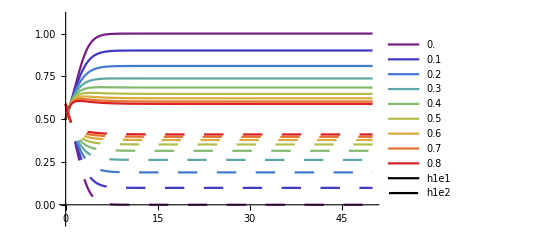

```mathematica
Legended[Plot[{h1e1v,h1e2v},{t,0,50},PlotRange->{-0.1,1.1},PlotStyle->aestable,PlotLegends-> cols ], LineLegend[{linelist[[1]],linelist[[2]]},stratlist]]
```

Let’s try engineering conditions that would favor a boundary equilibrium. Here Hg=Hs=Sg=Ss and all are larger than Hs and Ss. Our analytical work predicts that this scenario will lead to either: the boundary equilibrium with one host one symbiont globally, or the internal polymorphic equilibrium.

```mathematica
(*[h1e10_,h1e20_,s1e10_,s1e20_,HM_,Hg_,Hh_,Hs_, SM_, Sg_,Sh_,Ss_]*)
dynsol=ParametricNDSolveValue[dynsys[0.5,0.59,0.41,0.5,2,1.8,1,1.8,2,1.8,1,1.8],{h1e1[t],h1e2[t],s1e1[t],s1e2[t]},{t,0,100},{d}]
```

ParametricFunction[<>]

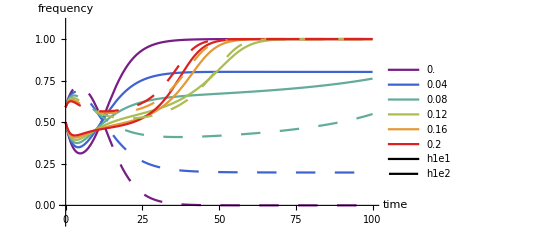

hostplot.jpg

```mathematica
fxntable=Table[{di,dynsol[di]},{di,0,0.2,0.04}];
h1e1v=fxntable[[All,2,1]];
h1e2v=fxntable[[All,2,2]];
cols=fxntable[[All,1]];
stratlist={"h1e1","h1e2"};
linelist={Default,Dashing[{Large,Large}],Dashed,Dotted};
aestable=Table[{linelist[[i]],ColorData["Rainbow"][(j-1)/(Length[cols]-1)]},{i,1,Length[stratlist]},{j,1,Length[cols]}]~Flatten~1;
myplot=Legended[Plot[{h1e1v,h1e2v},{t,0,100},PlotRange->{-0.1,1.1},PlotStyle->aestable,PlotLegends-> cols ,AxesLabel->{"time","frequency"}], LineLegend[{linelist[[1]],linelist[[2]]},stratlist]]
Export["hostplot.jpg",myplot]
```

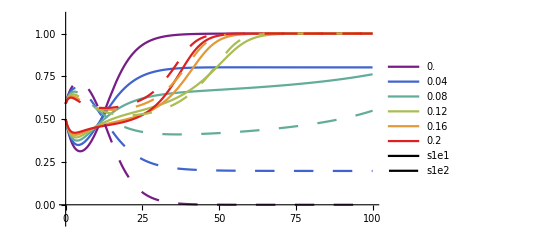

```mathematica
fxntable=Table[{di,dynsol[di]},{di,0,0.2,0.04}];
s1e1v=fxntable[[All,2,3]];
s1e2v=fxntable[[All,2,4]];
cols=fxntable[[All,1]];
stratlist={"s1e1","s1e2"};
linelist={Default,Dashing[{Large,Large}],Dashed,Dotted};
aestable=Table[{linelist[[i]],ColorData["Rainbow"][(j-1)/(Length[cols]-1)]},{i,1,Length[stratlist]},{j,1,Length[cols]}]~Flatten~1;
Legended[Plot[{h1e1v,h1e2v},{t,0,100},PlotRange->{-0.1,1.1},PlotStyle->aestable,PlotLegends-> cols ], LineLegend[{linelist[[1]],linelist[[2]]},stratlist]]
```

#### Solve parametrically and vary dispersal and initial conditions:

To simplify things, only consider where the simulation ends up after a veery long time against our analytic predictions for the internal equilibrium:

```mathematica
tmax=10000;
dynsol=ParametricNDSolveValue[dynsys[0.6,0.5,0.5,0.5,2,1,1,1,2,1,1,1],{h1e1[tmax],h1e2[tmax],s1e1[tmax],s1e2[tmax]},{t,0,tmax},{d}]
```

ParametricFunction[<>]

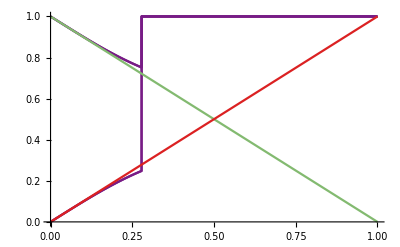

```mathematica
cols={1,2,3};
aestable=Table[{ColorData["Rainbow"][(j-1)/(Length[cols]-1)]},{j,1,Length[cols]}]~Flatten~1;
Plot[{dynsol[d],1-d/(2-1),d/(2-1)},{d,0,1},PlotStyle->aestable]
```

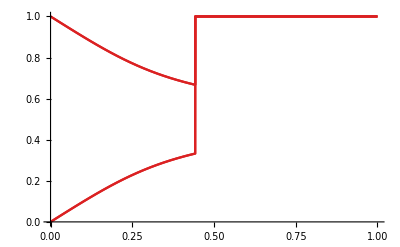

```mathematica
cols={1,2,3};
aestable=Table[{ColorData["Rainbow"][(j-1)/(Length[cols]-1)]},{j,1,Length[cols]}]~Flatten~1;
Plot[{dynsol[d]},{d,0,1},PlotStyle->aestable]
```

Bifurcation! Now, a scenario more favorable to the monomorphic equilibrium:

```mathematica
tmax=10000;
dynsol=ParametricNDSolveValue[dynsys[0.75,0.75,0.75,0.75,2,1,1,1,2,1,1,1],{h1e1[tmax],h1e2[tmax],s1e1[tmax],s1e2[tmax]},{t,0,tmax},{d}]
cols={1,2,3};
aestable=Table[{ColorData["Rainbow"][(j-1)/(Length[cols]-1)]},{j,1,Length[cols]}]~Flatten~1;
Plot[{dynsol[d],1-d/(2-1),d/(2-1)},{d,0,1},PlotStyle->aestable]
```

ParametricFunction[<>]

-Graphics-

Now let’s see if I can engineer a scenario that favors the globally mismatched equilibrium which can be stable when: 
2 d > (Δπ1+Δπ2) and
Δπ1 Δπ2 > d (Δπ1+Δπ2)
true for hosts & symbionts

```mathematica
mismatchparams={HM-> 2, Hg-> 1,Hh-> 1.75,Hs-> 1.75}
{a1b2, a2b2}/.mismatchparams
```

{HM→2,Hg→1,Hh→1.75,Hs→1.75}

{0.5+2 d,-0.1875+0.5 d}

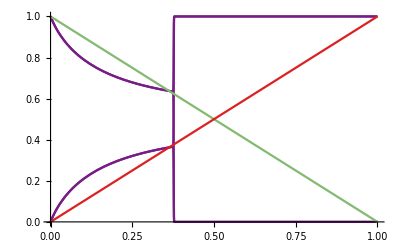

```mathematica
tmax=10000;
dynsol=ParametricNDSolveValue[dynsys[0.55,0.41,0.4,0.55,2,1,1.75,1.75,2,1,1.75,1.75],{h1e1[tmax],h1e2[tmax],s1e1[tmax],s1e2[tmax]},{t,0,tmax},{d}];
cols={1,2,3};
aestable=Table[{ColorData["Rainbow"][(j-1)/(Length[cols]-1)]},{j,1,Length[cols]}]~Flatten~1;
Plot[{dynsol[d],1-d/(2-1),d/(2-1)},{d,0,1},PlotStyle->aestable]
```

```mathematica
tmax=10000;
dynsol=ParametricNDSolveValue[dynsys[h1e10,h1e20,0.5,0.5,2,1,1,1,2,1,1,1],{h1e1[tmax],h1e2[tmax],s1e1[tmax],s1e2[tmax]},{t,0,tmax},{d,h1e10,h1e20}]
```

ParametricFunction[<>]

```mathematica
fxntable=Table[{d,h1e10,h1e20,dynsol[d,h1e10,h1e20]},{h1e10,0.005,0.995,0.03},{h1e20,0.005,0.995,0.03},{d,0,0.5,0.05}]~Flatten~2
```

ParametricNDSolveValue::fpct: Too many parameters in {d} to be filled from {0.,0.005,0.005}.

ParametricNDSolveValue::fpct: Too many parameters in {d} to be filled from {0.05,0.005,0.005}.

ParametricNDSolveValue::fpct: Too many parameters in {d} to be filled from {0.1,0.005,0.005}.

General::stop: Further output of ParametricNDSolveValue::fpct will be suppressed during this calculation.

$Aborted[]

```mathematica
tmax=5000;
dynsol=ParametricNDSolveValue[dynsys[h1e10,h1e10,h1e10,h1e10,2,1,1,1,2,1,1,1],{h1e1[tmax],h1e2[tmax],s1e1[tmax],s1e2[tmax]},{t,0,tmax},{d,h1e10}];
```

```mathematica
fxntable2=Table[{d,h1e10,dynsol[d,h1e10]},{h1e10,0,1,0.05},{d,0,0.5,0.025}]~Flatten~1;
```

```mathematica
jitter=0.015;
ds=fxntable2[[All,1]]+RandomReal[{-jitter/2,jitter/2},Length[fxntable2[[All,2]]] ];
averagef=fxntable2[[All,2]];
h1e1v=fxntable2[[All,3,1]]+RandomReal[{-jitter/2,jitter/2},Length[fxntable2[[All,2]]] ];
h1e2v=fxntable2[[All,3,2]]+RandomReal[{-jitter/2,jitter/2},Length[fxntable2[[All,2]]] ];
```

```mathematica
h1e1p=Transpose@{ds,h1e1v,averagef};
h1e2p=Transpose@{ds,h1e2v,averagef};
```

```mathematica
styledh1e1p=Style[{#,#2},PointSize[.01],ColorData[{"Rainbow",{0,1}}][#3]]&@@@h1e1p;
styledh1e2p=Style[{#,#2},PointSize[.01],ColorData[{"Rainbow",{0,1}}][#3]]&@@@h1e2p;
```

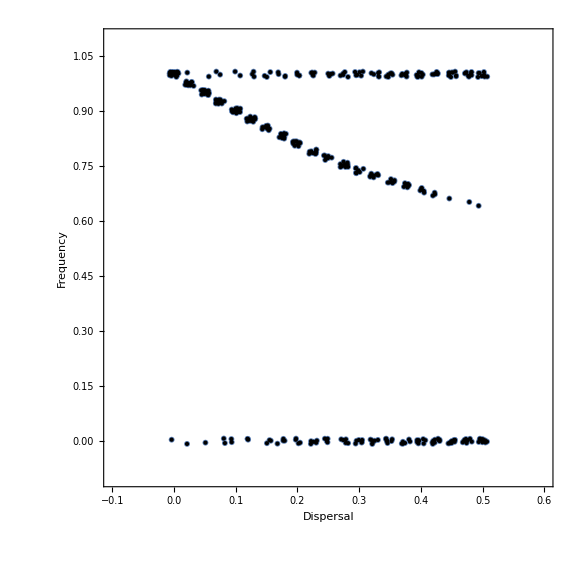

```mathematica
ListPlot[styledh1e1p,Frame->True,FrameLabel->{"Dispersal","Frequency"},PlotRange->{{-0.1,0.6},{-0.1,1.1}},AspectRatio->1,PlotLegends->Placed[BarLegend[{"Rainbow",{0,1}},LegendMargins->{{0,0},{10,5}},LegendLabel->"host 1-symbiont 1 initial frequency",LegendFunction->"Panel"],Right],ImageSize->Large]
```

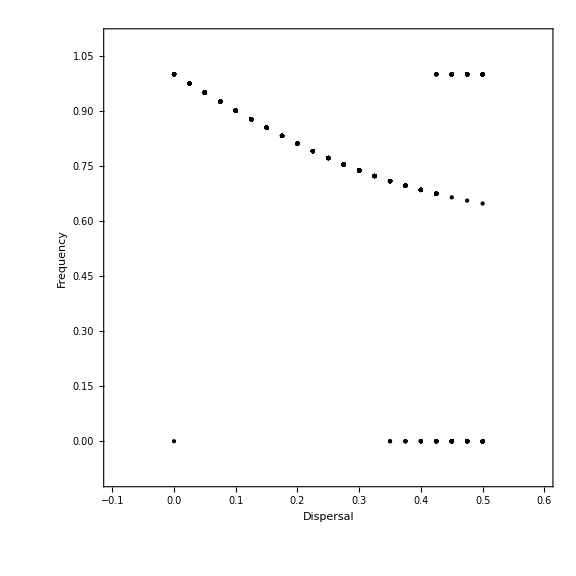

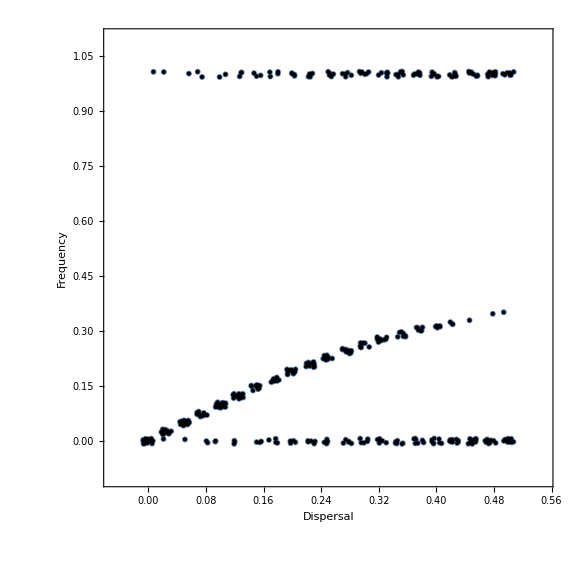

```mathematica
ListPlot[styledh1e2p,Frame->True,FrameLabel->{"Dispersal","Frequency"},AspectRatio->1,PlotRange->{{-0.05,0.55},{-0.1,1.1}},PlotLegends->Placed[BarLegend[{"Rainbow",{0,1}},LegendMargins->{{0,0},{10,5}},LegendLabel->"host 1 initial frequency",LegendFunction->"Panel"],Right],ImageSize->Large]
```

```mathematica
fxntable=Table[{d,h1e10,h1e20,dynsol[d,h1e10,h1e20]},{h1e10,0.005,0.995,0.03},{h1e20,0.005,0.995,0.03},{d,0,0.5,0.05}]~Flatten~2
```

{{0.,0.005,0.005,{1.,-7.42765×10^-55,1.,-7.42765×10^-53}},{0.05,0.005,0.005,{0.950138,0.0498623,0.950138,0.0498623}},12712,{0.45,0.995,0.995,{1.,1.,1.,1.}},{0.5,0.995,0.995,{1.,1.,1.,1.}}}
 |  |  |  |

```mathematica
tmax=10000;
dynsol=ParametricNDSolveValue[dynsys[h1e10,0.5,0.5,0.5,2,1,1,1,2,1,1,1],{h1e1[tmax],h1e2[tmax],s1e1[tmax],s1e2[tmax]},{t,0,tmax},{d,h1e10}];
```

```mathematica
fxntable2=Table[{d,h1e10,dynsol[d,h1e10]},{h1e10,0,1,0.04},{d,0,0.5,0.05}]~Flatten~1;
```

```mathematica
ds=fxntable2[[All,1]];
averagef=fxntable2[[All,2]];
h1e1v=fxntable2[[All,3,1]];
h1e2v=fxntable2[[All,3,2]];
```

```mathematica
h1e1p=Transpose@{ds,h1e1v,averagef};
h1e2p=Transpose@{ds,h1e2v,averagef};
```

```mathematica
styledh1e1p=Style[{#,#2},PointSize[.02],ColorData[{"Rainbow",{0,1}}][#3]]&@@@h1e1p;
styledh1e2p=Style[{#,#2},PointSize[.02],ColorData[{"Rainbow",{0,1}}][#3]]&@@@h1e2p;
```

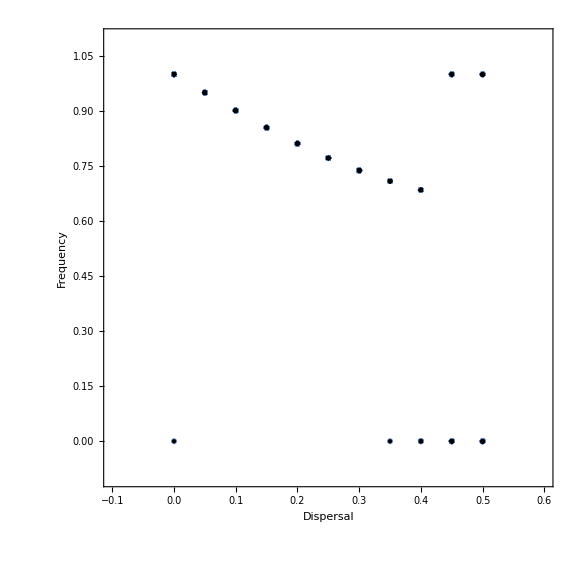

```mathematica
ListPlot[styledh1e1p,Frame->True,FrameLabel->{"Dispersal","Frequency"},PlotRange->{{-0.1,0.6},{-0.1,1.1}},AspectRatio->1,PlotLegends->Placed[BarLegend[{"Rainbow",{0,1}},LegendMargins->{{0,0},{10,5}},LegendLabel->"host 1 initial frequency",LegendFunction->"Panel"],Right],ImageSize->Large]
```

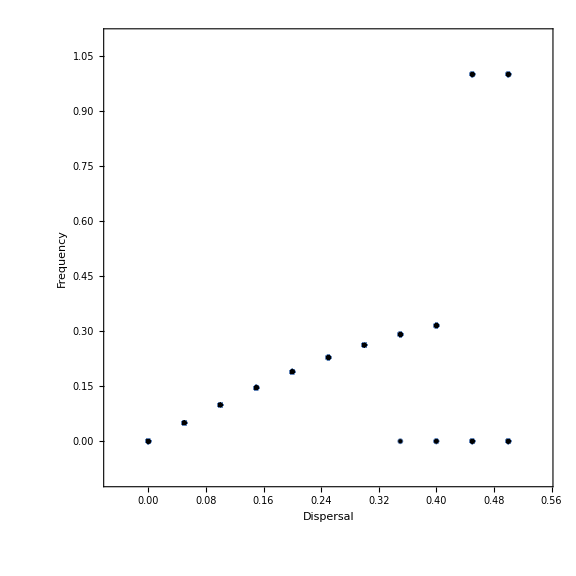

```mathematica
ListPlot[styledh1e2p,Frame->True,FrameLabel->{"Dispersal","Frequency"},AspectRatio->1,PlotRange->{{-0.05,0.55},{-0.1,1.1}},PlotLegends->Placed[BarLegend[{"Rainbow",{0,1}},LegendMargins->{{0,0},{10,5}},LegendLabel->"host 1 initial frequency",LegendFunction->"Panel"],Right],ImageSize->Large]
```

#### environment trumps genotype:

```mathematica
tmax=5000;
(*dynsys[h1e10_,h1e20_,s1e10_,s1e20_,HM_,Hg_,Hh_,Hs_, SM_, Sg_,Sh_,Ss_]*)
dynsol=ParametricNDSolveValue[dynsys[h1e10,h1e10,h1e10,h1e10,2,1,1.75,1,2,1,1,1.75],{h1e1[tmax],h1e2[tmax],s1e1[tmax],s1e2[tmax]},{t,0,tmax},{d,h1e10}];
```

```mathematica
fxntable2=Table[{d,h1e10,dynsol[d,h1e10]},{h1e10,0,1,0.05},{d,0,0.5,0.025}]~Flatten~1;
```

```mathematica
tmax=5000;
dynsol=ParametricNDSolveValue[dynsys[h1e10,h1e10,h1e10,h1e10,2,1,1,1,2,1,1,1],{h1e1[tmax],h1e2[tmax],s1e1[tmax],s1e2[tmax]},{t,0,tmax},{d,h1e10}];
```

```mathematica
fxntable2=Table[{d,h1e10,dynsol[d,h1e10]},{h1e10,0,1,0.05},{d,0,0.5,0.025}]~Flatten~1;
```

```mathematica
jitter=0.015;
ds=fxntable2[[All,1]]+RandomReal[{-jitter/2,jitter/2},Length[fxntable2[[All,2]]] ];
averagef=fxntable2[[All,2]];
h1e1v=fxntable2[[All,3,1]]+RandomReal[{-jitter/2,jitter/2},Length[fxntable2[[All,2]]] ];
h1e2v=fxntable2[[All,3,2]]+RandomReal[{-jitter/2,jitter/2},Length[fxntable2[[All,2]]] ];
```

```mathematica
h1e1p=Transpose@{ds,h1e1v,averagef};
h1e2p=Transpose@{ds,h1e2v,averagef};
```

```mathematica
styledh1e1p=Style[{#,#2},PointSize[.01],ColorData[{"Rainbow",{0,1}}][#3]]&@@@h1e1p;
styledh1e2p=Style[{#,#2},PointSize[.01],ColorData[{"Rainbow",{0,1}}][#3]]&@@@h1e2p;
```

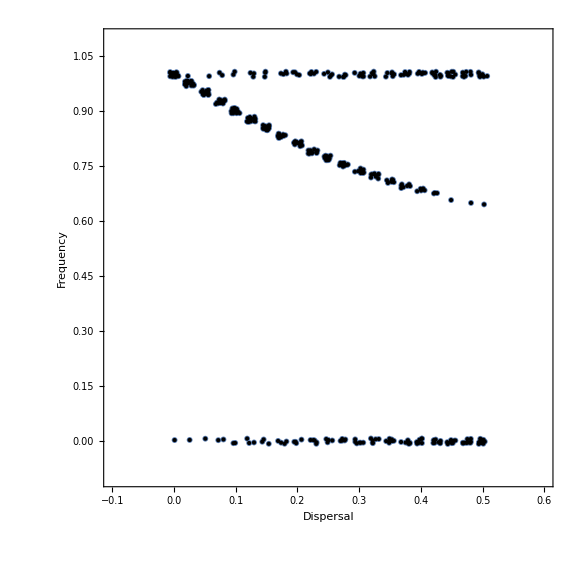

```mathematica
ListPlot[styledh1e1p,Frame->True,FrameLabel->{"Dispersal","Frequency"},PlotRange->{{-0.1,0.6},{-0.1,1.1}},AspectRatio->1,PlotLegends->Placed[BarLegend[{"Rainbow",{0,1}},LegendMargins->{{0,0},{10,5}},LegendLabel->"host 1-symbiont 1 initial frequency",LegendFunction->"Panel"],Right],ImageSize->Large]
```

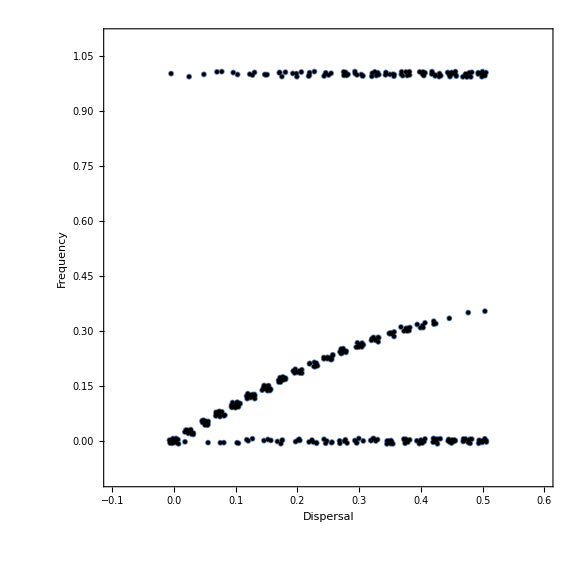

```mathematica
ListPlot[styledh1e2p,Frame->True,FrameLabel->{"Dispersal","Frequency"},PlotRange->{{-0.1,0.6},{-0.1,1.1}},AspectRatio->1,PlotLegends->Placed[BarLegend[{"Rainbow",{0,1}},LegendMargins->{{0,0},{10,5}},LegendLabel->"host 1-symbiont 1 initial frequency",LegendFunction->"Panel"],Right],ImageSize->Large]
```

```mathematica
jitter=0.015;
ds=fxntable2[[All,1]];
averagef=fxntable2[[All,2]];
h1e1v=fxntable2[[All,3,1]];
h1e2v=fxntable2[[All,3,2]];
h1e1p=Transpose@{ds,h1e1v,averagef};
h1e2p=Transpose@{ds,h1e2v,averagef};
```

```mathematica
tmax=5000;
(*dynsys[h1e10_,h1e20_,s1e10_,s1e20_,HM_,Hg_,Hh_,Hs_, SM_, Sg_,Sh_,Ss_]*)
dynsol=ParametricNDSolveValue[dynsys[h1e10,h1e10,h1e10,h1e10,2,1.5,1,1,2,1.5,1,1],{h1e1[tmax],h1e2[tmax],s1e1[tmax],s1e2[tmax]},{t,0,tmax},{d,h1e10}];
```

```mathematica
fxntable2=Table[{d,h1e10,dynsol[d,h1e10]},{h1e10,0,1,0.02},{d,0,0.5,0.025}]~Flatten~1;
```

```mathematica
ds=fxntable2[[All,1]];
averagef=fxntable2[[All,2]];
h1e1v=fxntable2[[All,3,1]];
h1e2v=fxntable2[[All,3,2]];
```

```mathematica
h1e1p=Transpose@{ds,h1e1v,averagef};
h1e2p=Transpose@{ds,h1e2v,averagef};
```

```mathematica
styledh1e1p=Style[{#,#2},PointSize[.02],ColorData[{"Rainbow",{0,1}}][#3]]&@@@h1e1p;
styledh1e2p=Style[{#,#2},PointSize[.02],ColorData[{"Rainbow",{0,1}}][#3]]&@@@h1e2p;
```

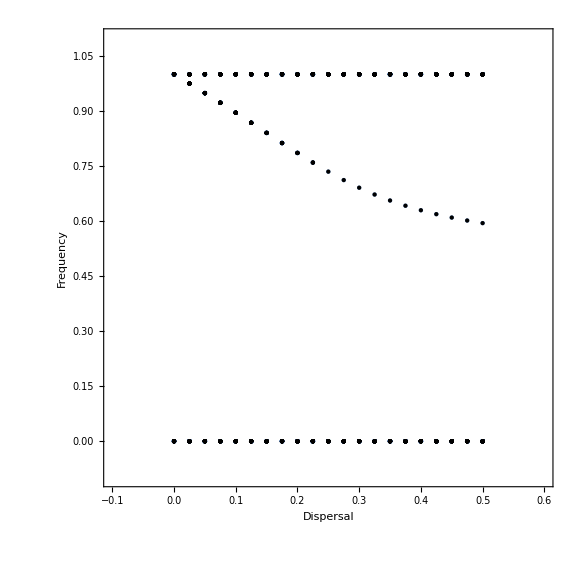

```mathematica
ListPlot[styledh1e1p,Frame->True,FrameLabel->{"Dispersal","Frequency"},PlotRange->{{-0.1,0.6},{-0.1,1.1}},AspectRatio->1,PlotLegends->Placed[BarLegend[{"Rainbow",{0,1}},LegendMargins->{{0,0},{10,5}},LegendLabel->"host 1-symbiont 1 initial frequency",LegendFunction->"Panel"],Right],ImageSize->Large]
```

```mathematica
tmax=5000;
(*dynsys[h1e10_,h1e20_,s1e10_,s1e20_,HM_,Hg_,Hh_,Hs_, SM_, Sg_,Sh_,Ss_]*)
dynsol=ParametricNDSolveValue[dynsys[h1e10,h1e10,h1e10,h1e10,2,1,1.5,1,2,1.5,1,1],{h1e1[tmax],h1e2[tmax],s1e1[tmax],s1e2[tmax]},{t,0,tmax},{d,h1e10}];
```

```mathematica
fxntable2=Table[{d,h1e10,dynsol[d,h1e10]},{h1e10,0,1,0.02},{d,0,0.5,0.025}]~Flatten~1;
```

```mathematica
ds=fxntable2[[All,1]];
averagef=fxntable2[[All,2]];
h1e1v=fxntable2[[All,3,1]];
h1e2v=fxntable2[[All,3,2]];
```

```mathematica
h1e1p=Transpose@{ds,h1e1v,averagef};
h1e2p=Transpose@{ds,h1e2v,averagef};
```

```mathematica
styledh1e1p=Style[{#,#2},PointSize[.02],ColorData[{"Rainbow",{0,1}}][#3]]&@@@h1e1p;
styledh1e2p=Style[{#,#2},PointSize[.02],ColorData[{"Rainbow",{0,1}}][#3]]&@@@h1e2p;
```

```mathematica
ListPlot[styledh1e1p,Frame->True,FrameLabel->{"Dispersal","Frequency"},PlotRange->{{-0.1,0.6},{-0.1,1.1}},AspectRatio->1,PlotLegends->Placed[BarLegend[{"Rainbow",{0,1}},LegendMargins->{{0,0},{10,5}},LegendLabel->"host 1-symbiont 1 initial frequency",LegendFunction->"Panel"],Right],ImageSize->Large]
```

#### Second Order Approximation:

```mathematica
assumptionfn[x_] := x/.{d-> d*ϵ,h1e1->h1e10+ h1e11*ϵ+ h1e12*ϵ^2,s1e1->s1e10+s1e11* ϵ+s1e12* ϵ^2,h1e2-> h1e20+h1e21*ϵ+h1e22*ϵ^2, s1e2->s1e20+s1e21* ϵ+s1e22* ϵ^2};
```

```mathematica
{H1E1d,H1E2d,S1E1d,S1E2d}//assumptionfn//Factor;
Series[%,{ϵ,0,0}]//Normal(*0th Order Approximation*);
ans=Solve[%==0,{h1e10,h1e20,s1e10,s1e20}]
ApproximatedEq={};
Do[{sys={H1E1d,H1E2d,S1E1d,S1E2d}//assumptionfn//Factor;
exp=Series[sys,{ϵ,0,1}]//Normal(*First Order Approximation*);
eval=exp/.ans[[i]]//Factor;
firstorder=Solve[eval==0,{h1e11,h1e21,s1e11,s1e21}]//Factor;
approximated={};
Do[eqi=ans[[ i,j,2]]+firstorder[[1,j,2]];
AppendTo[approximated,eqi],{j,1,4}];
AppendTo[ApproximatedEq,approximated]},{i,1,Length[ans]}]
ApproximatedEq//FullSimplify
```

{{h1e10→(Sg-Ss)/(Sg-Sh+SM-Ss),h1e20→0,s1e10→(Hg-Hh)/(Hg-Hh+HM-Hs),s1e20→0},{h1e10→(Sg-Ss)/(Sg-Sh+SM-Ss),h1e20→1,s1e10→(Hg-Hh)/(Hg-Hh+HM-Hs),s1e20→0},{h1e10→(Sg-Ss)/(Sg-Sh+SM-Ss),h1e20→0,s1e10→(Hg-Hh)/(Hg-Hh+HM-Hs),s1e20→1},{h1e10→(Sg-Ss)/(Sg-Sh+SM-Ss),h1e20→1,s1e10→(Hg-Hh)/(Hg-Hh+HM-Hs),s1e20→1},{h1e10→(Sg-Ss)/(Sg-Sh+SM-Ss),h1e20→(Sh-SM)/(-Sg+Sh-SM+Ss),s1e10→(Hg-Hh)/(Hg-Hh+HM-Hs),s1e20→(HM-Hs)/(Hg-Hh+HM-Hs)},{h1e10→0,h1e20→(Sh-SM)/(-Sg+Sh-SM+Ss),s1e10→0,s1e20→(HM-Hs)/(Hg-Hh+HM-Hs)},{h1e10→1,h1e20→(Sh-SM)/(-Sg+Sh-SM+Ss),s1e10→0,s1e20→(HM-Hs)/(Hg-Hh+HM-Hs)},{h1e10→0,h1e20→(Sh-SM)/(-Sg+Sh-SM+Ss),s1e10→1,s1e20→(HM-Hs)/(Hg-Hh+HM-Hs)},{h1e10→1,h1e20→(Sh-SM)/(-Sg+Sh-SM+Ss),s1e10→1,s1e20→(HM-Hs)/(Hg-Hh+HM-Hs)},{h1e10→0,h1e20→0,s1e10→0,s1e20→0},{h1e10→1,h1e20→0,s1e10→0,s1e20→0},{h1e10→0,h1e20→1,s1e10→0,s1e20→0},{h1e10→1,h1e20→1,s1e10→0,s1e20→0},{h1e10→0,h1e20→0,s1e10→1,s1e20→0},{h1e10→1,h1e20→0,s1e10→1,s1e20→0},{h1e10→0,h1e20→1,s1e10→1,s1e20→0},{h1e10→1,h1e20→1,s1e10→1,s1e20→0},{h1e10→0,h1e20→0,s1e10→0,s1e20→1},{h1e10→1,h1e20→0,s1e10→0,s1e20→1},{h1e10→0,h1e20→1,s1e10→0,s1e20→1},{h1e10→1,h1e20→1,s1e10→0,s1e20→1},{h1e10→0,h1e20→0,s1e10→1,s1e20→1},{h1e10→1,h1e20→0,s1e10→1,s1e20→1},{h1e10→0,h1e20→1,s1e10→1,s1e20→1},{h1e10→1,h1e20→1,s1e10→1,s1e20→1}}

{{(d (Hg-Hh+HM-Hs)+(HM-Hs) (Sg-Ss))/((HM-Hs) (Sg-Sh+SM-Ss)),(d (Sg-Ss))/((HM-Hs) (Sg-Sh+SM-Ss)),((Hg-Hh) (Sh-SM)+d (-Sg+Sh-SM+Ss))/((Hg-Hh+HM-Hs) (Sh-SM)),(d (-Hg+Hh))/((Hg-Hh+HM-Hs) (Sh-SM))},{(d (Hg-Hh+HM-Hs)+(HM-Hs) (Sg-Ss))/((HM-Hs) (Sg-Sh+SM-Ss)),1+(d (-Sh+SM))/((HM-Hs) (Sg-Sh+SM-Ss)),((Hg-Hh) (Sg-Ss)+d (-Sg+Sh-SM+Ss))/((Hg-Hh+HM-Hs) (Sg-Ss)),(d (-Hg+Hh))/((Hg-Hh+HM-Hs) (Sg-Ss))},{(d (-Hg+Hh-HM+Hs)+(Hg-Hh) (Sg-Ss))/((Hg-Hh) (Sg-Sh+SM-Ss)),(d (-Sg+Ss))/((Hg-Hh) (Sg-Sh+SM-Ss)),((Hg-Hh) (Sh-SM)+d (-Sg+Sh-SM+Ss))/((Hg-Hh+HM-Hs) (Sh-SM)),1+(d (-HM+Hs))/((Hg-Hh+HM-Hs) (Sh-SM))},{(d (-Hg+Hh-HM+Hs)+(Hg-Hh) (Sg-Ss))/((Hg-Hh) (Sg-Sh+SM-Ss)),1+(d (Sh-SM))/((Hg-Hh) (Sg-Sh+SM-Ss)),((Hg-Hh) (Sg-Ss)+d (-Sg+Sh-SM+Ss))/((Hg-Hh+HM-Hs) (Sg-Ss)),1+(d (-HM+Hs))/((Hg-Hh+HM-Hs) (Sg-Ss))},{((d (Hg-Hh+HM-Hs) (Hg-Hh-HM+Hs))/((Hg-Hh) (HM-Hs))+Sg-Ss)/(Sg-Sh+SM-Ss),(-(d (Hg-Hh+HM-Hs) (Hg-Hh-HM+Hs))/((Hg-Hh) (HM-Hs))-Sh+SM)/(Sg-Sh+SM-Ss),(Hg-Hh+(d (Sg+Sh-SM-Ss) (-Sg+Sh-SM+Ss))/((Sh-SM) (Sg-Ss)))/(Hg-Hh+HM-Hs),(HM-Hs+(d (Sg+Sh-SM-Ss) (Sg-Sh+SM-Ss))/((Sh-SM) (Sg-Ss)))/(Hg-Hh+HM-Hs)},{(d (Sh-SM))/((Hg-Hh) (-Sg+Sh-SM+Ss)),(d (Hg-Hh+HM-Hs)-(Hg-Hh) (Sh-SM))/((Hg-Hh) (Sg-Sh+SM-Ss)),(d (HM-Hs))/((Hg-Hh+HM-Hs) (Sg-Ss)),((HM-Hs) (Sg-Ss)+d (Sg-Sh+SM-Ss))/((Hg-Hh+HM-Hs) (Sg-Ss))},{1+(d (Sg-Ss))/((Hg-Hh) (Sg-Sh+SM-Ss)),(d (Hg-Hh+HM-Hs)-(Hg-Hh) (Sh-SM))/((Hg-Hh) (Sg-Sh+SM-Ss)),(d (HM-Hs))/((Hg-Hh+HM-Hs) (Sh-SM)),((HM-Hs) (Sh-SM)+d (Sg-Sh+SM-Ss))/((Hg-Hh+HM-Hs) (Sh-SM))},{(d (Sh-SM))/((HM-Hs) (Sg-Sh+SM-Ss)),(d (-Hg+Hh-HM+Hs)-(HM-Hs) (Sh-SM))/((HM-Hs) (Sg-Sh+SM-Ss)),1+(d (Hg-Hh))/((Hg-Hh+HM-Hs) (Sg-Ss)),((HM-Hs) (Sg-Ss)+d (Sg-Sh+SM-Ss))/((Hg-Hh+HM-Hs) (Sg-Ss))},{1+(d (-Sg+Ss))/((HM-Hs) (Sg-Sh+SM-Ss)),(d (-Hg+Hh-HM+Hs)-(HM-Hs) (Sh-SM))/((HM-Hs) (Sg-Sh+SM-Ss)),1+(d (Hg-Hh))/((Hg-Hh+HM-Hs) (Sh-SM)),((HM-Hs) (Sh-SM)+d (Sg-Sh+SM-Ss))/((Hg-Hh+HM-Hs) (Sh-SM))},{0,0,0,0},{1+d/(Hg-Hh),d/(HM-Hs),0,0},{d/(Hg-Hh),1+d/(HM-Hs),0,0},{1,1,0,0},{0,0,1+d/(Sg-Ss),d/(-Sh+SM)},{1+d/(-HM+Hs),d/(HM-Hs),1+d/(Sh-SM),d/(-Sh+SM)},{d/(-HM+Hs),1+d/(HM-Hs),1+d/(Sg-Ss),d/(-Sg+Ss)},{1,1,1+d/(Sh-SM),d/(-Sg+Ss)},{0,0,d/(Sg-Ss),1+d/(-Sh+SM)},{1+d/(Hg-Hh),d/(-Hg+Hh),d/(Sh-SM),1+d/(-Sh+SM)},{d/(Hg-Hh),1+d/(-Hg+Hh),d/(Sg-Ss),1+d/(-Sg+Ss)},{1,1,d/(Sh-SM),1+d/(-Sg+Ss)},{0,0,1,1},{1+d/(-HM+Hs),d/(-Hg+Hh),1,1},{d/(-HM+Hs),1+d/(-Hg+Hh),1,1},{1,1,1,1}}

#### End Clean Work .

Next, to narrow down this list, I’ll approximate the stability conditions for a single equilibrium:

```mathematica
(*Try defining each variable as a taylor series and give it a go!!*)
 assumptionfn[x_] := x/.{d-> d*ϵ,h1e1->h1e10+ h1e11*ϵ,s1e1->s1e10+s1e11* ϵ,h1e2-> h1e20+h1e21*ϵ, s1e2->s1e20+s1e21* ϵ};
J//assumptionfn//MatrixForm//Simplify
%/.{h1e10->1+d/(-HM+Hs),h1e20-> d/(HM-Hs),s1e10-> 1+d/(Sh-SM),s1e20->d/(-Sh+SM)}//assumptionfn//MatrixForm;
Series[%,{ϵ,0,0}]//Normal(*0th Order Approximation*)
Eigenvalues[%]
```

(-d ϵ+(-1+2 h1e10+2 h1e11 ϵ) (Hg+Hh (-1+s1e10+s1e11 ϵ)-Hg (s1e10+s1e11 ϵ)+(-HM+Hs) (s1e10+s1e11 ϵ)) | d ϵ | -(Sg-Sh+SM-Ss) (-1+s1e10+s1e11 ϵ) (s1e10+s1e11 ϵ) | 0
d ϵ | -d ϵ+(-1+2 h1e20+2 h1e21 ϵ) (HM+Hs (-1+s1e20+s1e21 ϵ)+(-Hg+Hh) (s1e20+s1e21 ϵ)-HM (s1e20+s1e21 ϵ)) | 0 | -(Sg-Sh+SM-Ss) (-1+s1e20+s1e21 ϵ) (s1e20+s1e21 ϵ)
-(Hg-Hh+HM-Hs) (-1+h1e10+h1e11 ϵ) (h1e10+h1e11 ϵ) | 0 | -d ϵ-(-1+2 s1e10+2 s1e11 ϵ) (Ss+Sg (-1+h1e10+h1e11 ϵ)-(Sh-SM+Ss) (h1e10+h1e11 ϵ)) | d ϵ
0 | -(Hg-Hh+HM-Hs) (-1+h1e20+h1e21 ϵ) (h1e20+h1e21 ϵ) | d ϵ | -d ϵ-(-1+2 s1e20+2 s1e21 ϵ) (Sh-SM+(Sg-Sh+SM-Ss) (h1e20+h1e21 ϵ)))

(-HM+Hs | 0 | 0 | 0
0 | -HM+Hs | 0 | 0
0 | 0 | Sh-SM | 0
0 | 0 | 0 | Sh-SM)

{-HM+Hs,-HM+Hs,Sh-SM,Sh-SM}

```mathematica
JC = J/.{h1e1->1,h1e2-> 1,s1e1-> 0,s1e2->0}/.d-> ϵ;
(*so note that the change of variables doesn't matter so much since we have values for the frequencies from our earlier approximation. All we're really doing here is d-> d*ϵ. *)
charpoly=CharacteristicPolynomial[JC,λ];
charpolyexp=charpoly/.{λ-> λ0+λ1*ϵ};
(*First, we set ϵ = 0 and solve our characteristic polynomial for our eigenvalues. This gives an approximation of the eigenvalues to the 0th order, with our small parameter (d) equal to 0: *)
b=Series[charpolyexp,{ϵ,0,0}]//Normal;
Othorderλs=Solve[b==0,λ0]
(*These are the 0th order values of λ. We don't really need to go to higher orders because they're all negative. None of them are on the border between stability and instability. But let's go higher as an exercise. *)
a=Series[charpolyexp,{ϵ,0,1}]//Normal 
Solve[%==0,λ1]//Simplify
%/.Othorderλs[[1]]//Simplify
%%/.Othorderλs[[2]]//Simplify
%%%/.Othorderλs[[3]]//Simplify
%%%%/.Othorderλs[[4]]//Simplify
(*So it looks like all the higher order terms go to negative 1, making this equilirium even more stable. Remember that λ1 is proportional to d, the rate of dispersal.  *)
(*The total approximated eigenvalues are: *)
Othorderλs[[1;;4,1,2]]+{-d,-d,-d,-d}
(*It makes sense from our analytical analysis that the stability of this equilibrium would increase with respect to d. Unlike the 1,1,1,1 equilibrium this one is very hard to satisfy unless d is large. *)
```

{{λ0→Hg-Hh},{λ0→HM-Hs},{λ0→-Sh+SM},{λ0→Sg-Ss}}

-(Hg-Hh-λ0) (-HM+Hs+λ0) (Sh-SM+λ0) (-Sg+Ss+λ0)+ϵ ((-Sh+SM-λ0) (Sg-Ss-λ0) ((Hg-Hh-λ0) (-1-λ1)+(HM-Hs-λ0) (-1-λ1))-(Hg-Hh-λ0) (-HM+Hs+λ0) ((-Sh+SM-λ0) (-1-λ1)+(Sg-Ss-λ0) (-1-λ1)))

{{λ1→-((ϵ (Hg-Hh-λ0) (-HM+Hs+λ0) (Sh-SM+λ0)+ϵ (Hg-Hh-λ0) (-HM+Hs+λ0) (-Sg+Ss+λ0)-ϵ (-Hg+Hh+λ0) (Sh-SM+λ0) (-Sg+Ss+λ0)-ϵ (-HM+Hs+λ0) (Sh-SM+λ0) (-Sg+Ss+λ0)+(Hg-Hh-λ0) (-HM+Hs+λ0) (Sh-SM+λ0) (-Sg+Ss+λ0))/(ϵ ((Hg-Hh-λ0) (-HM+Hs+λ0) (Sh-SM+λ0)+(Hg-Hh-λ0) (-HM+Hs+λ0) (-Sg+Ss+λ0)+(Hg-Hh-λ0) (Sh-SM+λ0) (-Sg+Ss+λ0)+(HM-Hs-λ0) (Sh-SM+λ0) (-Sg+Ss+λ0))))}}

{{λ1→-1}}

{{λ1→-1}}

{{λ1→-1}}

«1 more identical outputs»

{-d+Hg-Hh,-d+HM-Hs,-d-Sh+SM,-d+Sg-Ss}

```mathematica
JC=J/.{h1e1->1,h1e2->1,s1e1-> 1,s1e2->1}/.d-> ϵ;
charpoly=CharacteristicPolynomial[JC,λ];
a=Series[charpoly,{ϵ,0,1}]//Normal ;
b=Series[charpoly,{ϵ,0,0}]//Normal;
firstorder=a-b
Solve[b==0,λ]
Solve[firstorder==0,λ]
```

ϵ (-(Sh-SM-λ) (Hg-Hh+λ) (HM-Hs+λ)+(-Sg+Ss-λ) (-(Hg-Hh+λ) (HM-Hs+λ)+(Sh-SM-λ) (Hg-Hh+HM-Hs+2 λ)))

{{λ→-Hg+Hh},{λ→-HM+Hs},{λ→Sh-SM},{λ→-Sg+Ss}}

{{λ→1/4 (-Hg+Hh-HM+Hs-Sg+Sh-SM+Ss)-(-9 (Hg-Hh+HM-Hs+Sg-Sh+SM-Ss)^2+24 (Hg HM-Hh HM-Hg Hs+Hh Hs+Hg Sg-Hh Sg+HM Sg-Hs Sg-Hg Sh+Hh Sh-HM Sh+Hs Sh-Sg Sh+Hg SM-Hh SM+HM SM-Hs SM+Sg SM-Hg Ss+Hh Ss-HM Ss+Hs Ss+Sh Ss-SM Ss))/(6 2^(2/3) ((-54 Hg^3+162 Hg^2 Hh-162 Hg Hh^2+54 Hh^3+54 Hg^2 HM-108 Hg Hh HM+54 Hh^2 HM+54 Hg HM^2-54 Hh HM^2-54 HM^3-54 Hg^2 Hs+108 Hg Hh Hs-54 Hh^2 Hs-108 Hg HM Hs+108 Hh HM Hs+162 HM^2 Hs+54 Hg Hs^2-54 Hh Hs^2-162 HM Hs^2+54 Hs^3+54 Hg^2 Sg-108 Hg Hh Sg+54 Hh^2 Sg-108 Hg HM Sg+108 Hh HM Sg+54 HM^2 Sg+108 Hg Hs Sg-108 Hh Hs Sg-108 HM Hs Sg+54 Hs^2 Sg+54 Hg Sg^2-54 Hh Sg^2+54 HM Sg^2-54 Hs Sg^2-54 Sg^3-54 Hg^2 Sh+108 Hg Hh Sh-54 Hh^2 Sh+108 Hg HM Sh-108 Hh HM Sh-54 HM^2 Sh-108 Hg Hs Sh+108 Hh Hs Sh+108 HM Hs Sh-54 Hs^2 Sh+108 Hg Sg Sh-108 Hh Sg Sh+108 HM Sg Sh-108 Hs Sg Sh-54 Sg^2 Sh+54 Hg Sh^2-54 Hh Sh^2+54 HM Sh^2-54 Hs Sh^2+54 Sg Sh^2+54 Sh^3+54 Hg^2 SM-108 Hg Hh SM+54 Hh^2 SM-108 Hg HM SM+108 Hh HM SM+54 HM^2 SM+108 Hg Hs SM-108 Hh Hs SM-108 HM Hs SM+54 Hs^2 SM-108 Hg Sg SM+108 Hh Sg SM-108 HM Sg SM+108 Hs Sg SM+54 Sg^2 SM-108 Hg Sh SM+108 Hh Sh SM-108 HM Sh SM+108 Hs Sh SM-108 Sg Sh SM-162 Sh^2 SM+54 Hg SM^2-54 Hh SM^2+54 HM SM^2-54 Hs SM^2+54 Sg SM^2+162 Sh SM^2-54 SM^3-54 Hg^2 Ss+108 Hg Hh Ss-54 Hh^2 Ss+108 Hg HM Ss-108 Hh HM Ss-54 HM^2 Ss-108 Hg Hs Ss+108 Hh Hs Ss+108 HM Hs Ss-54 Hs^2 Ss-108 Hg Sg Ss+108 Hh Sg Ss-108 HM Sg Ss+108 Hs Sg Ss+162 Sg^2 Ss-108 Hg Sh Ss+108 Hh Sh Ss-108 HM Sh Ss+108 Hs Sh Ss+108 Sg Sh Ss-54 Sh^2 Ss+108 Hg SM Ss-108 Hh SM Ss+108 HM SM Ss-108 Hs SM Ss-108 Sg SM Ss+108 Sh SM Ss-54 SM^2 Ss+54 Hg Ss^2-54 Hh Ss^2+54 HM Ss^2-54 Hs Ss^2-162 Sg Ss^2-54 Sh Ss^2+54 SM Ss^2+54 Ss^3+√((-54 Hg^3+162 Hg^2 Hh-162 Hg Hh^2+54 Hh^3+54 Hg^2 HM-108 Hg Hh HM+54 Hh^2 HM+54 Hg HM^2-54 Hh HM^2-54 HM^3-54 Hg^2 Hs+108 Hg Hh Hs-54 Hh^2 Hs-108 Hg HM Hs+108 Hh HM Hs+162 HM^2 Hs+54 Hg Hs^2-54 Hh Hs^2-162 HM Hs^2+54 Hs^3+54 Hg^2 Sg-108 Hg Hh Sg+54 Hh^2 Sg-108 Hg HM Sg+108 Hh HM Sg+54 HM^2 Sg+108 Hg Hs Sg-108 Hh Hs Sg-108 HM Hs Sg+54 Hs^2 Sg+54 Hg Sg^2-54 Hh Sg^2+54 HM Sg^2-54 Hs Sg^2-54 Sg^3-54 Hg^2 Sh+108 Hg Hh Sh-54 Hh^2 Sh+108 Hg HM Sh-108 Hh HM Sh-54 HM^2 Sh-108 Hg Hs Sh+108 Hh Hs Sh+108 HM Hs Sh-54 Hs^2 Sh+108 Hg Sg Sh-108 Hh Sg Sh+108 HM Sg Sh-108 Hs Sg Sh-54 Sg^2 Sh+54 Hg Sh^2-54 Hh Sh^2+54 HM Sh^2-54 Hs Sh^2+54 Sg Sh^2+54 Sh^3+54 Hg^2 SM-108 Hg Hh SM+54 Hh^2 SM-108 Hg HM SM+108 Hh HM SM+54 HM^2 SM+108 Hg Hs SM-108 Hh Hs SM-108 HM Hs SM+54 Hs^2 SM-108 Hg Sg SM+108 Hh Sg SM-108 HM Sg SM+108 Hs Sg SM+54 Sg^2 SM-108 Hg Sh SM+108 Hh Sh SM-108 HM Sh SM+108 Hs Sh SM-108 Sg Sh SM-162 Sh^2 SM+54 Hg SM^2-54 Hh SM^2+54 HM SM^2-54 Hs SM^2+54 Sg SM^2+162 Sh SM^2-54 SM^3-54 Hg^2 Ss+108 Hg Hh Ss-54 Hh^2 Ss+108 Hg HM Ss-108 Hh HM Ss-54 HM^2 Ss-108 Hg Hs Ss+108 Hh Hs Ss+108 HM Hs Ss-54 Hs^2 Ss-108 Hg Sg Ss+108 Hh Sg Ss-108 HM Sg Ss+108 Hs Sg Ss+162 Sg^2 Ss-108 Hg Sh Ss+108 Hh Sh Ss-108 HM Sh Ss+108 Hs Sh Ss+108 Sg Sh Ss-54 Sh^2 Ss+108 Hg SM Ss-108 Hh SM Ss+108 HM SM Ss-108 Hs SM Ss-108 Sg SM Ss+108 Sh SM Ss-54 SM^2 Ss+54 Hg Ss^2-54 Hh Ss^2+54 HM Ss^2-54 Hs Ss^2-162 Sg Ss^2-54 Sh Ss^2+54 SM Ss^2+54 Ss^3)^2+4 (-9 (Hg-Hh+HM-Hs+Sg-Sh+SM-Ss)^2+24 (Hg HM-Hh HM-Hg Hs+Hh Hs+Hg Sg-Hh Sg+HM Sg-Hs Sg-Hg Sh+Hh Sh-HM Sh+Hs Sh-Sg Sh+Hg SM-Hh SM+HM SM-Hs SM+Sg SM-Hg Ss+Hh Ss-HM Ss+Hs Ss+Sh Ss-SM Ss))^3)))^(1/3))+1/(12 2^(1/3))((-54 Hg^3+162 Hg^2 Hh-162 Hg Hh^2+54 Hh^3+54 Hg^2 HM-108 Hg Hh HM+54 Hh^2 HM+54 Hg HM^2-54 Hh HM^2-54 HM^3-54 Hg^2 Hs+108 Hg Hh Hs-54 Hh^2 Hs-108 Hg HM Hs+108 Hh HM Hs+162 HM^2 Hs+54 Hg Hs^2-54 Hh Hs^2-162 HM Hs^2+54 Hs^3+54 Hg^2 Sg-108 Hg Hh Sg+54 Hh^2 Sg-108 Hg HM Sg+108 Hh HM Sg+54 HM^2 Sg+108 Hg Hs Sg-108 Hh Hs Sg-108 HM Hs Sg+54 Hs^2 Sg+54 Hg Sg^2-54 Hh Sg^2+54 HM Sg^2-54 Hs Sg^2-54 Sg^3-54 Hg^2 Sh+108 Hg Hh Sh-54 Hh^2 Sh+108 Hg HM Sh-108 Hh HM Sh-54 HM^2 Sh-108 Hg Hs Sh+108 Hh Hs Sh+108 HM Hs Sh-54 Hs^2 Sh+108 Hg Sg Sh-108 Hh Sg Sh+108 HM Sg Sh-108 Hs Sg Sh-54 Sg^2 Sh+54 Hg Sh^2-54 Hh Sh^2+54 HM Sh^2-54 Hs Sh^2+54 Sg Sh^2+54 Sh^3+54 Hg^2 SM-108 Hg Hh SM+54 Hh^2 SM-108 Hg HM SM+108 Hh HM SM+54 HM^2 SM+108 Hg Hs SM-108 Hh Hs SM-108 HM Hs SM+54 Hs^2 SM-108 Hg Sg SM+108 Hh Sg SM-108 HM Sg SM+108 Hs Sg SM+54 Sg^2 SM-108 Hg Sh SM+108 Hh Sh SM-108 HM Sh SM+108 Hs Sh SM-108 Sg Sh SM-162 Sh^2 SM+54 Hg SM^2-54 Hh SM^2+54 HM SM^2-54 Hs SM^2+54 Sg SM^2+162 Sh SM^2-54 SM^3-54 Hg^2 Ss+108 Hg Hh Ss-54 Hh^2 Ss+108 Hg HM Ss-108 Hh HM Ss-54 HM^2 Ss-108 Hg Hs Ss+108 Hh Hs Ss+108 HM Hs Ss-54 Hs^2 Ss-108 Hg Sg Ss+108 Hh Sg Ss-108 HM Sg Ss+108 Hs Sg Ss+162 Sg^2 Ss-108 Hg Sh Ss+108 Hh Sh Ss-108 HM Sh Ss+108 Hs Sh Ss+108 Sg Sh Ss-54 Sh^2 Ss+108 Hg SM Ss-108 Hh SM Ss+108 HM SM Ss-108 Hs SM Ss-108 Sg SM Ss+108 Sh SM Ss-54 SM^2 Ss+54 Hg Ss^2-54 Hh Ss^2+54 HM Ss^2-54 Hs Ss^2-162 Sg Ss^2-54 Sh Ss^2+54 SM Ss^2+54 Ss^3+√((-54 Hg^3+162 Hg^2 Hh-162 Hg Hh^2+54 Hh^3+54 Hg^2 HM-108 Hg Hh HM+54 Hh^2 HM+54 Hg HM^2-54 Hh HM^2-54 HM^3-54 Hg^2 Hs+108 Hg Hh Hs-54 Hh^2 Hs-108 Hg HM Hs+108 Hh HM Hs+162 HM^2 Hs+54 Hg Hs^2-54 Hh Hs^2-162 HM Hs^2+54 Hs^3+54 Hg^2 Sg-108 Hg Hh Sg+54 Hh^2 Sg-108 Hg HM Sg+108 Hh HM Sg+54 HM^2 Sg+108 Hg Hs Sg-108 Hh Hs Sg-108 HM Hs Sg+54 Hs^2 Sg+54 Hg Sg^2-54 Hh Sg^2+54 HM Sg^2-54 Hs Sg^2-54 Sg^3-54 Hg^2 Sh+108 Hg Hh Sh-54 Hh^2 Sh+108 Hg HM Sh-108 Hh HM Sh-54 HM^2 Sh-108 Hg Hs Sh+108 Hh Hs Sh+108 HM Hs Sh-54 Hs^2 Sh+108 Hg Sg Sh-108 Hh Sg Sh+108 HM Sg Sh-108 Hs Sg Sh-54 Sg^2 Sh+54 Hg Sh^2-54 Hh Sh^2+54 HM Sh^2-54 Hs Sh^2+54 Sg Sh^2+54 Sh^3+54 Hg^2 SM-108 Hg Hh SM+54 Hh^2 SM-108 Hg HM SM+108 Hh HM SM+54 HM^2 SM+108 Hg Hs SM-108 Hh Hs SM-108 HM Hs SM+54 Hs^2 SM-108 Hg Sg SM+108 Hh Sg SM-108 HM Sg SM+108 Hs Sg SM+54 Sg^2 SM-108 Hg Sh SM+108 Hh Sh SM-108 HM Sh SM+108 Hs Sh SM-108 Sg Sh SM-162 Sh^2 SM+54 Hg SM^2-54 Hh SM^2+54 HM SM^2-54 Hs SM^2+54 Sg SM^2+162 Sh SM^2-54 SM^3-54 Hg^2 Ss+108 Hg Hh Ss-54 Hh^2 Ss+108 Hg HM Ss-108 Hh HM Ss-54 HM^2 Ss-108 Hg Hs Ss+108 Hh Hs Ss+108 HM Hs Ss-54 Hs^2 Ss-108 Hg Sg Ss+108 Hh Sg Ss-108 HM Sg Ss+108 Hs Sg Ss+162 Sg^2 Ss-108 Hg Sh Ss+108 Hh Sh Ss-108 HM Sh Ss+108 Hs Sh Ss+108 Sg Sh Ss-54 Sh^2 Ss+108 Hg SM Ss-108 Hh SM Ss+108 HM SM Ss-108 Hs SM Ss-108 Sg SM Ss+108 Sh SM Ss-54 SM^2 Ss+54 Hg Ss^2-54 Hh Ss^2+54 HM Ss^2-54 Hs Ss^2-162 Sg Ss^2-54 Sh Ss^2+54 SM Ss^2+54 Ss^3)^2+4 (-9 (Hg-Hh+HM-Hs+Sg-Sh+SM-Ss)^2+24 (Hg HM-Hh HM-Hg Hs+Hh Hs+Hg Sg-Hh Sg+HM Sg-Hs Sg-Hg Sh+Hh Sh-HM Sh+Hs Sh-Sg Sh+Hg SM-Hh SM+HM SM-Hs SM+Sg SM-Hg Ss+Hh Ss-HM Ss+Hs Ss+Sh Ss-SM Ss))^3)))^(1/3)},{λ→1/4 (-Hg+Hh-HM+Hs-Sg+Sh-SM+Ss)+((1+ⅈ √3) (-9 (Hg-Hh+HM-Hs+Sg-Sh+SM-Ss)^2+24 (Hg HM-Hh HM-Hg Hs+Hh Hs+Hg Sg-Hh Sg+HM Sg-Hs Sg-Hg Sh+Hh Sh-HM Sh+Hs Sh-Sg Sh+Hg SM-Hh SM+HM SM-Hs SM+Sg SM-Hg Ss+Hh Ss-HM Ss+Hs Ss+Sh Ss-SM Ss)))/(12 2^(2/3) ((-54 Hg^3+162 Hg^2 Hh-162 Hg Hh^2+54 Hh^3+54 Hg^2 HM-108 Hg Hh HM+54 Hh^2 HM+54 Hg HM^2-54 Hh HM^2-54 HM^3-54 Hg^2 Hs+108 Hg Hh Hs-54 Hh^2 Hs-108 Hg HM Hs+108 Hh HM Hs+162 HM^2 Hs+54 Hg Hs^2-54 Hh Hs^2-162 HM Hs^2+54 Hs^3+54 Hg^2 Sg-108 Hg Hh Sg+54 Hh^2 Sg-108 Hg HM Sg+108 Hh HM Sg+54 HM^2 Sg+108 Hg Hs Sg-108 Hh Hs Sg-108 HM Hs Sg+54 Hs^2 Sg+54 Hg Sg^2-54 Hh Sg^2+54 HM Sg^2-54 Hs Sg^2-54 Sg^3-54 Hg^2 Sh+108 Hg Hh Sh-54 Hh^2 Sh+108 Hg HM Sh-108 Hh HM Sh-54 HM^2 Sh-108 Hg Hs Sh+108 Hh Hs Sh+108 HM Hs Sh-54 Hs^2 Sh+108 Hg Sg Sh-108 Hh Sg Sh+108 HM Sg Sh-108 Hs Sg Sh-54 Sg^2 Sh+54 Hg Sh^2-54 Hh Sh^2+54 HM Sh^2-54 Hs Sh^2+54 Sg Sh^2+54 Sh^3+54 Hg^2 SM-108 Hg Hh SM+54 Hh^2 SM-108 Hg HM SM+108 Hh HM SM+54 HM^2 SM+108 Hg Hs SM-108 Hh Hs SM-108 HM Hs SM+54 Hs^2 SM-108 Hg Sg SM+108 Hh Sg SM-108 HM Sg SM+108 Hs Sg SM+54 Sg^2 SM-108 Hg Sh SM+108 Hh Sh SM-108 HM Sh SM+108 Hs Sh SM-108 Sg Sh SM-162 Sh^2 SM+54 Hg SM^2-54 Hh SM^2+54 HM SM^2-54 Hs SM^2+54 Sg SM^2+162 Sh SM^2-54 SM^3-54 Hg^2 Ss+108 Hg Hh Ss-54 Hh^2 Ss+108 Hg HM Ss-108 Hh HM Ss-54 HM^2 Ss-108 Hg Hs Ss+108 Hh Hs Ss+108 HM Hs Ss-54 Hs^2 Ss-108 Hg Sg Ss+108 Hh Sg Ss-108 HM Sg Ss+108 Hs Sg Ss+162 Sg^2 Ss-108 Hg Sh Ss+108 Hh Sh Ss-108 HM Sh Ss+108 Hs Sh Ss+108 Sg Sh Ss-54 Sh^2 Ss+108 Hg SM Ss-108 Hh SM Ss+108 HM SM Ss-108 Hs SM Ss-108 Sg SM Ss+108 Sh SM Ss-54 SM^2 Ss+54 Hg Ss^2-54 Hh Ss^2+54 HM Ss^2-54 Hs Ss^2-162 Sg Ss^2-54 Sh Ss^2+54 SM Ss^2+54 Ss^3+√((-54 Hg^3+162 Hg^2 Hh-162 Hg Hh^2+54 Hh^3+54 Hg^2 HM-108 Hg Hh HM+54 Hh^2 HM+54 Hg HM^2-54 Hh HM^2-54 HM^3-54 Hg^2 Hs+108 Hg Hh Hs-54 Hh^2 Hs-108 Hg HM Hs+108 Hh HM Hs+162 HM^2 Hs+54 Hg Hs^2-54 Hh Hs^2-162 HM Hs^2+54 Hs^3+54 Hg^2 Sg-108 Hg Hh Sg+54 Hh^2 Sg-108 Hg HM Sg+108 Hh HM Sg+54 HM^2 Sg+108 Hg Hs Sg-108 Hh Hs Sg-108 HM Hs Sg+54 Hs^2 Sg+54 Hg Sg^2-54 Hh Sg^2+54 HM Sg^2-54 Hs Sg^2-54 Sg^3-54 Hg^2 Sh+108 Hg Hh Sh-54 Hh^2 Sh+108 Hg HM Sh-108 Hh HM Sh-54 HM^2 Sh-108 Hg Hs Sh+108 Hh Hs Sh+108 HM Hs Sh-54 Hs^2 Sh+108 Hg Sg Sh-108 Hh Sg Sh+108 HM Sg Sh-108 Hs Sg Sh-54 Sg^2 Sh+54 Hg Sh^2-54 Hh Sh^2+54 HM Sh^2-54 Hs Sh^2+54 Sg Sh^2+54 Sh^3+54 Hg^2 SM-108 Hg Hh SM+54 Hh^2 SM-108 Hg HM SM+108 Hh HM SM+54 HM^2 SM+108 Hg Hs SM-108 Hh Hs SM-108 HM Hs SM+54 Hs^2 SM-108 Hg Sg SM+108 Hh Sg SM-108 HM Sg SM+108 Hs Sg SM+54 Sg^2 SM-108 Hg Sh SM+108 Hh Sh SM-108 HM Sh SM+108 Hs Sh SM-108 Sg Sh SM-162 Sh^2 SM+54 Hg SM^2-54 Hh SM^2+54 HM SM^2-54 Hs SM^2+54 Sg SM^2+162 Sh SM^2-54 SM^3-54 Hg^2 Ss+108 Hg Hh Ss-54 Hh^2 Ss+108 Hg HM Ss-108 Hh HM Ss-54 HM^2 Ss-108 Hg Hs Ss+108 Hh Hs Ss+108 HM Hs Ss-54 Hs^2 Ss-108 Hg Sg Ss+108 Hh Sg Ss-108 HM Sg Ss+108 Hs Sg Ss+162 Sg^2 Ss-108 Hg Sh Ss+108 Hh Sh Ss-108 HM Sh Ss+108 Hs Sh Ss+108 Sg Sh Ss-54 Sh^2 Ss+108 Hg SM Ss-108 Hh SM Ss+108 HM SM Ss-108 Hs SM Ss-108 Sg SM Ss+108 Sh SM Ss-54 SM^2 Ss+54 Hg Ss^2-54 Hh Ss^2+54 HM Ss^2-54 Hs Ss^2-162 Sg Ss^2-54 Sh Ss^2+54 SM Ss^2+54 Ss^3)^2+4 (-9 (Hg-Hh+HM-Hs+Sg-Sh+SM-Ss)^2+24 (Hg HM-Hh HM-Hg Hs+Hh Hs+Hg Sg-Hh Sg+HM Sg-Hs Sg-Hg Sh+Hh Sh-HM Sh+Hs Sh-Sg Sh+Hg SM-Hh SM+HM SM-Hs SM+Sg SM-Hg Ss+Hh Ss-HM Ss+Hs Ss+Sh Ss-SM Ss))^3)))^(1/3))-1/(24 2^(1/3))(1-ⅈ √3) ((-54 Hg^3+162 Hg^2 Hh-162 Hg Hh^2+54 Hh^3+54 Hg^2 HM-108 Hg Hh HM+54 Hh^2 HM+54 Hg HM^2-54 Hh HM^2-54 HM^3-54 Hg^2 Hs+108 Hg Hh Hs-54 Hh^2 Hs-108 Hg HM Hs+108 Hh HM Hs+162 HM^2 Hs+54 Hg Hs^2-54 Hh Hs^2-162 HM Hs^2+54 Hs^3+54 Hg^2 Sg-108 Hg Hh Sg+54 Hh^2 Sg-108 Hg HM Sg+108 Hh HM Sg+54 HM^2 Sg+108 Hg Hs Sg-108 Hh Hs Sg-108 HM Hs Sg+54 Hs^2 Sg+54 Hg Sg^2-54 Hh Sg^2+54 HM Sg^2-54 Hs Sg^2-54 Sg^3-54 Hg^2 Sh+108 Hg Hh Sh-54 Hh^2 Sh+108 Hg HM Sh-108 Hh HM Sh-54 HM^2 Sh-108 Hg Hs Sh+108 Hh Hs Sh+108 HM Hs Sh-54 Hs^2 Sh+108 Hg Sg Sh-108 Hh Sg Sh+108 HM Sg Sh-108 Hs Sg Sh-54 Sg^2 Sh+54 Hg Sh^2-54 Hh Sh^2+54 HM Sh^2-54 Hs Sh^2+54 Sg Sh^2+54 Sh^3+54 Hg^2 SM-108 Hg Hh SM+54 Hh^2 SM-108 Hg HM SM+108 Hh HM SM+54 HM^2 SM+108 Hg Hs SM-108 Hh Hs SM-108 HM Hs SM+54 Hs^2 SM-108 Hg Sg SM+108 Hh Sg SM-108 HM Sg SM+108 Hs Sg SM+54 Sg^2 SM-108 Hg Sh SM+108 Hh Sh SM-108 HM Sh SM+108 Hs Sh SM-108 Sg Sh SM-162 Sh^2 SM+54 Hg SM^2-54 Hh SM^2+54 HM SM^2-54 Hs SM^2+54 Sg SM^2+162 Sh SM^2-54 SM^3-54 Hg^2 Ss+108 Hg Hh Ss-54 Hh^2 Ss+108 Hg HM Ss-108 Hh HM Ss-54 HM^2 Ss-108 Hg Hs Ss+108 Hh Hs Ss+108 HM Hs Ss-54 Hs^2 Ss-108 Hg Sg Ss+108 Hh Sg Ss-108 HM Sg Ss+108 Hs Sg Ss+162 Sg^2 Ss-108 Hg Sh Ss+108 Hh Sh Ss-108 HM Sh Ss+108 Hs Sh Ss+108 Sg Sh Ss-54 Sh^2 Ss+108 Hg SM Ss-108 Hh SM Ss+108 HM SM Ss-108 Hs SM Ss-108 Sg SM Ss+108 Sh SM Ss-54 SM^2 Ss+54 Hg Ss^2-54 Hh Ss^2+54 HM Ss^2-54 Hs Ss^2-162 Sg Ss^2-54 Sh Ss^2+54 SM Ss^2+54 Ss^3+√((-54 Hg^3+162 Hg^2 Hh-162 Hg Hh^2+54 Hh^3+54 Hg^2 HM-108 Hg Hh HM+54 Hh^2 HM+54 Hg HM^2-54 Hh HM^2-54 HM^3-54 Hg^2 Hs+108 Hg Hh Hs-54 Hh^2 Hs-108 Hg HM Hs+108 Hh HM Hs+162 HM^2 Hs+54 Hg Hs^2-54 Hh Hs^2-162 HM Hs^2+54 Hs^3+54 Hg^2 Sg-108 Hg Hh Sg+54 Hh^2 Sg-108 Hg HM Sg+108 Hh HM Sg+54 HM^2 Sg+108 Hg Hs Sg-108 Hh Hs Sg-108 HM Hs Sg+54 Hs^2 Sg+54 Hg Sg^2-54 Hh Sg^2+54 HM Sg^2-54 Hs Sg^2-54 Sg^3-54 Hg^2 Sh+108 Hg Hh Sh-54 Hh^2 Sh+108 Hg HM Sh-108 Hh HM Sh-54 HM^2 Sh-108 Hg Hs Sh+108 Hh Hs Sh+108 HM Hs Sh-54 Hs^2 Sh+108 Hg Sg Sh-108 Hh Sg Sh+108 HM Sg Sh-108 Hs Sg Sh-54 Sg^2 Sh+54 Hg Sh^2-54 Hh Sh^2+54 HM Sh^2-54 Hs Sh^2+54 Sg Sh^2+54 Sh^3+54 Hg^2 SM-108 Hg Hh SM+54 Hh^2 SM-108 Hg HM SM+108 Hh HM SM+54 HM^2 SM+108 Hg Hs SM-108 Hh Hs SM-108 HM Hs SM+54 Hs^2 SM-108 Hg Sg SM+108 Hh Sg SM-108 HM Sg SM+108 Hs Sg SM+54 Sg^2 SM-108 Hg Sh SM+108 Hh Sh SM-108 HM Sh SM+108 Hs Sh SM-108 Sg Sh SM-162 Sh^2 SM+54 Hg SM^2-54 Hh SM^2+54 HM SM^2-54 Hs SM^2+54 Sg SM^2+162 Sh SM^2-54 SM^3-54 Hg^2 Ss+108 Hg Hh Ss-54 Hh^2 Ss+108 Hg HM Ss-108 Hh HM Ss-54 HM^2 Ss-108 Hg Hs Ss+108 Hh Hs Ss+108 HM Hs Ss-54 Hs^2 Ss-108 Hg Sg Ss+108 Hh Sg Ss-108 HM Sg Ss+108 Hs Sg Ss+162 Sg^2 Ss-108 Hg Sh Ss+108 Hh Sh Ss-108 HM Sh Ss+108 Hs Sh Ss+108 Sg Sh Ss-54 Sh^2 Ss+108 Hg SM Ss-108 Hh SM Ss+108 HM SM Ss-108 Hs SM Ss-108 Sg SM Ss+108 Sh SM Ss-54 SM^2 Ss+54 Hg Ss^2-54 Hh Ss^2+54 HM Ss^2-54 Hs Ss^2-162 Sg Ss^2-54 Sh Ss^2+54 SM Ss^2+54 Ss^3)^2+4 (-9 (Hg-Hh+HM-Hs+Sg-Sh+SM-Ss)^2+24 (Hg HM-Hh HM-Hg Hs+Hh Hs+Hg Sg-Hh Sg+HM Sg-Hs Sg-Hg Sh+Hh Sh-HM Sh+Hs Sh-Sg Sh+Hg SM-Hh SM+HM SM-Hs SM+Sg SM-Hg Ss+Hh Ss-HM Ss+Hs Ss+Sh Ss-SM Ss))^3)))^(1/3)},{λ→1/4 (-Hg+Hh-HM+Hs-Sg+Sh-SM+Ss)+((1-ⅈ √3) (-9 (Hg-Hh+HM-Hs+Sg-Sh+SM-Ss)^2+24 (Hg HM-Hh HM-Hg Hs+Hh Hs+Hg Sg-Hh Sg+HM Sg-Hs Sg-Hg Sh+Hh Sh-HM Sh+Hs Sh-Sg Sh+Hg SM-Hh SM+HM SM-Hs SM+Sg SM-Hg Ss+Hh Ss-HM Ss+Hs Ss+Sh Ss-SM Ss)))/(12 2^(2/3) ((-54 Hg^3+162 Hg^2 Hh-162 Hg Hh^2+54 Hh^3+54 Hg^2 HM-108 Hg Hh HM+54 Hh^2 HM+54 Hg HM^2-54 Hh HM^2-54 HM^3-54 Hg^2 Hs+108 Hg Hh Hs-54 Hh^2 Hs-108 Hg HM Hs+108 Hh HM Hs+162 HM^2 Hs+54 Hg Hs^2-54 Hh Hs^2-162 HM Hs^2+54 Hs^3+54 Hg^2 Sg-108 Hg Hh Sg+54 Hh^2 Sg-108 Hg HM Sg+108 Hh HM Sg+54 HM^2 Sg+108 Hg Hs Sg-108 Hh Hs Sg-108 HM Hs Sg+54 Hs^2 Sg+54 Hg Sg^2-54 Hh Sg^2+54 HM Sg^2-54 Hs Sg^2-54 Sg^3-54 Hg^2 Sh+108 Hg Hh Sh-54 Hh^2 Sh+108 Hg HM Sh-108 Hh HM Sh-54 HM^2 Sh-108 Hg Hs Sh+108 Hh Hs Sh+108 HM Hs Sh-54 Hs^2 Sh+108 Hg Sg Sh-108 Hh Sg Sh+108 HM Sg Sh-108 Hs Sg Sh-54 Sg^2 Sh+54 Hg Sh^2-54 Hh Sh^2+54 HM Sh^2-54 Hs Sh^2+54 Sg Sh^2+54 Sh^3+54 Hg^2 SM-108 Hg Hh SM+54 Hh^2 SM-108 Hg HM SM+108 Hh HM SM+54 HM^2 SM+108 Hg Hs SM-108 Hh Hs SM-108 HM Hs SM+54 Hs^2 SM-108 Hg Sg SM+108 Hh Sg SM-108 HM Sg SM+108 Hs Sg SM+54 Sg^2 SM-108 Hg Sh SM+108 Hh Sh SM-108 HM Sh SM+108 Hs Sh SM-108 Sg Sh SM-162 Sh^2 SM+54 Hg SM^2-54 Hh SM^2+54 HM SM^2-54 Hs SM^2+54 Sg SM^2+162 Sh SM^2-54 SM^3-54 Hg^2 Ss+108 Hg Hh Ss-54 Hh^2 Ss+108 Hg HM Ss-108 Hh HM Ss-54 HM^2 Ss-108 Hg Hs Ss+108 Hh Hs Ss+108 HM Hs Ss-54 Hs^2 Ss-108 Hg Sg Ss+108 Hh Sg Ss-108 HM Sg Ss+108 Hs Sg Ss+162 Sg^2 Ss-108 Hg Sh Ss+108 Hh Sh Ss-108 HM Sh Ss+108 Hs Sh Ss+108 Sg Sh Ss-54 Sh^2 Ss+108 Hg SM Ss-108 Hh SM Ss+108 HM SM Ss-108 Hs SM Ss-108 Sg SM Ss+108 Sh SM Ss-54 SM^2 Ss+54 Hg Ss^2-54 Hh Ss^2+54 HM Ss^2-54 Hs Ss^2-162 Sg Ss^2-54 Sh Ss^2+54 SM Ss^2+54 Ss^3+√((-54 Hg^3+162 Hg^2 Hh-162 Hg Hh^2+54 Hh^3+54 Hg^2 HM-108 Hg Hh HM+54 Hh^2 HM+54 Hg HM^2-54 Hh HM^2-54 HM^3-54 Hg^2 Hs+108 Hg Hh Hs-54 Hh^2 Hs-108 Hg HM Hs+108 Hh HM Hs+162 HM^2 Hs+54 Hg Hs^2-54 Hh Hs^2-162 HM Hs^2+54 Hs^3+54 Hg^2 Sg-108 Hg Hh Sg+54 Hh^2 Sg-108 Hg HM Sg+108 Hh HM Sg+54 HM^2 Sg+108 Hg Hs Sg-108 Hh Hs Sg-108 HM Hs Sg+54 Hs^2 Sg+54 Hg Sg^2-54 Hh Sg^2+54 HM Sg^2-54 Hs Sg^2-54 Sg^3-54 Hg^2 Sh+108 Hg Hh Sh-54 Hh^2 Sh+108 Hg HM Sh-108 Hh HM Sh-54 HM^2 Sh-108 Hg Hs Sh+108 Hh Hs Sh+108 HM Hs Sh-54 Hs^2 Sh+108 Hg Sg Sh-108 Hh Sg Sh+108 HM Sg Sh-108 Hs Sg Sh-54 Sg^2 Sh+54 Hg Sh^2-54 Hh Sh^2+54 HM Sh^2-54 Hs Sh^2+54 Sg Sh^2+54 Sh^3+54 Hg^2 SM-108 Hg Hh SM+54 Hh^2 SM-108 Hg HM SM+108 Hh HM SM+54 HM^2 SM+108 Hg Hs SM-108 Hh Hs SM-108 HM Hs SM+54 Hs^2 SM-108 Hg Sg SM+108 Hh Sg SM-108 HM Sg SM+108 Hs Sg SM+54 Sg^2 SM-108 Hg Sh SM+108 Hh Sh SM-108 HM Sh SM+108 Hs Sh SM-108 Sg Sh SM-162 Sh^2 SM+54 Hg SM^2-54 Hh SM^2+54 HM SM^2-54 Hs SM^2+54 Sg SM^2+162 Sh SM^2-54 SM^3-54 Hg^2 Ss+108 Hg Hh Ss-54 Hh^2 Ss+108 Hg HM Ss-108 Hh HM Ss-54 HM^2 Ss-108 Hg Hs Ss+108 Hh Hs Ss+108 HM Hs Ss-54 Hs^2 Ss-108 Hg Sg Ss+108 Hh Sg Ss-108 HM Sg Ss+108 Hs Sg Ss+162 Sg^2 Ss-108 Hg Sh Ss+108 Hh Sh Ss-108 HM Sh Ss+108 Hs Sh Ss+108 Sg Sh Ss-54 Sh^2 Ss+108 Hg SM Ss-108 Hh SM Ss+108 HM SM Ss-108 Hs SM Ss-108 Sg SM Ss+108 Sh SM Ss-54 SM^2 Ss+54 Hg Ss^2-54 Hh Ss^2+54 HM Ss^2-54 Hs Ss^2-162 Sg Ss^2-54 Sh Ss^2+54 SM Ss^2+54 Ss^3)^2+4 (-9 (Hg-Hh+HM-Hs+Sg-Sh+SM-Ss)^2+24 (Hg HM-Hh HM-Hg Hs+Hh Hs+Hg Sg-Hh Sg+HM Sg-Hs Sg-Hg Sh+Hh Sh-HM Sh+Hs Sh-Sg Sh+Hg SM-Hh SM+HM SM-Hs SM+Sg SM-Hg Ss+Hh Ss-HM Ss+Hs Ss+Sh Ss-SM Ss))^3)))^(1/3))-1/(24 2^(1/3))(1+ⅈ √3) ((-54 Hg^3+162 Hg^2 Hh-162 Hg Hh^2+54 Hh^3+54 Hg^2 HM-108 Hg Hh HM+54 Hh^2 HM+54 Hg HM^2-54 Hh HM^2-54 HM^3-54 Hg^2 Hs+108 Hg Hh Hs-54 Hh^2 Hs-108 Hg HM Hs+108 Hh HM Hs+162 HM^2 Hs+54 Hg Hs^2-54 Hh Hs^2-162 HM Hs^2+54 Hs^3+54 Hg^2 Sg-108 Hg Hh Sg+54 Hh^2 Sg-108 Hg HM Sg+108 Hh HM Sg+54 HM^2 Sg+108 Hg Hs Sg-108 Hh Hs Sg-108 HM Hs Sg+54 Hs^2 Sg+54 Hg Sg^2-54 Hh Sg^2+54 HM Sg^2-54 Hs Sg^2-54 Sg^3-54 Hg^2 Sh+108 Hg Hh Sh-54 Hh^2 Sh+108 Hg HM Sh-108 Hh HM Sh-54 HM^2 Sh-108 Hg Hs Sh+108 Hh Hs Sh+108 HM Hs Sh-54 Hs^2 Sh+108 Hg Sg Sh-108 Hh Sg Sh+108 HM Sg Sh-108 Hs Sg Sh-54 Sg^2 Sh+54 Hg Sh^2-54 Hh Sh^2+54 HM Sh^2-54 Hs Sh^2+54 Sg Sh^2+54 Sh^3+54 Hg^2 SM-108 Hg Hh SM+54 Hh^2 SM-108 Hg HM SM+108 Hh HM SM+54 HM^2 SM+108 Hg Hs SM-108 Hh Hs SM-108 HM Hs SM+54 Hs^2 SM-108 Hg Sg SM+108 Hh Sg SM-108 HM Sg SM+108 Hs Sg SM+54 Sg^2 SM-108 Hg Sh SM+108 Hh Sh SM-108 HM Sh SM+108 Hs Sh SM-108 Sg Sh SM-162 Sh^2 SM+54 Hg SM^2-54 Hh SM^2+54 HM SM^2-54 Hs SM^2+54 Sg SM^2+162 Sh SM^2-54 SM^3-54 Hg^2 Ss+108 Hg Hh Ss-54 Hh^2 Ss+108 Hg HM Ss-108 Hh HM Ss-54 HM^2 Ss-108 Hg Hs Ss+108 Hh Hs Ss+108 HM Hs Ss-54 Hs^2 Ss-108 Hg Sg Ss+108 Hh Sg Ss-108 HM Sg Ss+108 Hs Sg Ss+162 Sg^2 Ss-108 Hg Sh Ss+108 Hh Sh Ss-108 HM Sh Ss+108 Hs Sh Ss+108 Sg Sh Ss-54 Sh^2 Ss+108 Hg SM Ss-108 Hh SM Ss+108 HM SM Ss-108 Hs SM Ss-108 Sg SM Ss+108 Sh SM Ss-54 SM^2 Ss+54 Hg Ss^2-54 Hh Ss^2+54 HM Ss^2-54 Hs Ss^2-162 Sg Ss^2-54 Sh Ss^2+54 SM Ss^2+54 Ss^3+√((-54 Hg^3+162 Hg^2 Hh-162 Hg Hh^2+54 Hh^3+54 Hg^2 HM-108 Hg Hh HM+54 Hh^2 HM+54 Hg HM^2-54 Hh HM^2-54 HM^3-54 Hg^2 Hs+108 Hg Hh Hs-54 Hh^2 Hs-108 Hg HM Hs+108 Hh HM Hs+162 HM^2 Hs+54 Hg Hs^2-54 Hh Hs^2-162 HM Hs^2+54 Hs^3+54 Hg^2 Sg-108 Hg Hh Sg+54 Hh^2 Sg-108 Hg HM Sg+108 Hh HM Sg+54 HM^2 Sg+108 Hg Hs Sg-108 Hh Hs Sg-108 HM Hs Sg+54 Hs^2 Sg+54 Hg Sg^2-54 Hh Sg^2+54 HM Sg^2-54 Hs Sg^2-54 Sg^3-54 Hg^2 Sh+108 Hg Hh Sh-54 Hh^2 Sh+108 Hg HM Sh-108 Hh HM Sh-54 HM^2 Sh-108 Hg Hs Sh+108 Hh Hs Sh+108 HM Hs Sh-54 Hs^2 Sh+108 Hg Sg Sh-108 Hh Sg Sh+108 HM Sg Sh-108 Hs Sg Sh-54 Sg^2 Sh+54 Hg Sh^2-54 Hh Sh^2+54 HM Sh^2-54 Hs Sh^2+54 Sg Sh^2+54 Sh^3+54 Hg^2 SM-108 Hg Hh SM+54 Hh^2 SM-108 Hg HM SM+108 Hh HM SM+54 HM^2 SM+108 Hg Hs SM-108 Hh Hs SM-108 HM Hs SM+54 Hs^2 SM-108 Hg Sg SM+108 Hh Sg SM-108 HM Sg SM+108 Hs Sg SM+54 Sg^2 SM-108 Hg Sh SM+108 Hh Sh SM-108 HM Sh SM+108 Hs Sh SM-108 Sg Sh SM-162 Sh^2 SM+54 Hg SM^2-54 Hh SM^2+54 HM SM^2-54 Hs SM^2+54 Sg SM^2+162 Sh SM^2-54 SM^3-54 Hg^2 Ss+108 Hg Hh Ss-54 Hh^2 Ss+108 Hg HM Ss-108 Hh HM Ss-54 HM^2 Ss-108 Hg Hs Ss+108 Hh Hs Ss+108 HM Hs Ss-54 Hs^2 Ss-108 Hg Sg Ss+108 Hh Sg Ss-108 HM Sg Ss+108 Hs Sg Ss+162 Sg^2 Ss-108 Hg Sh Ss+108 Hh Sh Ss-108 HM Sh Ss+108 Hs Sh Ss+108 Sg Sh Ss-54 Sh^2 Ss+108 Hg SM Ss-108 Hh SM Ss+108 HM SM Ss-108 Hs SM Ss-108 Sg SM Ss+108 Sh SM Ss-54 SM^2 Ss+54 Hg Ss^2-54 Hh Ss^2+54 HM Ss^2-54 Hs Ss^2-162 Sg Ss^2-54 Sh Ss^2+54 SM Ss^2+54 Ss^3)^2+4 (-9 (Hg-Hh+HM-Hs+Sg-Sh+SM-Ss)^2+24 (Hg HM-Hh HM-Hg Hs+Hh Hs+Hg Sg-Hh Sg+HM Sg-Hs Sg-Hg Sh+Hh Sh-HM Sh+Hs Sh-Sg Sh+Hg SM-Hh SM+HM SM-Hs SM+Sg SM-Hg Ss+Hh Ss-HM Ss+Hs Ss+Sh Ss-SM Ss))^3)))^(1/3)}}

No need to go to the higher order terms, these are all negative. Suggests that this equilirium will always be negative.

Let’s do the first order approximation just to check my chops:

We got ‘em! So it looks like there’s one equilibrium that is close to the value of the numerical solution. It’s the 15th one in the list! It looks like we can eliminate a lot of the candidate approximate equilibria based on the fact that we’re only interested in the frequencies of the hosts and symbionts when we use numerical values. Let’s see if we can algebraically arrive at a similarly winnowed list of candidates.

```mathematica
(*Try defining each variable as a taylor series and give it a go!!*)
 assumptionfn[x_] := x/.{d-> ϵ};
{H1E1d,H1E2d,S1E1d,S1E2d}//assumptionfn//Factor;
Series[%,{ϵ,0,1}]//Normal(*First Order Approximation*);
Collect[%,ϵ];
coefficients=CoefficientList[%,ϵ]
Zerothorder=%[[All,1]];
Solve[Zerothorder==0,{h1e1,h1e2,s1e1,s1e2}]
Firstorder=%%%[[All,2]];
Solve[Firstorder==0,{h1e1,h1e2,s1e1,s1e2}]
(*ans=Solve[%==0,{h1e1,h1e2,s1e1,s1e2}]//FullSimplify*)
```

### Everything small.

```mathematica
JC = J/.{h1e1->1,h1e2-> 1,s1e1-> 1,s1e2->1}/.d->d ϵ;
(*so note that the change of variables doesn't matter so much since we have values for the frequencies from our earlier approximation. All we're really doing here is d-> d*ϵ. *)
charpoly=CharacteristicPolynomial[JC,λ];
charpolyexp=charpoly/.{λ-> λ0+λ1*ϵ};
(*First, we set ϵ = 0 and solve our characteristic polynomial for our eigenvalues. This gives an approximation of the eigenvalues to the 0th order, with our small parameter (d) equal to 0: *)
b=Series[charpolyexp,{ϵ,0,0}]//Normal;
Othorderλs=Solve[b==0,λ0];
(*These are the 0th order values of λ. We don't really need to go to higher orders because they're all negative. None of them are on the border between stability and instability. But let's go higher as an exercise. *)
a=Series[charpolyexp,{ϵ,0,1}]//Normal ;
c=a/.Othorderλs[[1]]
λ1sol=Solve[c==0,λ1]//Simplify
(*λ11=λ1sol/.Othorderλs[[1]]//Simplify
λ12=λ1sol/.Othorderλs[[2]]//Simplify
λ13=λ1sol/.Othorderλs[[3]]//Simplify
λ14 =λ1sol/.Othorderλs[[4]]//Simplify
(*So it looks like all the higher order terms go to negative 1, making this equilirium even more stable. Remember that λ1 is proportional to d, the rate of dispersal.  *)
(*The total approximated eigenvalues are: *)
approximatedeigval=Othorderλs[[1;;4,1,2]]+{λ11[[1,1,2]],λ12[[1,1,2]],λ13[[1,1,2]],λ13[[1,1,2]]}
(*It makes sense from our analytical analysis that the stability of this equilibrium would increase with respect to d. *)
%/.Unstableparams
lessgoodparams={HM->1,Hh->0.9,Hs->0.9,Hg->0.1,SM->1,Ss->0.9,Sh->0.9,Sg->0.1,d->0.1};
%%%/.lessgoodparams*)
```

(Hg-Hh-HM+Hs) (Hg-Hh+Sh-SM) (Hg-Hh-Sg+Ss) ϵ (-d-λ1)

{{λ1→-d}}

Because I can’t solve the system analytically, I’ll try approximating equilibria using a series expansion around a parameter whose value is very small. I’ll start by assuming that all the model parameters are teeny tiny:

```mathematica
assumptionfn[x_] := x/.symparams/.hostparamsnc/.{fθ-> fθ*ϵ,θ-> θ*ϵ,fρ-> fρ*ϵ,ρ-> ρ*ϵ ,r-> r*ϵ,fr-> fr*ϵ,d-> d*ϵ}
```

```mathematica
{H1E1d,H1E2d,S1E1d,S1E2d}//assumptionfn//Factor;
Series[%,{ϵ,0,1}]//Normal(*First Order Approximation*)
ans=Solve[%==0,{h1e1,h1e2,s1e1,s1e2}]//FullSimplify
```

{(-d h1e1+d h1e2) ϵ,(d h1e1-d h1e2) ϵ,(-d s1e1+d s1e2) ϵ,(d s1e1-d s1e2) ϵ}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{h1e2→h1e1,s1e2→s1e1}}

This equilibrium makes intuitive sense. Let’s check its stability. See Otto & Day pp. 183.

```mathematica
J2=J//assumptionfn;
JC = J2/.ans[[1]];
charpoly=CharacteristicPolynomial[JC,λ];
a=Series[charpoly,{ϵ,0,1}]//Normal 
b=Series[charpoly,{ϵ,0,0}]//Normal
firstorder=a-b
Solve[b==0,λ]
Solve[firstorder==0,λ]
```

4 d ϵ λ^3+λ^4

λ^4

4 d ϵ λ^3

{{λ→0},{λ→0},{λ→0},{λ→0}}

{{λ→0},{λ→0},{λ→0}}

Entirely neutral stability makes sense. There’s really no difference between either strategist when everything is itty bitty, and the strategists can diffuse between the two habitats which promotes variation.

Let’s check this method against a case where we can solve for equilibria and eigenvalues. I’ll make everything itty bitty except for diffusion, which will be nonexistent:

```mathematica
assumptionfn[x_] := x/.symparams/.hostparamsnc/.{d-> 0}
```

```mathematica
{H1E1d,H1E2d,S1E1d,S1E2d}//assumptionfn//Factor;
Series[%,{ϵ,0,1}]//Normal(*First Order Approximation*);
ans=Solve[%==0,{h1e1,h1e2,s1e1,s1e2}]//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{h1e2→h1e1,s1e2→s1e1}}

```mathematica
J2=J//assumptionfn;
JC = J2/.ans[[1]];
charpoly=CharacteristicPolynomial[JC,λ];
a=Series[charpoly,{ϵ,0,1}]//Normal //FullSimplify
Solve[a==0,λ]
b=Series[charpoly,{ϵ,0,0}]//Normal
firstorder=a-b
Solve[b==0,λ]
Solve[firstorder==0,λ]
```

λ^3 (4 d ϵ+λ)

{{λ→0},{λ→0},{λ→0},{λ→-4 d ϵ}}

λ^4

-λ^4+λ^3 (4 d ϵ+λ)

{{λ→0},{λ→0},{λ→0},{λ→0}}

{{λ→0},{λ→0},{λ→0}}

This is a slightly different answer but still suggests neutral stability.

```mathematica
ApproxStabilityfxn[eq_]:= Table[ {JC=J//assumptionfn;
JC/.ans[[i]],
charpoly=CharacteristicPolynomial[JC,λ];
a=Series[charpoly,{ϵ,0,1}]//Normal ,
b=Series[charpoly,{ϵ,0,0}]//Normal,
firstorder=a-b,
Solve[a==0,λ],
Solve[firstorder==0,λ]

 },{i,1,Length[eq]}]
(*Function for approximating equilibria. Inputs are a matrix of equilibria, and specification of order with an integer. *)
(*stabilityfn = ApproxEigvalfxn[ans,1]*)
```

## Everything Teeny with payoffs:

Doesn’t solve, which is interesting.

```mathematica
assumptionfn[x_] := x/.{smatch->smatch*ϵ, smismatchrθ-> smismatchrθ*ϵ (*may need to multiply ϵ by a constant for each case*), smismatchρr-> smismatchρr*ϵ,smismatchθρ-> smismatchθρ*ϵ,hmatch ->hmatch*ϵ, hmismatchrθ-> hmismatchrθ*ϵ, hmismatchθρ-> hmismatchθρ*ϵ, himsmatchρr-> himsmatchρr*ϵ,d->d*ϵ(*introduce new parameters that are scalable to ϵ to back transform to original. *)}
```

```mathematica
{H1E1d,H1E2d,S1E1d,S1E2d}//assumptionfn//Factor;
Series[%,{ϵ,0,1}]//Normal(*First Order Approximation*)
ans=Solve[%==0,{h1e1,h1e2,s1e1,s1e2}]//FullSimplify//Chop
```

{(-d h1e1+d h1e2+h1e1 himsmatchρr-h1e1^2 himsmatchρr-h1e1 hmismatchθρ+h1e1^2 hmismatchθρ-h1e1 himsmatchρr s1e1+h1e1^2 himsmatchρr s1e1+h1e1 hmatch s1e1-h1e1^2 hmatch s1e1-h1e1 hmismatchrθ s1e1+h1e1^2 hmismatchrθ s1e1+h1e1 hmismatchθρ s1e1-h1e1^2 hmismatchθρ s1e1) ϵ,(d h1e1-d h1e2-h1e2 hmatch+h1e2^2 hmatch+h1e2 hmismatchrθ-h1e2^2 hmismatchrθ-h1e2 himsmatchρr s1e2+h1e2^2 himsmatchρr s1e2+h1e2 hmatch s1e2-h1e2^2 hmatch s1e2-h1e2 hmismatchrθ s1e2+h1e2^2 hmismatchrθ s1e2+h1e2 hmismatchθρ s1e2-h1e2^2 hmismatchθρ s1e2) ϵ,(-d s1e1+d s1e2+h1e1 s1e1 smatch-h1e1 s1e1^2 smatch+s1e1 smismatchrθ-h1e1 s1e1 smismatchrθ-s1e1^2 smismatchrθ+h1e1 s1e1^2 smismatchrθ-s1e1 smismatchθρ+h1e1 s1e1 smismatchθρ+s1e1^2 smismatchθρ-h1e1 s1e1^2 smismatchθρ-h1e1 s1e1 smismatchρr+h1e1 s1e1^2 smismatchρr) ϵ,(d s1e1-d s1e2-s1e2 smatch+h1e2 s1e2 smatch+s1e2^2 smatch-h1e2 s1e2^2 smatch-h1e2 s1e2 smismatchrθ+h1e2 s1e2^2 smismatchrθ+h1e2 s1e2 smismatchθρ-h1e2 s1e2^2 smismatchθρ+s1e2 smismatchρr-h1e2 s1e2 smismatchρr-s1e2^2 smismatchρr+h1e2 s1e2^2 smismatchρr) ϵ}

$Aborted

It looks like there are some higher order interactions between terms that get preserved in this payoffs case that get preserved in the parameters case. Maybe we can mitigate these interactions and achieve a solution. Should ϵ be scaled by a constant?

```mathematica
assumptionfn[x_] := x/.{smatch->smatch*ϵ, smismatchrθ-> smismatchrθ*ϵ (*may need to multiply ϵ by a constant for each case*), smismatchρr-> smismatchρr*ϵ,smismatchθρ-> smismatchθρ*ϵ,hmatch ->hmatch*ϵ, hmismatchrθ-> hmismatchrθ*ϵ, hmismatchθρ-> hmismatchθρ*ϵ, himsmatchρr-> himsmatchρr*ϵ,d->d*ϵ(*introduce new parameters that are scalable to ϵ to back transform to original. *)}
```

### Only dispersal is small

```mathematica
assumptionfn[x_] := x/.{d-> 0}
 {H1E1d,H1E2d,S1E1d,S1E2d}//assumptionfn//Factor;
ans=Solve[%==0,{h1e1,h1e2,s1e1,s1e2}]//FullSimplify;
```

```mathematica
assumptionfn[x_] := x/.hostparamsnc/.symparams/.{d-> ϵ}
```

```mathematica
{H1E1d,H1E2d,S1E1d,S1E2d}//assumptionfn//Factor;
Series[%,{ϵ,0,1}]//Normal;(*First Order Approximation*)
(*Try defining each variable as a taylor series and give it a go!!*)
```

```mathematica
ans=Solve[%==0,{h1e1,h1e2,s1e1,s1e2}]//FullSimplify
```

$Aborted

Doesn’t solve, which is disappointing.

### ϵ proportionate to a constant

During our last meeting that some clarity might be gained from making each instance of the small constant epsilon proportionate to a constant:

```mathematica
assumptionfn[x_] := x/.{smatch->smatch*ϵ*c1, smismatchrθ-> smismatchrθ*ϵ*c2 , smismatchρr-> smismatchρr*ϵ*c3,smismatchθρ-> smismatchθρ*ϵ*c4,hmatch ->hmatch*ϵ*c5, hmismatchrθ-> hmismatchrθ*ϵ*c6, hmismatchθρ-> hmismatchθρ*ϵ*c7, himsmatchρr-> himsmatchρr*ϵ*c8,d->d*ϵ*c9}
```

```mathematica
{H1E1d,H1E2d,S1E1d,S1E2d}//assumptionfn//Factor;
Series[%,{ϵ,0,1}]//Normal(*First Order Approximation*)
ans=Solve[%==0,{h1e1,h1e2,s1e1,s1e2}]//FullSimplify//Chop
```

{(-c9 d h1e1+c9 d h1e2+c8 h1e1 himsmatchρr-c8 h1e1^2 himsmatchρr-c7 h1e1 hmismatchθρ+c7 h1e1^2 hmismatchθρ-c8 h1e1 himsmatchρr s1e1+c8 h1e1^2 himsmatchρr s1e1+c5 h1e1 hmatch s1e1-c5 h1e1^2 hmatch s1e1-c6 h1e1 hmismatchrθ s1e1+c6 h1e1^2 hmismatchrθ s1e1+c7 h1e1 hmismatchθρ s1e1-c7 h1e1^2 hmismatchθρ s1e1) ϵ,(c9 d h1e1-c9 d h1e2-c5 h1e2 hmatch+c5 h1e2^2 hmatch+c6 h1e2 hmismatchrθ-c6 h1e2^2 hmismatchrθ-c8 h1e2 himsmatchρr s1e2+c8 h1e2^2 himsmatchρr s1e2+c5 h1e2 hmatch s1e2-c5 h1e2^2 hmatch s1e2-c6 h1e2 hmismatchrθ s1e2+c6 h1e2^2 hmismatchrθ s1e2+c7 h1e2 hmismatchθρ s1e2-c7 h1e2^2 hmismatchθρ s1e2) ϵ,(-c9 d s1e1+c9 d s1e2+c1 h1e1 s1e1 smatch-c1 h1e1 s1e1^2 smatch+c2 s1e1 smismatchrθ-c2 h1e1 s1e1 smismatchrθ-c2 s1e1^2 smismatchrθ+c2 h1e1 s1e1^2 smismatchrθ-c4 s1e1 smismatchθρ+c4 h1e1 s1e1 smismatchθρ+c4 s1e1^2 smismatchθρ-c4 h1e1 s1e1^2 smismatchθρ-c3 h1e1 s1e1 smismatchρr+c3 h1e1 s1e1^2 smismatchρr) ϵ,(c9 d s1e1-c9 d s1e2-c1 s1e2 smatch+c1 h1e2 s1e2 smatch+c1 s1e2^2 smatch-c1 h1e2 s1e2^2 smatch-c2 h1e2 s1e2 smismatchrθ+c2 h1e2 s1e2^2 smismatchrθ+c4 h1e2 s1e2 smismatchθρ-c4 h1e2 s1e2^2 smismatchθρ+c3 s1e2 smismatchρr-c3 h1e2 s1e2 smismatchρr-c3 s1e2^2 smismatchρr+c3 h1e2 s1e2^2 smismatchρr) ϵ}

$Aborted

Doesn’t seem to yield much here.

### Transforming to parameters that are scalable to ϵ:

The idea here is to introduce a new system of parameters that are all proportional to ϵ.

```mathematica
assumptionfn[x_] := x/.{smatch->symma*ϵ, smismatchrθ-> symrθ*ϵ (*may need to multiply ϵ by a constant for each case*), smismatchρr-> symρ*ϵ,smismatchθρ-> symθρ*ϵ,hmatch ->hom*ϵ, hmismatchrθ-> horθ*ϵ, hmismatchθρ-> hoθρ*ϵ, himsmatchρr-> hoρr*ϵ,d->di*ϵ(*introduce new parameters that are scalable to ϵ to back transform to original. *)}
 {H1E1d,H1E2d,S1E1d,S1E2d}//assumptionfn//Factor;
Series[%,{ϵ,0,1}]//Normal(*First Order Approximation*)
ans=Solve[%==0,{h1e1,h1e2,s1e1,s1e2}]//FullSimplify
```

{(-di h1e1+di h1e2-h1e1 hoθρ+h1e1^2 hoθρ+h1e1 hoρr-h1e1^2 hoρr+h1e1 hom s1e1-h1e1^2 hom s1e1-h1e1 horθ s1e1+h1e1^2 horθ s1e1+h1e1 hoθρ s1e1-h1e1^2 hoθρ s1e1-h1e1 hoρr s1e1+h1e1^2 hoρr s1e1) ϵ,(di h1e1-di h1e2-h1e2 hom+h1e2^2 hom+h1e2 horθ-h1e2^2 horθ+h1e2 hom s1e2-h1e2^2 hom s1e2-h1e2 horθ s1e2+h1e2^2 horθ s1e2+h1e2 hoθρ s1e2-h1e2^2 hoθρ s1e2-h1e2 hoρr s1e2+h1e2^2 hoρr s1e2) ϵ,(-di s1e1+di s1e2+h1e1 s1e1 symma-h1e1 s1e1^2 symma+s1e1 symrθ-h1e1 s1e1 symrθ-s1e1^2 symrθ+h1e1 s1e1^2 symrθ-s1e1 symθρ+h1e1 s1e1 symθρ+s1e1^2 symθρ-h1e1 s1e1^2 symθρ-h1e1 s1e1 symρ+h1e1 s1e1^2 symρ) ϵ,(di s1e1-di s1e2-s1e2 symma+h1e2 s1e2 symma+s1e2^2 symma-h1e2 s1e2^2 symma-h1e2 s1e2 symrθ+h1e2 s1e2^2 symrθ+h1e2 s1e2 symθρ-h1e2 s1e2^2 symθρ+s1e2 symρ-h1e2 s1e2 symρ-s1e2^2 symρ+h1e2 s1e2^2 symρ) ϵ}

$Aborted

This doesn’t seem to work for the case with payoffs. Maybe try it with the usual parameters:

```mathematica
assumptionfn[x_] := x/.symparams/.hostparamsnc/.{fθ-> fθn*ϵ,θ-> θn*ϵ,fρ-> fρn*ϵ,ρ-> ρn*ϵ ,r-> rn*ϵ,fr-> frn*ϵ,d-> dn*ϵ}
```

```mathematica
{H1E1d,H1E2d,S1E1d,S1E2d}//assumptionfn//Factor;
Series[%,{ϵ,0,1}]//Normal(*First Order Approximation*)
ans=Solve[%==0,{h1e1,h1e2,s1e1,s1e2}]//FullSimplify
```

{(-dn h1e1+dn h1e2) ϵ,(dn h1e1-dn h1e2) ϵ,(-dn s1e1+dn s1e2) ϵ,(dn s1e1-dn s1e2) ϵ}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{h1e2→h1e1,s1e2→s1e1}}

Yields the same equilibria as usual.

### Large g x g:

```mathematica
assumptionfn[x_] := x/.symparams/.hostparamsnc/.{fθ-> fθ
*ϵ,θ-> θ*ϵ,fρ-> ρ*ϵ,ρ-> ρ*ϵ ,d-> d*ϵ}
```

```mathematica
{H1E1d,H1E2d,S1E1d,S1E2d}//assumptionfn//Factor;
Series[%,{ϵ,0,1}]//Normal(*First Order Approximation*)
ans=Solve[%==0,{h1e1,h1e2,s1e1,s1e2}]//FullSimplify
```

{(-d h1e1+d h1e2) ϵ,(d h1e1-d h1e2) ϵ,(-d s1e1+d s1e2) ϵ,(d s1e1-d s1e2) ϵ}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{h1e2→h1e1,s1e2→s1e1}}

```mathematica
J2=J//assumptionfn;
JC = J2/.ans[[1]];
charpoly=CharacteristicPolynomial[JC,λ];
a=Series[charpoly,{ϵ,0,1}]//Normal 
b=Series[charpoly,{ϵ,0,0}]//Normal
firstorder=a-b
Solve[a==0,λ]
Solve[firstorder==0,λ]
```

4 d ϵ λ^3+λ^4

λ^4

4 d ϵ λ^3

{{λ→0},{λ→0},{λ→0},{λ→-4 d ϵ}}

{{λ→0},{λ→0},{λ→0}}

Read Otto and Day for interpretation.

### Large g x e for symbionts:

```mathematica
assumptionfn[x_] := x/.symparams/.hostparamsnc/.{r-> r*ϵ, fr-> fr*ϵ,fθ-> fθ*ϵ,θ-> θ*ϵ,d-> d*ϵ}
```

```mathematica
{H1E1d,H1E2d,S1E1d,S1E2d}//assumptionfn//Factor;
Series[%,{ϵ,0,1}]//Normal(*First Order Approximation*)
ans=Solve[%==0,{h1e1,h1e2,s1e1,s1e2}]//FullSimplify
```

{(-d h1e1+d h1e2) ϵ,(d h1e1-d h1e2) ϵ,(-d s1e1+d s1e2) ϵ,(d s1e1-d s1e2) ϵ}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{h1e2→h1e1,s1e2→s1e1}}

Let’s try applying the change to another variable system to this case:

```mathematica
assumptionfn[x_] := x/.symparams/.hostparamsnc/.{fθ-> fθn*ϵ,θ-> θn*ϵ,r-> rn*ϵ,fr-> frn*ϵ,d-> dn*ϵ}
```

```mathematica
{H1E1d,H1E2d,S1E1d,S1E2d}//assumptionfn//Factor;
Series[%,{ϵ,0,1}]//Normal(*First Order Approximation*)
ans=Solve[%==0,{h1e1,h1e2,s1e1,s1e2}]//FullSimplify
```

{(-dn h1e1+dn h1e2) ϵ,(dn h1e1-dn h1e2) ϵ,(-dn s1e1+dn s1e2) ϵ,(dn s1e1-dn s1e2) ϵ}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{h1e2→h1e1,s1e2→s1e1}}

### Additive differences:

```mathematica
assumptionfn[x_] := x/.{smatch->smatch, smismatchrθ-> smatch+ϵ*rθ (*may need to multiply ϵ by a constant for each case, keeping track of the parameters. Here we don't know where the epsilon's come from.*), smismatchρr-> smatch+ϵ,smismatchθρ-> smatch+ϵ,hmatch ->hmatch, hmismatchrθ-> hmatch+ϵ, hmismatchθρ-> hmatch+ϵ, himsmatchρr-> hmatch+ϵ,d->d*ϵ}
```

```mathematica
{H1E1d,H1E2d,S1E1d,S1E2d}//assumptionfn//Factor;
Series[%,{ϵ,0,1}]//Normal(*First Order Approximation*)
ans=Solve[%==0,{h1e1,h1e2,s1e1,s1e2}]//FullSimplify//Chop
```

{(-d h1e1+d h1e2-h1e1 s1e1+h1e1^2 s1e1) ϵ,(d h1e1+h1e2-d h1e2-h1e2^2-h1e2 s1e2+h1e2^2 s1e2) ϵ,(-d s1e1-h1e1 s1e1+h1e1 s1e1^2+d s1e2) ϵ,(d s1e1+s1e2-d s1e2-h1e2 s1e2-s1e2^2+h1e2 s1e2^2) ϵ}

{{h1e1→0,h1e2→0,s1e1→0,s1e2→0},{h1e1→1,h1e2→1,s1e1→0,s1e2→0},{h1e1→0,h1e2→0,s1e1→1,s1e2→1},{h1e1→1,h1e2→1,s1e1→1,s1e2→1},{h1e1→1/4 (1+√(1-4 d)-√2 √(1+√(1-4 d)+6 d)),h1e2→1/4 (3-√(1-4 d)-√2 √(1+√(1-4 d)+6 d)),s1e1→1/4 (1+√(1-4 d)-√2 √(1+√(1-4 d)+6 d)),s1e2→1/4 (3-√(1-4 d)-√2 √(1+√(1-4 d)+6 d))},{h1e1→1/4 (1+√(1-4 d)+√2 √(1+√(1-4 d)+6 d)),h1e2→1/4 (3-√(1-4 d)+√2 √(1+√(1-4 d)+6 d)),s1e1→1/4 (1+√(1-4 d)+√2 √(1+√(1-4 d)+6 d)),s1e2→1/4 (3-√(1-4 d)+√2 √(1+√(1-4 d)+6 d))},{h1e1→1/4 (1-√(1-4 d)-√(2-2 √(1-4 d)+12 d)),h1e2→1/4 (3+√(1-4 d)-√(2-2 √(1-4 d)+12 d)),s1e1→1/4 (1-√(1-4 d)-√(2-2 √(1-4 d)+12 d)),s1e2→1/4 (3+√(1-4 d)-√(2-2 √(1-4 d)+12 d))},{h1e1→1/4 (1-√(1-4 d)+√(2-2 √(1-4 d)+12 d)),h1e2→1/4 (3+√(1-4 d)+√(2-2 √(1-4 d)+12 d)),s1e1→1/4 (1-√(1-4 d)+√(2-2 √(1-4 d)+12 d)),s1e2→1/4 (3+√(1-4 d)+√(2-2 √(1-4 d)+12 d))},{h1e1→(2 2^(1/3)+12 2^(1/3) d+2 (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(1/3)+(4-18 d+6 √3 √(-d (4+d (13+32 d))))^(2/3))/(6 (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(1/3)),h1e2→(-2 2^(1/3)-12 2^(1/3) d+4 (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(1/3)-(4-18 d+6 √3 √(-d (4+d (13+32 d))))^(2/3))/(6 (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(1/3)),s1e1→(2 2^(1/3)+12 2^(1/3) d+2 (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(1/3)+(4-18 d+6 √3 √(-d (4+d (13+32 d))))^(2/3))/(6 (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(1/3)),s1e2→1/6 (4-(2 2^(1/3) (1+6 d))/(2-9 d+3 √3 √(-d (4+d (13+32 d))))^(1/3)-2^(2/3) (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(1/3))},{h1e1→-((-8+36 d-12 √3 √(-d (4+d (13+32 d)))+2 2^(1/3) (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(2/3)+2 ⅈ 2^(1/3) √3 (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(2/3)+12 2^(1/3) d (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(2/3)+12 ⅈ 2^(1/3) √3 d (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(2/3)+2^(2/3) (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(4/3)-ⅈ 2^(2/3) √3 (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(4/3))/(12 (2-9 d+3 √3 √(-d (4+d (13+32 d)))))),h1e2→(4 (-2)^(1/3)+24 (-2)^(1/3) d+8 (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(1/3)+(4-18 d+6 √3 √(-d (4+d (13+32 d))))^(2/3)-ⅈ √3 (4-18 d+6 √3 √(-d (4+d (13+32 d))))^(2/3))/(12 (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(1/3)),s1e1→-((-8+36 d-12 √3 √(-d (4+d (13+32 d)))+2 2^(1/3) (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(2/3)+2 ⅈ 2^(1/3) √3 (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(2/3)+12 2^(1/3) d (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(2/3)+12 ⅈ 2^(1/3) √3 d (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(2/3)+2^(2/3) (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(4/3)-ⅈ 2^(2/3) √3 (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(4/3))/(12 (2-9 d+3 √3 √(-d (4+d (13+32 d)))))),s1e2→1/12 (8+(4 (-2)^(1/3) (1+6 d))/(2-9 d+3 √3 √(-d (4+d (13+32 d))))^(1/3)-2 (-2)^(2/3) (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(1/3))},{h1e1→-((-8+36 d-12 √3 √(-d (4+d (13+32 d)))+2 2^(1/3) (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(2/3)+12 2^(1/3) d (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(2/3)-12 ⅈ 2^(1/3) √3 d (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(2/3)+2^(2/3) (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(4/3)+ⅈ 2^(2/3) √3 (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(4/3)+(2-9 d+3 √3 √(-d (4+d (13+32 d))))^(2/3) Root-4.36 ⅈRoot[6912+#1^6&,3]0.)/(12 (2-9 d+3 √3 √(-d (4+d (13+32 d)))))),h1e2→(8 (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(1/3)+(4-18 d+6 √3 √(-d (4+d (13+32 d))))^(2/3)+ⅈ √3 (4-18 d+6 √3 √(-d (4+d (13+32 d))))^(2/3)+Root2.52-4.36 ⅈRoot[128+#1^3&,2]2.5198420997897464+d Root15.1-26.2 ⅈRoot[27648+#1^3&,2]15.119052598738477)/(12 (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(1/3)),s1e1→-((-8+36 d-12 √3 √(-d (4+d (13+32 d)))+2 2^(1/3) (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(2/3)+12 2^(1/3) d (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(2/3)-12 ⅈ 2^(1/3) √3 d (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(2/3)+2^(2/3) (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(4/3)+ⅈ 2^(2/3) √3 (2-9 d+3 √3 √(-d (4+d (13+32 d))))^(4/3)+(2-9 d+3 √3 √(-d (4+d (13+32 d))))^(2/3) Root-4.36 ⅈRoot[6912+#1^6&,3]0.)/(12 (2-9 d+3 √3 √(-d (4+d (13+32 d)))))),s1e2→1/12 (8+(2-9 d+3 √3 √(-d (4+d (13+32 d))))^(1/3) Root1.59+2.75 ⅈRoot[32+#1^3&,3]1.5874010519681996+((1+6 d) Root2.52-4.36 ⅈRoot[128+#1^3&,2]2.5198420997897464)/(2-9 d+3 √3 √(-d (4+d (13+32 d))))^(1/3))}}

### Difference between payoffs is small, dispersal is small:

Now we’ll assume that the difference between the payoffs is small. Analagous to g x g and g x e interactions having a similar, small magnitude.

```mathematica
assumptionfn[x_] := x/.{smismatchrθ-> smatch-ϵ (*may need to multiply ϵ by a constant for each case*), smismatchρr-> smatch-ϵ,smismatchθρ-> smatch-ϵ,hmismatchrθ-> hmatch-ϵ, hmismatchθρ-> hmatch-ϵ, himsmatchρr-> hmatch-ϵ,d->d*ϵ(*introduce new parameters that are scalable to ϵ to back transform to original. *)}
{H1E1d,H1E2d,S1E1d,S1E2d}//assumptionfn//Factor
Series[%,{ϵ,0,1}]//Normal;
ans=Solve[%==0,{h1e1,h1e2,s1e1,s1e2}]//Chop//FullSimplify
ans/.d-> 0.1
ans[[10]]/.d-> 0.1//Simplify//Chop
```

{ϵ (-d h1e1+d h1e2+h1e1 s1e1-h1e1^2 s1e1-d h1e1 s1e1 ϵ+d h1e1^2 s1e1 ϵ),ϵ (d h1e1-h1e2-d h1e2+h1e2^2+h1e2 s1e2-h1e2^2 s1e2+d h1e2 ϵ-d h1e2^2 ϵ-d h1e2 s1e2 ϵ+d h1e2^2 s1e2 ϵ),ϵ (-d s1e1+h1e1 s1e1-h1e1 s1e1^2+d s1e2-d h1e1 s1e1 ϵ+d h1e1 s1e1^2 ϵ),ϵ (d s1e1-s1e2-d s1e2+h1e2 s1e2+s1e2^2-h1e2 s1e2^2+d s1e2 ϵ-d h1e2 s1e2 ϵ-d s1e2^2 ϵ+d h1e2 s1e2^2 ϵ)}

{{h1e1→0,h1e2→0,s1e1→0,s1e2→0},{h1e1→1,h1e2→1,s1e1→0,s1e2→0},{h1e1→0,h1e2→0,s1e1→1,s1e2→1},{h1e1→1,h1e2→1,s1e1→1,s1e2→1},{h1e1→1/4 (1-√(1+4 d)-√2 √(1-6 d-√(1+4 d))),h1e2→1/4 (3+√(1+4 d)-√2 √(1-6 d-√(1+4 d))),s1e1→1/4 (1-√(1+4 d)-√2 √(1-6 d-√(1+4 d))),s1e2→1/4 (3+√(1+4 d)-√2 √(1-6 d-√(1+4 d)))},{h1e1→1/4 (1-√(1+4 d)+√2 √(1-6 d-√(1+4 d))),h1e2→1/4 (3+√(1+4 d)+√2 √(1-6 d-√(1+4 d))),s1e1→1/4 (1-√(1+4 d)+√2 √(1-6 d-√(1+4 d))),s1e2→1/4 (3+√(1+4 d)+√2 √(1-6 d-√(1+4 d)))},{h1e1→1/4 (1+√(1+4 d)-√2 √(1-6 d+√(1+4 d))),h1e2→1/4 (3-√(1+4 d)-√2 √(1-6 d+√(1+4 d))),s1e1→1/4 (1+√(1+4 d)-√2 √(1-6 d+√(1+4 d))),s1e2→1/4 (3-√(1+4 d)-√2 √(1-6 d+√(1+4 d)))},{h1e1→1/4 (1+√(1+4 d)+√2 √(1-6 d+√(1+4 d))),h1e2→1/4 (3-√(1+4 d)+√2 √(1-6 d+√(1+4 d))),s1e1→1/4 (1+√(1+4 d)+√2 √(1-6 d+√(1+4 d))),s1e2→1/4 (3-√(1+4 d)+√2 √(1-6 d+√(1+4 d)))},{h1e1→(-2 2^(1/3)+12 2^(1/3) d+2 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3)-(-4-18 d+6 √3 √(d (4+d (-13+32 d))))^(2/3))/(6 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3)),h1e2→(2 2^(1/3)-12 2^(1/3) d+4 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3)+(-4-18 d+6 √3 √(d (4+d (-13+32 d))))^(2/3))/(6 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3)),s1e1→(-2 2^(1/3)+12 2^(1/3) d+2 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3)-(-4-18 d+6 √3 √(d (4+d (-13+32 d))))^(2/3))/(6 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3)),s1e2→1/6 (4+(2 2^(1/3) (1-6 d))/(-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3)+2^(2/3) (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3))},{h1e1→(-8-36 d+12 √3 √(d (4+d (-13+32 d)))+2 2^(1/3) (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)+2 ⅈ 2^(1/3) √3 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)-12 2^(1/3) d (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)-12 ⅈ 2^(1/3) √3 d (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)+2^(2/3) (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(4/3)-ⅈ 2^(2/3) √3 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(4/3))/(12 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))),h1e2→(-4 (-2)^(1/3)+24 (-2)^(1/3) d+8 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3)-(-4-18 d+6 √3 √(d (4+d (-13+32 d))))^(2/3)+ⅈ √3 (-4-18 d+6 √3 √(d (4+d (-13+32 d))))^(2/3))/(12 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3)),s1e1→(-8-36 d+12 √3 √(d (4+d (-13+32 d)))+2 2^(1/3) (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)+2 ⅈ 2^(1/3) √3 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)-12 2^(1/3) d (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)-12 ⅈ 2^(1/3) √3 d (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)+2^(2/3) (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(4/3)-ⅈ 2^(2/3) √3 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(4/3))/(12 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))),s1e2→1/12 (8+(4 (-2)^(1/3) (-1+6 d))/(-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3)+2 (-2)^(2/3) (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3))},{h1e1→(-8-36 d+12 √3 √(d (4+d (-13+32 d)))+2 2^(1/3) (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)-12 2^(1/3) d (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)+12 ⅈ 2^(1/3) √3 d (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)+2^(2/3) (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(4/3)+ⅈ 2^(2/3) √3 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(4/3)+(-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3) Root-4.36 ⅈRoot[6912+#1^6&,3]0.)/(12 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))),h1e2→(8 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3)-(-4-18 d+6 √3 √(d (4+d (-13+32 d))))^(2/3)-ⅈ √3 (-4-18 d+6 √3 √(d (4+d (-13+32 d))))^(2/3)+Root-2.52+4.36 ⅈRoot[-128+#1^3&,3]-2.5198420997897464+d Root15.1-26.2 ⅈRoot[27648+#1^3&,2]15.119052598738477)/(12 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3)),s1e1→(-8-36 d+12 √3 √(d (4+d (-13+32 d)))+2 2^(1/3) (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)-12 2^(1/3) d (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)+12 ⅈ 2^(1/3) √3 d (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)+2^(2/3) (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(4/3)+ⅈ 2^(2/3) √3 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(4/3)+(-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3) Root-4.36 ⅈRoot[6912+#1^6&,3]0.)/(12 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))),s1e2→2/3+((-1)^(2/3) 2^(1/3) (1-6 d))/(3 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3))-1/3 (-1/2)^(1/3) (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3)}}

{{h1e1→0,h1e2→0,s1e1→0,s1e2→0},{h1e1→1,h1e2→1,s1e1→0,s1e2→0},{h1e1→0,h1e2→0,s1e1→1,s1e2→1},{h1e1→1,h1e2→1,s1e1→1,s1e2→1},{h1e1→-0.045804-0.312893 ⅈ,h1e2→1.0458-0.312893 ⅈ,s1e1→-0.045804-0.312893 ⅈ,s1e2→1.0458-0.312893 ⅈ},{h1e1→-0.045804+0.312893 ⅈ,h1e2→1.0458+0.312893 ⅈ,s1e1→-0.045804+0.312893 ⅈ,s1e2→1.0458+0.312893 ⅈ},{h1e1→0.100942,h1e2→0.00933424,s1e1→0.100942,s1e2→0.00933424},{h1e1→0.990666,h1e2→0.899058,s1e1→0.990666,s1e2→0.899058},{h1e1→0.0493991+0.329428 ⅈ,h1e2→0.950601-0.329428 ⅈ,s1e1→0.0493991+0.329428 ⅈ,s1e2→0.950601-0.329428 ⅈ},{h1e1→0.901202-9.75023×10^-17 ⅈ,h1e2→0.0987981+1.38778×10^-17 ⅈ,s1e1→0.901202-9.75023×10^-17 ⅈ,s1e2→0.0987981+3.70074×10^-17 ⅈ},{h1e1→0.0493991-0.329428 ⅈ,h1e2→0.950601+0.329428 ⅈ,s1e1→0.0493991-0.329428 ⅈ,s1e2→0.950601+0.329428 ⅈ}}

{h1e1→0.901202,h1e2→0.0987981,s1e1→0.901202,s1e2→0.0987981}

```mathematica
J2=J//assumptionfn;
JC = J2/.ans[[1]]//Simplify;
charpoly=CharacteristicPolynomial[JC,λ];
b=Series[charpoly,{ϵ,0,0}]//Normal //FullSimplify;
a=Series[charpoly,{ϵ,0,1}]//Normal //FullSimplify;
firstorder =a-b//Simplify;
Solve[a==0,λ]
Solve[firstorder==0,λ]
```

{{λ→0},{λ→0},{λ→0},{λ→-2 (ϵ+2 d ϵ)}}

{{λ→0},{λ→0},{λ→0}}

```mathematica
J2=J//assumptionfn;
JC = J2/.ans[[10]]//Chop//Simplify;
charpoly=CharacteristicPolynomial[JC,λ];
b=Series[charpoly,{ϵ,0,0}]//Normal //FullSimplify;
a=Series[charpoly,{ϵ,0,1}]//Normal //FullSimplify;
firstorder =a-b//Simplify;
Solve[b==0,λ]//Chop;
Solve[firstorder==0,λ]
```

{{λ→0},{λ→0},{λ→0}}

```mathematica
ans[[10]]/.d-> 0.1//Simplify
```

{h1e1→0.901202-9.75023×10^-17 ⅈ,h1e2→0.0987981+1.38778×10^-17 ⅈ,s1e1→0.901202-9.75023×10^-17 ⅈ,s1e2→0.0987981+3.70074×10^-17 ⅈ}

```mathematica
ans[[10]]/.d-> 0.1//Chop
```

{h1e1→0.901202,h1e2→0.0987981,s1e1→0.901202,s1e2→0.0987981}

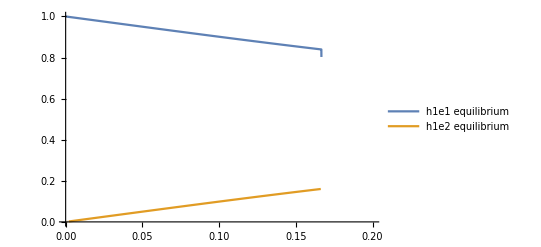

```mathematica
Plot[{ans[[10,1,2]],ans[[10,2,2]]},{d,0,0.2},PlotLegends->{"h1e1 equilibrium","h1e2 equilibrium"}]
```

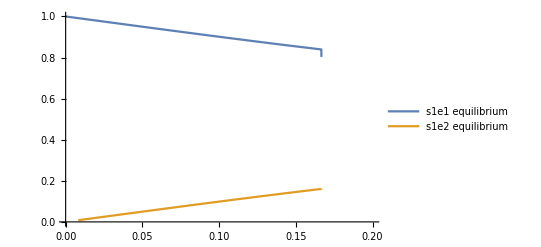

```mathematica
Plot[{ans[[10,3,2]],ans[[10,4,2]]},{d,0,0.2},PlotLegends->{"s1e1 equilibrium","s1e2 equilibrium"}]
```

Initially, this equilibrium looks real for low for small values of d:

```mathematica
ans[[10,1]]
```

h1e1→(-8-36 d+12 √3 √(d (4+d (-13+32 d)))+2 2^(1/3) (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)+2 ⅈ 2^(1/3) √3 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)-12 2^(1/3) d (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)-12 ⅈ 2^(1/3) √3 d (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)+2^(2/3) (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(4/3)-ⅈ 2^(2/3) √3 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(4/3))/(12 (-2-9 d+3 √3 √(d (4+d (-13+32 d)))))

There’s a polynomial that repeats throughout the expression:

```mathematica
Solve[√3 *Sqrt[d*(4-13*d+32*d^2)]==0,d]
```

{{d→0},{d→1/64 (13-7 ⅈ √7)},{d→1/64 (13+7 ⅈ √7)}}

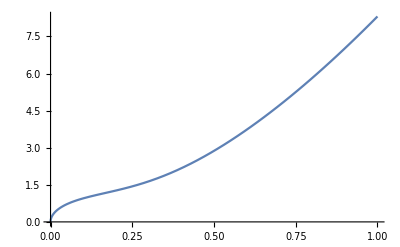

```mathematica
Plot[√3*Sqrt[d*(4-13*d+32*d^2)],{d,0,1}]
```

```mathematica
(*crosses at 0 but always positive*)
```

Simplify expression in terms of the solveable polynomial:

```mathematica
ans[[10,1]]/. √3 √(d (4+d (-13+32 d)))-> a//Expand
```

h1e1→-2/(3 (-2+3 a-9 d))+a/(-2+3 a-9 d)+1/(3 2^(2/3) (-2+3 a-9 d)^(1/3))+ⅈ/(2^(2/3) √3 (-2+3 a-9 d)^(1/3))+(-2+3 a-9 d)^(1/3)/(6 2^(1/3))-(ⅈ (-2+3 a-9 d)^(1/3))/(2 2^(1/3) √3)-(3 d)/(-2+3 a-9 d)-(2^(1/3) d)/(-2+3 a-9 d)^(1/3)-(ⅈ 2^(1/3) √3 d)/(-2+3 a-9 d)^(1/3)

Select imaginary terms to see if they ever go away:

```mathematica
Solve[ⅈ/(2^(2/3) √3 (-2+3 a-9 d)^(1/3))-(ⅈ (-2+3 a-9 d)^(1/3))/(2 2^(1/3) √3)-(ⅈ 2^(1/3) √3 d)/(-2+3 a-9 d)^(1/3)==0/.a-> √3 √(d (4+d (-13+32 d))),d]//Simplify
```

{{d→1/64 (13-7 ⅈ √7)},{d→1/64 (13+7 ⅈ √7)}}

```mathematica
N[{{d->1/64 (13-7 ⅈ √7)},{d->1/64 (13+7 ⅈ √7)}}]
```

{{d→0.203125-0.289379 ⅈ},{d→0.203125+0.289379 ⅈ}}

The polymorphic equilibrium always has an imaginary part, it’s just very small when d is close to 0.

```mathematica
ans[[10,1,2]]/.d-> 0//Simplify
```

Now I’ll try checking the stability of the real eigenvalues:

```mathematica
EigvalSelection[eq_,O_,min_,max_]:= Table[ {JC=J//assumptionfn;
eq[[i]],mat=Series[JC/.eq[[i]],{ϵ,0,O}]//Normal//Eigenvalues},{i,min,max}]
(*Function for approximating equilibria. Inputs are a matrix of equilibria, and specification of order with an integer. *)
stabilityfn = EigvalSelection[ans,1,1,5]/.d-> 0.1
```

{{{h1e1→0,h1e2→0,s1e1→0,s1e2→0},{-1.1099 ϵ,-1.1099 ϵ,-0.090098 ϵ,-0.090098 ϵ}},{{h1e1→1,h1e2→1,s1e1→0,s1e2→0},{-0.109902 ϵ,-0.109902 ϵ,0.909902 ϵ,0.909902 ϵ}},{{h1e1→0,h1e2→0,s1e1→1,s1e2→1},{-0.109902 ϵ,-0.109902 ϵ,0.909902 ϵ,0.909902 ϵ}},{{h1e1→1,h1e2→1,s1e1→1,s1e2→1},{-1.1099 ϵ,-1.1099 ϵ,-0.090098 ϵ,-0.090098 ϵ}},{{h1e1→-0.045804-0.312893 ⅈ,h1e2→1.0458-0.312893 ⅈ,s1e1→-0.045804-0.312893 ⅈ,s1e2→1.0458-0.312893 ⅈ},{-0.1 ϵ,0.091608 ϵ,(0.095804-0.704717 ⅈ) ϵ,(0.095804+0.704717 ⅈ) ϵ}}}

```mathematica
EigvalSelection[ans,1,10,10]/.d-> 0.1
```

$Aborted

## END CLEAN WORK. Begin the ugly stuff:

### Equilibria Approximations, small dispersal, only host g x e.

```mathematica
H1E1d/.symparams/.hostparamsnc//Simplify
```

-d h1e1+d h1e2+(-1+d) (-1+h1e1) h1e1 y (fθ fρ r (-1+s1e1)+fr (fρ-fρ s1e1) θ-fr fθ s1e1 ρ+r s1e1 θ ρ)

```mathematica
(*Assume that diffusion is very small, only small host g x e *)
{H1E1d,H1E2d,S1E1d,S1E2d}/.symparams/.hostparamsnc/.fr->r/.fρ->ρ//Factor;
Series[%,{d,0,1}]//Normal;
ans=Solve[%==0,{h1e1,h1e2,s1e1,s1e2}]//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{h1e1→0,h1e2→0,s1e2→s1e1},{h1e1→1,h1e2→1,s1e2→s1e1},{h1e1→-(2 d)/(-2 d+(-1+d) r y (fθ-θ) ρ+√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2)),h1e2→(2 d+(-1+d) r y (fθ-θ) ρ+√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2))/(2 (-1+d) r y (fθ-θ) ρ),s1e2→s1e1},{h1e1→(-2 d+(-1+d) r y (fθ-θ) ρ+√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2))/(2 (-1+d) r y (fθ-θ) ρ),h1e2→(2 d)/(2 d+(-1+d) r y (fθ-θ) ρ+√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2)),s1e2→s1e1}}

This makes sense. Any symbiont frequency is possible and there’s some intermediate host frequency.

```mathematica
myparams={θ->3,fθ-> 1, ρ-> 1,fρ-> 1,r-> 2,fr-> 1,y-> 0.5,d-> 0.05};
myparamsnd={θ->3,fθ-> 1, ρ-> 1,fρ-> 1,r-> 2,fr-> 1,y-> 0.5,d-> 0};
(*^ no dispersal version of paramerters^*)
ans[[3]]/.myparams
ans[[4]]/.myparams
```

{h1e1→-0.0270078,h1e2→1.02701,s1e2→s1e1}

{h1e1→0.974376,h1e2→0.0256237,s1e2→s1e1}

```mathematica
ans[[3]]/.myparamsnd
ans[[4]]/.myparamsnd
```

{h1e1→0.,h1e2→1.,s1e2→s1e1}

{h1e1→1.,h1e2→0.,s1e2→s1e1}

Without dispersal the internal equilbria change to boundary equilbiria which makes a lot of sense.

So it looks like equilibria 1, 2, and 4 are possible. Next, I’ll check out the stability of this equilibrium by applying my simplifying assumptions to my jacobian:

```mathematica
(*Note to self - add a taylor series expansion around d*)
JC=J/.hostparamsnc/.symparams/.fr->r/.fρ->ρ//Simplify
```

{{(-1+2 h1e1) r y (fθ-θ) ρ+d (-1+fθ (1-2 h1e1) r y ρ+(-1+2 h1e1) r y θ ρ),d,0,0},{d,-(-1+2 h1e2) r y (fθ-θ) ρ+d (-1+fθ (-1+2 h1e2) r y ρ+(1-2 h1e2) r y θ ρ),0,0},{0,0,-d,d},{0,0,d,-d}}

```mathematica
eigval1=JC/.ans[[4]]//Eigenvalues//FullSimplify
eigval1/.myparams
eigval1/.myparamsnd(*Not a bad approximation*)
```

{0,-2 d,(d^2 (-2+r y (fθ-θ) ρ (1+r y (-fθ+θ) ρ))+r y (fθ-θ) ρ (r y (-fθ+θ) ρ+√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2))+d (-√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2)+r y (fθ-θ) ρ (-1+2 r y (fθ-θ) ρ-√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2)))-√2 √(d^2 (d^2 (4+r y (fθ-θ) ρ (2+r y (fθ-θ) ρ))-r y (fθ-θ) ρ (r y (-fθ+θ) ρ+√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2))+d (2 √(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2)-r y (fθ-θ) ρ (2+2 r y (fθ-θ) ρ-√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2))))))/(2 d+(-1+d) r y (fθ-θ) ρ+√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2)),(d^2 (-2+r y (fθ-θ) ρ (1+r y (-fθ+θ) ρ))+r y (fθ-θ) ρ (r y (-fθ+θ) ρ+√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2))+d (-√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2)+r y (fθ-θ) ρ (-1+2 r y (fθ-θ) ρ-√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2)))+√2 √(d^2 (d^2 (4+r y (fθ-θ) ρ (2+r y (fθ-θ) ρ))-r y (fθ-θ) ρ (r y (-fθ+θ) ρ+√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2))+d (2 √(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2)-r y (fθ-θ) ρ (2+2 r y (fθ-θ) ρ-√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2))))))/(2 d+(-1+d) r y (fθ-θ) ρ+√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2))}

{0,-0.1,-1.90263,-1.80263}

{0,0,-2.,-2.}

Three stable, one neutral. This makes sense since symbiont frequency should change neutrally.

What can I tease out analytically. Let’s try applying the simplifying assumption that diffusion is extremely low:

```mathematica
eigval1[[3]]/.d-> 0//Simplify
%/.myparams
```

r y (fθ-θ) ρ

-2.

```mathematica
eigval1[[4]]/.d-> 0//Simplify
%/.myparams
```

r y (fθ-θ) ρ

-2.

Both of these eigenvalues will always be negative since fθ is always less than θ.

```mathematica
eigval1[[3]]
```

(d^2 (-2+r y (fθ-θ) ρ (1+r y (-fθ+θ) ρ))+r y (fθ-θ) ρ (r y (-fθ+θ) ρ+√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2))+d (-√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2)+r y (fθ-θ) ρ (-1+2 r y (fθ-θ) ρ-√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2)))-√2 √(d^2 (d^2 (4+r y (fθ-θ) ρ (2+r y (fθ-θ) ρ))-r y (fθ-θ) ρ (r y (-fθ+θ) ρ+√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2))+d (2 √(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2)-r y (fθ-θ) ρ (2+2 r y (fθ-θ) ρ-√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2))))))/(2 d+(-1+d) r y (fθ-θ) ρ+√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2))

I’ll try to not let dispersal go to 0 next.

```mathematica
(d^2 (-2+r y (fθ-θ) ρ (1+r y (-fθ+θ) ρ))+r y (fθ-θ) ρ (r y (-fθ+θ) ρ+√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2))+d (-√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2)+r y (fθ-θ) ρ (-1+2 r y (fθ-θ) ρ-√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2)))-√2 √(d^2 (d^2 (4+r y (fθ-θ) ρ (2+r y (fθ-θ) ρ))-r y (fθ-θ) ρ (r y (-fθ+θ) ρ+√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2))+d (2 √(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2)-r y (fθ-θ) ρ (2+2 r y (fθ-θ) ρ-√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2))))))/(2 d+(-1+d) r y (fθ-θ) ρ+√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2))
```

(d^2 (-2+r y (fθ-θ) ρ (1+r y (-fθ+θ) ρ))+r y (fθ-θ) ρ (r y (-fθ+θ) ρ+√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2))+d (-√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2)+r y (fθ-θ) ρ (-1+2 r y (fθ-θ) ρ-√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2)))-√2 √(d^2 (d^2 (4+r y (fθ-θ) ρ (2+r y (fθ-θ) ρ))-r y (fθ-θ) ρ (r y (-fθ+θ) ρ+√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2))+d (2 √(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2)-r y (fθ-θ) ρ (2+2 r y (fθ-θ) ρ-√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2))))))/(2 d+(-1+d) r y (fθ-θ) ρ+√(4 d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2))

I’ll also check out the boundary equilibria:

```mathematica
eigval2=JC/.ans[[1]]//Eigenvalues//FullSimplify
%/.myparams
```

{0,-2 d,-d-√(d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2),-d+√(d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2)}

{0,-0.1,-1.95066,1.85066}

```mathematica
eigval3=JC/.ans[[2]]//Eigenvalues//FullSimplify
%/.myparams
```

{0,-2 d,-d-√(d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2),-d+√(d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2)}

{0,-0.1,-1.95066,1.85066}

```mathematica
newparams={θ->1.1,fθ->1,ρ->1,fρ->1,r->1,fr->1,y->0.5,d-> 0.99}
```

{θ→1.1,fθ→1,ρ→1,fρ→1,r→1,fr→1,y→0.5,d→0.99}

```mathematica
eigval3/.newparams
```

{0,-1.98,-1.98,1.26263×10^-7}

So the final part of the boundary equilibria eigenvalue seems like it could go either way. Let’s try plotting it:

```mathematica
plotparams={θ->3,fθ->1,ρ->1,fρ->1,r->2,fr->1,y->0.5};
```

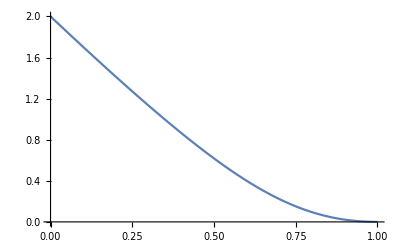

```mathematica
Plot[{-d+√(d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2)/.plotparams},{d,0,1}]
```

```mathematica
plotparams={θ->1.00001,fθ->1,ρ->1,fρ->1,r->1,fr->1,y->0.01};
```

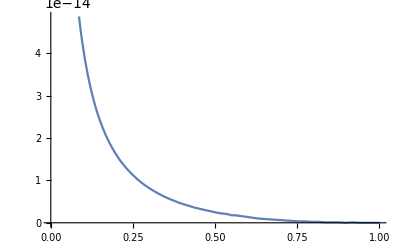

```mathematica
Plot[{-d+√(d^2+(-1+d)^2 r^2 y^2 (fθ-θ)^2 ρ^2)/.plotparams},{d,0,1}]
```

It can’t go either way because the negative part will always be less than the positive part regardless of the rest of the model parameters. As d approaches 1,  d ≃ d^2 so the eigenvalue will always be positive. And because we’re assuming small d in the first place, it’s inappropriate to look at higher values anyway.

### Same analysis, but now in terms of payoffs:

How do the relationships between payoffs change when there’s only host g x e?

```mathematica
{symparams,hostparamsnc}/.fr->r/.fρ->ρ
```

{{smatch→r (1-y) θ ρ,smismatchrθ→fθ r (1-y) ρ,smismatchρr→r (1-y) θ ρ,smismatchθρ→fθ r (1-y) ρ},{hmatch→r y θ ρ,himsmatchρr→r y θ ρ,hmismatchrθ→fθ r y ρ,hmismatchθρ→fθ r y ρ}}

So in terms of our payoffs: smatch = smismatchρr, smismatchrθ =  smismatchθρ, hmatch = himsmatchρr, and hmismatchrθ = hmismatchθρ. Let’s apply these to our expressions, except now the mismatches are really just in terms of a new theta:

```mathematica
(*Assume that diffusion is very small, only small host g x e *)
{H1E1d,H1E2d,S1E1d,S1E2d}/.{smismatchρr->smatch,smismatchrθ->smismatchθ,smismatchθρ-> smismatchθ,himsmatchρr->hmatch,hmismatchrθ->hmismatchθ,hmismatchθρ->hmismatchθ } //Factor;
Series[%,{d,0,1}]//Normal;
ansp=Solve[%==0,{h1e1,h1e2,s1e1,s1e2}]//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{h1e1→0,h1e2→0,s1e2→s1e1},{h1e1→1,h1e2→1,s1e2→s1e1},{h1e1→(2 d)/(-hmatch+d (2+hmatch-hmismatchθ)+hmismatchθ+√(-4 (-1+d) d (hmatch-hmismatchθ)+(-hmatch+d (2+hmatch-hmismatchθ)+hmismatchθ)^2)),h1e2→(-hmatch+√(d^2 (4+(hmatch-hmismatchθ)^2)+(hmatch-hmismatchθ)^2-2 d (hmatch-hmismatchθ)^2)+d (-2+hmatch-hmismatchθ)+hmismatchθ)/(2 (-1+d) (hmatch-hmismatchθ)),s1e2→s1e1},{h1e1→(-hmatch+d (2+hmatch-hmismatchθ)+hmismatchθ+√(-4 (-1+d) d (hmatch-hmismatchθ)+(-hmatch+d (2+hmatch-hmismatchθ)+hmismatchθ)^2))/(2 (-1+d) (hmatch-hmismatchθ)),h1e2→-((hmatch+√(d^2 (4+(hmatch-hmismatchθ)^2)+(hmatch-hmismatchθ)^2-2 d (hmatch-hmismatchθ)^2)-hmismatchθ+d (2-hmatch+hmismatchθ))/(2 (-1+d) (hmatch-hmismatchθ))),s1e2→s1e1}}

```mathematica
ansp[[3]]/.{hmatch->r y θ ρ,hmismatchθ->fθ r y ρ}/.myparams
```

{h1e1→0.974376,h1e2→0.0256237,s1e2→s1e1}

Same as the parameterized version.

```mathematica
JCp=J/.{smismatchρr->smatch,smismatchrθ->smismatchθ,smismatchθρ-> smismatchθ,himsmatchρr->hmatch,hmismatchrθ->hmismatchθ,hmismatchθρ->hmismatchθ } //Simplify
```

{{-(-1+2 h1e1) (hmatch-hmismatchθ)+d (-1+(-1+2 h1e1) hmatch+hmismatchθ-2 h1e1 hmismatchθ),d,0,0},{d,(-1+2 h1e2) (hmatch-hmismatchθ)+d (-1+hmatch-2 h1e2 hmatch-hmismatchθ+2 h1e2 hmismatchθ),0,0},{0,0,-d,d},{0,0,d,-d}}

The Jacobian looks similar.

```mathematica
eigvalp=JCp/.ansp[[3]]//Eigenvalues//FullSimplify
%/.{hmatch->r y θ ρ,hmismatchθ->fθ r y ρ}/.myparams
```

{0,-2 d,-((-(hmatch-hmismatchθ) (-hmatch+√(d^2 (4+(hmatch-hmismatchθ)^2)+(hmatch-hmismatchθ)^2-2 d (hmatch-hmismatchθ)^2)+hmismatchθ)+d^2 (2+(-1+hmatch) hmatch+hmismatchθ-2 hmatch hmismatchθ+hmismatchθ^2)+d (-2 hmatch^2+√(d^2 (4+(hmatch-hmismatchθ)^2)+(hmatch-hmismatchθ)^2-2 d (hmatch-hmismatchθ)^2)-hmismatchθ (1+√(d^2 (4+(hmatch-hmismatchθ)^2)+(hmatch-hmismatchθ)^2-2 d (hmatch-hmismatchθ)^2)+2 hmismatchθ)+hmatch (1+√(d^2 (4+(hmatch-hmismatchθ)^2)+(hmatch-hmismatchθ)^2-2 d (hmatch-hmismatchθ)^2)+4 hmismatchθ))+√2 √(d^2 (-(hmatch-hmismatchθ) (-hmatch+√(d^2 (4+(hmatch-hmismatchθ)^2)+(hmatch-hmismatchθ)^2-2 d (hmatch-hmismatchθ)^2)+hmismatchθ)+d (2 √(d^2 (4+(hmatch-hmismatchθ)^2)+(hmatch-hmismatchθ)^2-2 d (hmatch-hmismatchθ)^2)+hmatch √(d^2 (4+(hmatch-hmismatchθ)^2)+(hmatch-hmismatchθ)^2-2 d (hmatch-hmismatchθ)^2)-2 (hmatch-hmismatchθ) (1+hmatch-hmismatchθ)-√(d^2 (4+(hmatch-hmismatchθ)^2)+(hmatch-hmismatchθ)^2-2 d (hmatch-hmismatchθ)^2) hmismatchθ)+d^2 (4+2 hmatch+hmatch^2-2 (1+hmatch) hmismatchθ+hmismatchθ^2))))/(-hmatch+d (2+hmatch-hmismatchθ)+hmismatchθ+√(-4 (-1+d) d (hmatch-hmismatchθ)+(-hmatch+d (2+hmatch-hmismatchθ)+hmismatchθ)^2))),((hmatch-hmismatchθ) (-hmatch+√(d^2 (4+(hmatch-hmismatchθ)^2)+(hmatch-hmismatchθ)^2-2 d (hmatch-hmismatchθ)^2)+hmismatchθ)-d^2 (2+(-1+hmatch) hmatch+hmismatchθ-2 hmatch hmismatchθ+hmismatchθ^2)-d (-2 hmatch^2+√(d^2 (4+(hmatch-hmismatchθ)^2)+(hmatch-hmismatchθ)^2-2 d (hmatch-hmismatchθ)^2)-hmismatchθ (1+√(d^2 (4+(hmatch-hmismatchθ)^2)+(hmatch-hmismatchθ)^2-2 d (hmatch-hmismatchθ)^2)+2 hmismatchθ)+hmatch (1+√(d^2 (4+(hmatch-hmismatchθ)^2)+(hmatch-hmismatchθ)^2-2 d (hmatch-hmismatchθ)^2)+4 hmismatchθ))+√2 √(d^2 (-(hmatch-hmismatchθ) (-hmatch+√(d^2 (4+(hmatch-hmismatchθ)^2)+(hmatch-hmismatchθ)^2-2 d (hmatch-hmismatchθ)^2)+hmismatchθ)+d (2 √(d^2 (4+(hmatch-hmismatchθ)^2)+(hmatch-hmismatchθ)^2-2 d (hmatch-hmismatchθ)^2)+hmatch √(d^2 (4+(hmatch-hmismatchθ)^2)+(hmatch-hmismatchθ)^2-2 d (hmatch-hmismatchθ)^2)-2 (hmatch-hmismatchθ) (1+hmatch-hmismatchθ)-√(d^2 (4+(hmatch-hmismatchθ)^2)+(hmatch-hmismatchθ)^2-2 d (hmatch-hmismatchθ)^2) hmismatchθ)+d^2 (4+2 hmatch+hmatch^2-2 (1+hmatch) hmismatchθ+hmismatchθ^2))))/(-hmatch+d (2+hmatch-hmismatchθ)+hmismatchθ+√(-4 (-1+d) d (hmatch-hmismatchθ)+(-hmatch+d (2+hmatch-hmismatchθ)+hmismatchθ)^2))}

{0,-0.1,-1.90263,-1.80263}

Same eigenvalues when we translate into numerical parameters.

Let’s check the boundary equilibria:

```mathematica
eigvalp=JCp/.ansp[[1]]//Eigenvalues//FullSimplify
%/.{hmatch->r y θ ρ,hmismatchθ->fθ r y ρ}/.myparams
```

{0,-2 d,-d-√(d^2 (1+(hmatch-hmismatchθ)^2)+(hmatch-hmismatchθ)^2-2 d (hmatch-hmismatchθ)^2),-d+√(d^2 (1+(hmatch-hmismatchθ)^2)+(hmatch-hmismatchθ)^2-2 d (hmatch-hmismatchθ)^2)}

{0,-0.1,-1.95066,1.85066}

^Always unstable

```mathematica
eigvalp=JCp/.ansp[[2]]//Eigenvalues//FullSimplify
%/.{hmatch->r y θ ρ,hmismatchθ->fθ r y ρ}/.myparams
```

{0,-2 d,-d-√(d^2 (1+(hmatch-hmismatchθ)^2)+(hmatch-hmismatchθ)^2-2 d (hmatch-hmismatchθ)^2),-d+√(d^2 (1+(hmatch-hmismatchθ)^2)+(hmatch-hmismatchθ)^2-2 d (hmatch-hmismatchθ)^2)}

{0,-0.1,-1.95066,1.85066}

^ Also always unstable.

### Low dispersal, symbiont g x e only

```mathematica
(*Assume that diffusion is very small, only small symbiont g x e *)
{H1E1d,H1E2d,S1E1d,S1E2d}/.symparams/.hostparamsnc/.fθ-> θ/.fr->r//Factor;
Series[%,{d,0,1}]//Normal;
ans=Solve[%==0,{h1e1,h1e2,s1e1,s1e2}]//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{h1e2→h1e1,s1e1→0,s1e2→0},{h1e2→h1e1,s1e1→1,s1e2→1},{h1e2→h1e1,s1e1→(2 d-√((d (2+r (-1+y) θ (fρ-ρ))-r (-1+y) θ (fρ-ρ))^2-4 (-1+d) d r (-1+y) θ (fρ-ρ))+(-1+d) r (-1+y) θ (fρ-ρ))/(2 (-1+d) r (-1+y) θ (fρ-ρ)),s1e2→(-2 d+√((d (2+r (-1+y) θ (fρ-ρ))-r (-1+y) θ (fρ-ρ))^2-4 (-1+d) d r (-1+y) θ (fρ-ρ))+(-1+d) r (-1+y) θ (fρ-ρ))/(2 (-1+d) r (-1+y) θ (fρ-ρ))},{h1e2→h1e1,s1e1→(2 d+√((d (2+r (-1+y) θ (fρ-ρ))-r (-1+y) θ (fρ-ρ))^2-4 (-1+d) d r (-1+y) θ (fρ-ρ))+(-1+d) r (-1+y) θ (fρ-ρ))/(2 (-1+d) r (-1+y) θ (fρ-ρ)),s1e2→-((2 d+√((d (2+r (-1+y) θ (fρ-ρ))-r (-1+y) θ (fρ-ρ))^2-4 (-1+d) d r (-1+y) θ (fρ-ρ))-(-1+d) r (-1+y) θ (fρ-ρ))/(2 (-1+d) r (-1+y) θ (fρ-ρ)))}}

```mathematica
JC=J/.symparams/.hostparamsnc/.fθ-> θ/.fr->r //Simplify
```

{{-d,d,0,0},{d,-d,0,0},{0,0,-d+(-1+d) r (-1+s1e1) (-1+y) θ (fρ-ρ)+(-1+d) r s1e1 (-1+y) θ (fρ-ρ),d},{0,0,d,-d-(-1+d) r (-1+s1e2) (-1+y) θ (fρ-ρ)-(-1+d) r s1e2 (-1+y) θ (fρ-ρ)}}

```mathematica
sgxe={θ->1,fθ-> 1, ρ-> 3,fρ-> 1,r-> 2,fr-> 1,y-> 0.5,d-> 0.05};
```

```mathematica
eigvalsimplified=JC/.ans[[3]]//Eigenvalues//FullSimplify
%/.sgxe
```

{0,-2 d,d-√(d^2)-√((d (2+r (-1+y) θ (fρ-ρ))-r (-1+y) θ (fρ-ρ))^2-4 (-1+d) d r (-1+y) θ (fρ-ρ)),d+√(d^2)-√((d (2+r (-1+y) θ (fρ-ρ))-r (-1+y) θ (fρ-ρ))^2-4 (-1+d) d r (-1+y) θ (fρ-ρ))}

{0,-0.1,-1.90263,-1.80263}

^ The final three eigenvalues will always be negative when d is veeery small.

```mathematica
eigvalsimplified=JC/.ans[[1]]//Eigenvalues//FullSimplify
%/.sgxe
```

{0,-2 d,-d-√(d^2 (1+r^2 (-1+y)^2 θ^2 (fρ-ρ)^2)+r^2 (-1+y)^2 θ^2 (fρ-ρ)^2-2 d r^2 (-1+y)^2 θ^2 (fρ-ρ)^2),-d+√(d^2 (1+r^2 (-1+y)^2 θ^2 (fρ-ρ)^2)+r^2 (-1+y)^2 θ^2 (fρ-ρ)^2-2 d r^2 (-1+y)^2 θ^2 (fρ-ρ)^2)}

{0,-0.1,-1.95066,1.85066}

```mathematica
eigvalsimplified=JC/.ans[[2]]//Eigenvalues//FullSimplify
%/.sgxe
```

{0,-2 d,-d-√(d^2 (1+r^2 (-1+y)^2 θ^2 (fρ-ρ)^2)+r^2 (-1+y)^2 θ^2 (fρ-ρ)^2-2 d r^2 (-1+y)^2 θ^2 (fρ-ρ)^2),-d+√(d^2 (1+r^2 (-1+y)^2 θ^2 (fρ-ρ)^2)+r^2 (-1+y)^2 θ^2 (fρ-ρ)^2-2 d r^2 (-1+y)^2 θ^2 (fρ-ρ)^2)}

{0,-0.1,-1.95066,1.85066}

^The boundary equilibria will always be unstable with nonzero d.

### Low dispersal, symbiont g x e only, payoffs:

```mathematica
{symparams,hostparamsnc}/.fθ-> θ/.fr->r
```

{{smatch→r (1-y) θ ρ,smismatchrθ→r (1-y) θ ρ,smismatchρr→fρ r (1-y) θ,smismatchθρ→fρ r (1-y) θ},{hmatch→r y θ ρ,himsmatchρr→fρ r y θ,hmismatchrθ→r y θ ρ,hmismatchθρ→fρ r y θ}}

```mathematica
(*Assume that diffusion is very small, only small symbiont g x e *)
{H1E1d,H1E2d,S1E1d,S1E2d}/.{smismatchrθ-> smatch, smismatchρr-> smismatchρ,smismatchθρ-> smismatchρ,hmismatchrθ-> hmatch, hmismatchθρ-> hmismatchρ, hmismatchρr-> hmismatchρ}//Factor;
Series[%,{d,0,1}]//Normal;
ansp=Solve[%==0,{h1e1,h1e2,s1e1,s1e2}]//FullSimplify;
```

^Well that ends up big and ugly no matter how I simplify so I’d rather not deal with it for now.

### Perturbation Analysis:

```mathematica
(*Assume that diffusion is very small, very small symbiont g x e *)
{H1E1d,H1E2d,S1E1d,S1E2d}/.symparams/.hostparamsnc/.fθ-> θ/.fr->r/.d-> d*ϵ/.fρ-> ρ-ϵ//Factor;
Series[%,{ϵ,0,1}]//Normal;
ans=Solve[%==0,{h1e1,h1e2,s1e1,s1e2}]//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{h1e2→h1e1,s1e1→0,s1e2→0},{h1e2→h1e1,s1e1→1,s1e2→1},{h1e2→h1e1,s1e1→(2 d)/(2 d+r (-1+y) θ+√(4 d^2+r^2 (-1+y)^2 θ^2)),s1e2→(2 d)/(2 d+r (θ-y θ)+√(4 d^2+r^2 (-1+y)^2 θ^2))},{h1e2→h1e1,s1e1→(2 d)/(2 d+r (-1+y) θ-√(4 d^2+r^2 (-1+y)^2 θ^2)),s1e2→-(2 d)/(-2 d+r (-1+y) θ+√(4 d^2+r^2 (-1+y)^2 θ^2))}}

Now these look nice! The fourth equilibrium looks promising.

```mathematica
JC=J/.symparams/.hostparamsnc/.fθ-> θ/.fr->r /.d-> d*ϵ/.fρ-> ρ-ϵ//Simplify
```

{{-d ϵ,d ϵ,0,0},{d ϵ,-d ϵ,0,0},{0,0,-ϵ (d+r (-1-2 s1e1 (-1+y)+y) θ+d r (-1+2 s1e1) (-1+y) ϵ θ),d ϵ},{0,0,d ϵ,ϵ (r (-1-2 s1e2 (-1+y)+y) θ+d (-1+r (-1+2 s1e2) (-1+y) ϵ θ))}}

```mathematica
sgxe2={θ->1,fθ->1,ρ->1.25,fρ->1,r->2,fr->1,y->0.5,d->0.05,ϵ-> 0.1};
```

```mathematica
ans[[3]]/.sgxe2
```

{h1e2→h1e1,s1e1→0.952494,s1e2→0.0475062}

```mathematica
eigvals=JC/.ans[[3]]//Eigenvalues//Simplify
%/.sgxe2
```

{0,(r^2 (-1+y)^2 ϵ (-1+d ϵ) θ^2)/(2 d+√(4 d^2+r^2 (-1+y)^2 θ^2)),-(ϵ (4 d^2+r^2 (-1+y)^2 θ^2+d (-r^2 (-1+y)^2 ϵ θ^2+2 √(4 d^2+r^2 (-1+y)^2 θ^2))))/(2 d+√(4 d^2+r^2 (-1+y)^2 θ^2)),-2 d ϵ}

{0,-0.0900463,-0.100046,-0.01}

The last three eigenvalues will always be negative. The third eigenvalue will always be negative, since the only negative part of the numerator is doubly dependent on ϵ, which is very small.

### Perturbation Analysis, payoffs:

```mathematica
{symparams,hostparamsnc}/.fθ-> θ/.fr->r/.fρ-> ρ-ϵ
```

{{smatch→r (1-y) θ ρ,smismatchrθ→r (1-y) θ ρ,smismatchρr→r (1-y) θ (-ϵ+ρ),smismatchθρ→r (1-y) θ (-ϵ+ρ)},{hmatch→r y θ ρ,himsmatchρr→r y θ (-ϵ+ρ),hmismatchrθ→r y θ ρ,hmismatchθρ→r y θ (-ϵ+ρ)}}

```mathematica
(*Assume that diffusion is very small, only small symbiont g x e *)
{H1E1d,H1E2d,S1E1d,S1E2d}/.{smismatchrθ-> smatch, smismatchρr-> smatch-ϵ,smismatchθρ-> smatch-ϵ,hmismatchrθ-> hmatch, hmismatchθρ-> hmatch-ϵ, himsmatchρr-> hmatch-ϵ,d-> d*ϵ}//Factor;
Series[%,{ϵ,0,1}]//Normal
ansp=Solve[%==0,{h1e1,h1e2,s1e1,s1e2}]//FullSimplify
```

{-d (h1e1-h1e2) ϵ,d (h1e1-h1e2) ϵ,(s1e1-d s1e1-s1e1^2+d s1e2) ϵ,(d s1e1-s1e2-d s1e2+s1e2^2) ϵ}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{h1e2→h1e1,s1e1→0,s1e2→0},{h1e2→h1e1,s1e1→1,s1e2→1},{h1e2→h1e1,s1e1→1/2 (1-2 d-√(1+4 d^2)),s1e2→1/2 (1+2 d+√(1+4 d^2))},{h1e2→h1e1,s1e1→1/2 (1-2 d+√(1+4 d^2)),s1e2→1/2+d-1/2 √(1+4 d^2)}}

```mathematica
ansp/.hostparamsnc/.symparams/.sgxe2
```

{{h1e2→h1e1,s1e1→0,s1e2→0},{h1e2→h1e1,s1e1→1,s1e2→1},{h1e2→h1e1,s1e1→-0.0524938,s1e2→1.05249},{h1e2→h1e1,s1e1→0.952494,s1e2→0.0475062}}

```mathematica
JC=J/.{smismatchrθ-> smatch, smismatchρr-> smatch-ϵ,smismatchθρ-> smatch-ϵ,hmismatchrθ-> hmatch, hmismatchθρ-> hmatch-ϵ, himsmatchρr-> hmatch-ϵ,d-> d*ϵ}//Simplify
```

{{-d ϵ,d ϵ,0,0},{d ϵ,-d ϵ,0,0},{0,0,ϵ (1-2 s1e1+d (-1+(-1+2 s1e1) ϵ)),d ϵ},{0,0,d ϵ,-ϵ (1+d-2 s1e2+d (-1+2 s1e2) ϵ)}}

```mathematica
eigvals=JC/.ansp[[4]]//Eigenvalues//Simplify
%/.sgxe2
```

{0,-2 d ϵ,-ϵ (√(d^2)+√(1+4 d^2)+2 d^2 ϵ-d (1+√(1+4 d^2) ϵ)),ϵ (d+√(d^2)-√(1+4 d^2)-2 d^2 ϵ+d √(1+4 d^2) ϵ)}

{0,-0.01,-0.100046,-0.0900463}

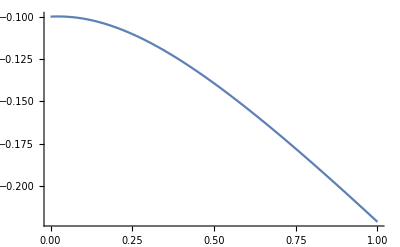

```mathematica
Plot[{-ϵ (√(d^2)+√(1+4 d^2)+2 d^2 ϵ-d (1+√(1+4 d^2) ϵ))/.ϵ-> 0.1},{d,0,1}]
```

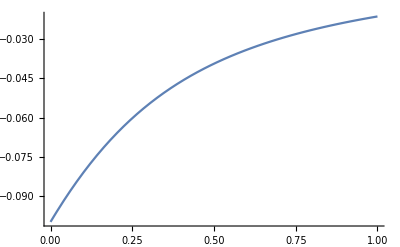

```mathematica
Plot[{ϵ (d+√(d^2)-√(1+4 d^2)-2 d^2 ϵ+d √(1+4 d^2) ϵ)/.ϵ-> 0.1},{d,0,1}]
```

```mathematica
{symparams,hostparamsnc}/.fθ-> θ-ϵ/.fr->r-ϵ/.fρ-> ρ-ϵ
```

{{smatch→r (1-y) θ ρ,smismatchrθ→(1-y) (r-ϵ) (-ϵ+θ) ρ,smismatchρr→(1-y) (r-ϵ) θ (-ϵ+ρ),smismatchθρ→r (1-y) (-ϵ+θ) (-ϵ+ρ)},{hmatch→r y θ ρ,himsmatchρr→y (r-ϵ) θ (-ϵ+ρ),hmismatchrθ→y (r-ϵ) (-ϵ+θ) ρ,hmismatchθρ→r y (-ϵ+θ) (-ϵ+ρ)}}

### 5/19/23 Everything small:

There is a veeery small difference between matching and mismatching, diffusion is low:

```mathematica
{H1E1d,H1E2d,S1E1d,S1E2d}/.{smismatchrθ-> smatch-ϵ, smismatchρr-> smatch-ϵ,smismatchθρ-> smatch-ϵ,hmismatchrθ-> hmatch-ϵ, hmismatchθρ-> hmatch-ϵ, himsmatchρr-> hmatch-ϵ,d->d*ϵ}//Factor;
Series[%,{ϵ,0,1}]//Normal;
ans=Solve[%==0,{h1e1,h1e2,s1e1,s1e2}]//FullSimplify
ans/.d-> 0.1
```

{{h1e1→0,h1e2→0,s1e1→0,s1e2→0},{h1e1→1,h1e2→1,s1e1→0,s1e2→0},{h1e1→0,h1e2→0,s1e1→1,s1e2→1},{h1e1→1,h1e2→1,s1e1→1,s1e2→1},{h1e1→1/4 (1-√(1+4 d)-√2 √(1-6 d-√(1+4 d))),h1e2→1/4 (3+√(1+4 d)-√2 √(1-6 d-√(1+4 d))),s1e1→1/4 (1-√(1+4 d)-√2 √(1-6 d-√(1+4 d))),s1e2→1/4 (3+√(1+4 d)-√2 √(1-6 d-√(1+4 d)))},{h1e1→1/4 (1-√(1+4 d)+√2 √(1-6 d-√(1+4 d))),h1e2→1/4 (3+√(1+4 d)+√2 √(1-6 d-√(1+4 d))),s1e1→1/4 (1-√(1+4 d)+√2 √(1-6 d-√(1+4 d))),s1e2→1/4 (3+√(1+4 d)+√2 √(1-6 d-√(1+4 d)))},{h1e1→1/4 (1+√(1+4 d)-√2 √(1-6 d+√(1+4 d))),h1e2→1/4 (3-√(1+4 d)-√2 √(1-6 d+√(1+4 d))),s1e1→1/4 (1+√(1+4 d)-√2 √(1-6 d+√(1+4 d))),s1e2→1/4 (3-√(1+4 d)-√2 √(1-6 d+√(1+4 d)))},{h1e1→1/4 (1+√(1+4 d)+√2 √(1-6 d+√(1+4 d))),h1e2→1/4 (3-√(1+4 d)+√2 √(1-6 d+√(1+4 d))),s1e1→1/4 (1+√(1+4 d)+√2 √(1-6 d+√(1+4 d))),s1e2→1/4 (3-√(1+4 d)+√2 √(1-6 d+√(1+4 d)))},{h1e1→(-2 2^(1/3)+12 2^(1/3) d+2 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3)-(-4-18 d+6 √3 √(d (4+d (-13+32 d))))^(2/3))/(6 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3)),h1e2→(2 2^(1/3)-12 2^(1/3) d+4 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3)+(-4-18 d+6 √3 √(d (4+d (-13+32 d))))^(2/3))/(6 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3)),s1e1→(-2 2^(1/3)+12 2^(1/3) d+2 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3)-(-4-18 d+6 √3 √(d (4+d (-13+32 d))))^(2/3))/(6 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3)),s1e2→1/6 (4+(2 2^(1/3) (1-6 d))/(-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3)+2^(2/3) (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3))},{h1e1→(-8-36 d+12 √3 √(d (4+d (-13+32 d)))+2 2^(1/3) (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)+2 ⅈ 2^(1/3) √3 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)-12 2^(1/3) d (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)-12 ⅈ 2^(1/3) √3 d (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)+2^(2/3) (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(4/3)-ⅈ 2^(2/3) √3 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(4/3))/(12 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))),h1e2→(-4 (-2)^(1/3)+24 (-2)^(1/3) d+8 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3)-(-4-18 d+6 √3 √(d (4+d (-13+32 d))))^(2/3)+ⅈ √3 (-4-18 d+6 √3 √(d (4+d (-13+32 d))))^(2/3))/(12 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3)),s1e1→(-8-36 d+12 √3 √(d (4+d (-13+32 d)))+2 2^(1/3) (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)+2 ⅈ 2^(1/3) √3 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)-12 2^(1/3) d (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)-12 ⅈ 2^(1/3) √3 d (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)+2^(2/3) (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(4/3)-ⅈ 2^(2/3) √3 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(4/3))/(12 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))),s1e2→1/12 (8+(4 (-2)^(1/3) (-1+6 d))/(-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3)+2 (-2)^(2/3) (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3))},{h1e1→(-8-36 d+12 √3 √(d (4+d (-13+32 d)))+2 2^(1/3) (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)-12 2^(1/3) d (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)+12 ⅈ 2^(1/3) √3 d (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)+2^(2/3) (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(4/3)+ⅈ 2^(2/3) √3 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(4/3)+(-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3) Root-4.36 ⅈRoot[6912+#1^6&,3]0.)/(12 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))),h1e2→(8 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3)-(-4-18 d+6 √3 √(d (4+d (-13+32 d))))^(2/3)-ⅈ √3 (-4-18 d+6 √3 √(d (4+d (-13+32 d))))^(2/3)+Root-2.52+4.36 ⅈRoot[-128+#1^3&,3]-2.5198420997897464+d Root15.1-26.2 ⅈRoot[27648+#1^3&,2]15.119052598738477)/(12 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3)),s1e1→(-8-36 d+12 √3 √(d (4+d (-13+32 d)))+2 2^(1/3) (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)-12 2^(1/3) d (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)+12 ⅈ 2^(1/3) √3 d (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)+2^(2/3) (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(4/3)+ⅈ 2^(2/3) √3 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(4/3)+(-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3) Root-4.36 ⅈRoot[6912+#1^6&,3]0.)/(12 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))),s1e2→2/3+((-1)^(2/3) 2^(1/3) (1-6 d))/(3 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3))-1/3 (-1/2)^(1/3) (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(1/3)}}

{{h1e1→0,h1e2→0,s1e1→0,s1e2→0},{h1e1→1,h1e2→1,s1e1→0,s1e2→0},{h1e1→0,h1e2→0,s1e1→1,s1e2→1},{h1e1→1,h1e2→1,s1e1→1,s1e2→1},{h1e1→-0.045804-0.312893 ⅈ,h1e2→1.0458-0.312893 ⅈ,s1e1→-0.045804-0.312893 ⅈ,s1e2→1.0458-0.312893 ⅈ},{h1e1→-0.045804+0.312893 ⅈ,h1e2→1.0458+0.312893 ⅈ,s1e1→-0.045804+0.312893 ⅈ,s1e2→1.0458+0.312893 ⅈ},{h1e1→0.100942,h1e2→0.00933424,s1e1→0.100942,s1e2→0.00933424},{h1e1→0.990666,h1e2→0.899058,s1e1→0.990666,s1e2→0.899058},{h1e1→0.0493991+0.329428 ⅈ,h1e2→0.950601-0.329428 ⅈ,s1e1→0.0493991+0.329428 ⅈ,s1e2→0.950601-0.329428 ⅈ},{h1e1→0.901202-9.75023×10^-17 ⅈ,h1e2→0.0987981+1.38778×10^-17 ⅈ,s1e1→0.901202-9.75023×10^-17 ⅈ,s1e2→0.0987981+3.70074×10^-17 ⅈ},{h1e1→0.0493991-0.329428 ⅈ,h1e2→0.950601+0.329428 ⅈ,s1e1→0.0493991-0.329428 ⅈ,s1e2→0.950601+0.329428 ⅈ}}

Only the first 5 equilibria can be real.

Coexistent equilibrium does not exist for large d:

```mathematica
ans[[10]]/.d-> 0.1//Simplify
```

{h1e1→0.901202-9.75023×10^-17 ⅈ,h1e2→0.0987981+1.38778×10^-17 ⅈ,s1e1→0.901202-9.75023×10^-17 ⅈ,s1e2→0.0987981+3.70074×10^-17 ⅈ}

```mathematica
ans[[10]]/.d-> 0.1//Chop
```

{h1e1→0.901202,h1e2→0.0987981,s1e1→0.901202,s1e2→0.0987981}

```mathematica
Plot[{ans[[10,1,2]],ans[[10,2,2]]},{d,0,0.2},PlotLegends->{"h1e1 equilibrium","h1e2 equilibrium"}]
```

-Graphics-

```mathematica
Plot[{ans[[10,3,2]],ans[[10,4,2]]},{d,0,0.2},PlotLegends->{"s1e1 equilibrium","s1e2 equilibrium"}]
```

-Graphics-

Initially, this equilibrium looks real for low for small values of d:

```mathematica
ans[[10,1]]
```

h1e1→(-8-36 d+12 √3 √(d (4+d (-13+32 d)))+2 2^(1/3) (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)+2 ⅈ 2^(1/3) √3 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)-12 2^(1/3) d (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)-12 ⅈ 2^(1/3) √3 d (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(2/3)+2^(2/3) (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(4/3)-ⅈ 2^(2/3) √3 (-2-9 d+3 √3 √(d (4+d (-13+32 d))))^(4/3))/(12 (-2-9 d+3 √3 √(d (4+d (-13+32 d)))))

There’s a polynomial that repeats throughout the expression:

```mathematica
Solve[√3 *Sqrt[d*(4-13*d+32*d^2)]==0,d]
```

{{d→0},{d→1/64 (13-7 ⅈ √7)},{d→1/64 (13+7 ⅈ √7)}}

```mathematica
Plot[√3*Sqrt[d*(4-13*d+32*d^2)],{d,0,1}]
```

-Graphics-

```mathematica
(*crosses at 0 but always positive*)
```

Simplify expression in terms of the solveable polynomial:

```mathematica
ans[[10,1]]/. √3 √(d (4+d (-13+32 d)))-> a//Expand
```

h1e1→-2/(3 (-2+3 a-9 d))+a/(-2+3 a-9 d)+1/(3 2^(2/3) (-2+3 a-9 d)^(1/3))+ⅈ/(2^(2/3) √3 (-2+3 a-9 d)^(1/3))+(-2+3 a-9 d)^(1/3)/(6 2^(1/3))-(ⅈ (-2+3 a-9 d)^(1/3))/(2 2^(1/3) √3)-(3 d)/(-2+3 a-9 d)-(2^(1/3) d)/(-2+3 a-9 d)^(1/3)-(ⅈ 2^(1/3) √3 d)/(-2+3 a-9 d)^(1/3)

Select imaginary terms to see if they ever go away:

```mathematica
Solve[ⅈ/(2^(2/3) √3 (-2+3 a-9 d)^(1/3))-(ⅈ (-2+3 a-9 d)^(1/3))/(2 2^(1/3) √3)-(ⅈ 2^(1/3) √3 d)/(-2+3 a-9 d)^(1/3)==0/.a-> √3 √(d (4+d (-13+32 d))),d]//Simplify
```

{{d→1/64 (13-7 ⅈ √7)},{d→1/64 (13+7 ⅈ √7)}}

```mathematica
N[{{d->1/64 (13-7 ⅈ √7)},{d->1/64 (13+7 ⅈ √7)}}]
```

{{d→0.203125-0.289379 ⅈ},{d→0.203125+0.289379 ⅈ}}

The polymorphic equilibrium always has an imaginary part, it’s just very small when d is close to 0.

```mathematica
ans[[10,1,2]]/.d-> 0//Simplify
```

1

Now let’s do our stability analysis:

```mathematica
JC=J/.{smismatchrθ-> smatch-ϵ, smismatchρr-> smatch-ϵ,smismatchθρ-> smatch-ϵ,hmismatchrθ-> hmatch-ϵ, hmismatchθρ-> hmatch-ϵ, himsmatchρr-> hmatch-ϵ,d-> d*ϵ}//Simplify
```

{{ϵ (s1e1-2 h1e1 s1e1+d (-1+(-1+2 h1e1) s1e1 ϵ)),d ϵ,(-1+s1e1) s1e1 ϵ (-1+d ϵ),0},{d ϵ,ϵ (-1-2 h1e2 (-1+s1e2)+s1e2+d (-1+(-1+2 h1e2) (-1+s1e2) ϵ)),0,(-1+s1e2) s1e2 ϵ (-1+d ϵ)},{(-1+h1e1) h1e1 ϵ (-1+d ϵ),0,ϵ (h1e1-2 h1e1 s1e1+d (-1+h1e1 (-1+2 s1e1) ϵ)),d ϵ},{0,(-1+h1e2) h1e2 ϵ (-1+d ϵ),d ϵ,ϵ (-1+h1e2+2 s1e2-2 h1e2 s1e2+d (-1+(-1+h1e2) (-1+2 s1e2) ϵ))}}

```mathematica
Eigvalfxn[min_,max_]:= Table[ {ans[[i]],JC/.ans[[i]]//Eigenvalues//Simplify},{i,min,max}](*Function that access items min through max of ans and returns their value and their eigenvalue*)
```

```mathematica
RealStabilityTable = Eigvalfxn[1,4]
```

{{{h1e1→0,h1e2→0,s1e1→0,s1e2→0},{1/2 ϵ (-1+d (-2+ϵ)-√(1-2 d ϵ+d^2 (4+ϵ^2))),1/2 ϵ (-1+d (-2+ϵ)-√(1-2 d ϵ+d^2 (4+ϵ^2))),1/2 ϵ (-1+d (-2+ϵ)+√(1-2 d ϵ+d^2 (4+ϵ^2))),1/2 ϵ (-1+d (-2+ϵ)+√(1-2 d ϵ+d^2 (4+ϵ^2)))}},{{h1e1→1,h1e2→1,s1e1→0,s1e2→0},{-1/2 ϵ (-1+d (2+ϵ)+√(1-2 d ϵ+d^2 (4+ϵ^2))),-1/2 ϵ (-1+d (2+ϵ)+√(1-2 d ϵ+d^2 (4+ϵ^2))),1/2 ϵ (1-d (2+ϵ)+√(1-2 d ϵ+d^2 (4+ϵ^2))),1/2 ϵ (1-d (2+ϵ)+√(1-2 d ϵ+d^2 (4+ϵ^2)))}},{{h1e1→0,h1e2→0,s1e1→1,s1e2→1},{-1/2 ϵ (-1+d (2+ϵ)+√(1-2 d ϵ+d^2 (4+ϵ^2))),-1/2 ϵ (-1+d (2+ϵ)+√(1-2 d ϵ+d^2 (4+ϵ^2))),1/2 ϵ (1-d (2+ϵ)+√(1-2 d ϵ+d^2 (4+ϵ^2))),1/2 ϵ (1-d (2+ϵ)+√(1-2 d ϵ+d^2 (4+ϵ^2)))}},{{h1e1→1,h1e2→1,s1e1→1,s1e2→1},{1/2 ϵ (-1+d (-2+ϵ)-√(1-2 d ϵ+d^2 (4+ϵ^2))),1/2 ϵ (-1+d (-2+ϵ)-√(1-2 d ϵ+d^2 (4+ϵ^2))),1/2 ϵ (-1+d (-2+ϵ)+√(1-2 d ϵ+d^2 (4+ϵ^2))),1/2 ϵ (-1+d (-2+ϵ)+√(1-2 d ϵ+d^2 (4+ϵ^2)))}}}

```mathematica
RealStabilityTable/.d-> 0.1/.ϵ-> 0.1//Simplify
```

{{{h1e1→0,h1e2→0,s1e1→0,s1e2→0},{-0.11,-0.11,-0.009,-0.009}},{{h1e1→1,h1e2→1,s1e1→0,s1e2→0},{-0.011,-0.011,0.09,0.09}},{{h1e1→0,h1e2→0,s1e1→1,s1e2→1},{-0.011,-0.011,0.09,0.09}},{{h1e1→1,h1e2→1,s1e1→1,s1e2→1},{-0.11,-0.11,-0.009,-0.009}}}

So it looks like the system is bistable. All of these eigenvalues are comprised of the exact same terms but signs vary.

```mathematica
RealStabilityTable[[1]](*Same as the otehr fixed equilibrium*)
```

{{h1e1→0,h1e2→0,s1e1→0,s1e2→0},{1/2 ϵ (-1+d (-2+ϵ)-√(1-2 d ϵ+d^2 (4+ϵ^2))),1/2 ϵ (-1+d (-2+ϵ)-√(1-2 d ϵ+d^2 (4+ϵ^2))),1/2 ϵ (-1+d (-2+ϵ)+√(1-2 d ϵ+d^2 (4+ϵ^2))),1/2 ϵ (-1+d (-2+ϵ)+√(1-2 d ϵ+d^2 (4+ϵ^2)))}}

All eigenvalues negative since -1 <<( d ~ ϵ)

```mathematica
RealStabilityTable[[3]](*Same as the other mismatched equilibrium*)
```

{{h1e1→0,h1e2→0,s1e1→1,s1e2→1},{-1/2 ϵ (-1+d (2+ϵ)+√(1-2 d ϵ+d^2 (4+ϵ^2))),-1/2 ϵ (-1+d (2+ϵ)+√(1-2 d ϵ+d^2 (4+ϵ^2))),1/2 ϵ (1-d (2+ϵ)+√(1-2 d ϵ+d^2 (4+ϵ^2))),1/2 ϵ (1-d (2+ϵ)+√(1-2 d ϵ+d^2 (4+ϵ^2)))}}

Third and fourth eigenvalues always positive since d and e are << 1.

The next real equilibria are 7 and 8.

```mathematica
Eigvalfxn[7,8]/.{d-> 0.1,ϵ-> 0.1}
```

{{{h1e1→0.100942,h1e2→0.00933424,s1e1→0.100942,s1e2→0.00933424},{-0.108189,-0.106213,-0.00997973,0.00784393}},{{h1e1→0.990666,h1e2→0.899058,s1e1→0.990666,s1e2→0.899058},{-0.108189,-0.106213,-0.00997973,0.00784393}}}

So it looks like the fourth eigenvalue can be unstable. When unpacking the expressions for the stability criterion they’re the same.

Let’s check to see if the fourth eigenvalue can ever be negative:

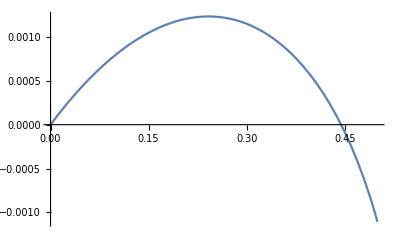

```mathematica
Plot[mostlyfixed[[2,2,4]]/.ϵ-> 0.01,{d ,0,0.5}]
```

Dispersal would have to be too big so these equilibria are always unstable.

```mathematica
ans[[1]]
```

{h1e1→0,h1e2→0,s1e1→0,s1e2→0}

```mathematica
JC/.ans[[10]]/.ϵ-> 0.01/.d-> 0.01//Eigenvalues//Simplify
```

{-0.01-2.75801×10^-17 ⅈ,-0.00980208-5.48812×10^-17 ⅈ,-0.00980004-2.75801×10^-17 ⅈ,-0.00960208-5.48812×10^-17 ⅈ}

### Other perturbation analysis

```mathematica
{H1E1d,H1E2d,S1E1d,S1E2d}/.{smismatchrθ-> smatch-ϵ, smismatchρr-> smatch-ϵ,smismatchθρ-> smatch-ϵ,hmismatchrθ-> hmatch-ϵ, hmismatchθρ-> hmatch-ϵ, himsmatchρr-> hmatch-ϵ,d-> ϵ}//Factor;
Series[%,{ϵ,0,1}]//Normal;
ans=Solve[%==0,{h1e1,h1e2,s1e1,s1e2},Reals]//FullSimplify//N
```

{{h1e1→0.,h1e2→0.,s1e1→0.,s1e2→0.},{h1e1→0.,h1e2→0.,s1e1→1.,s1e2→1.},{h1e1→1.,h1e2→1.,s1e1→0.,s1e2→0.},{h1e1→1.,h1e2→1.,s1e1→1.,s1e2→1.},{h1e1→0.56984,h1e2→0.43016,s1e1→0.56984,s1e2→0.43016}}

```mathematica
JC=J/.{smismatchrθ-> smatch-ϵ, smismatchρr-> smatch-ϵ,smismatchθρ-> smatch-ϵ,hmismatchrθ-> hmatch-ϵ, hmismatchθρ-> hmatch-ϵ, himsmatchρr-> hmatch-ϵ,d-> ϵ}//Simplify;
```

```mathematica
ApproxEigvalfxn[eq_]:= Table[ {ans[[i]],mat=JC/.ans[[i]]//Eigenvalues//Simplify},{i,1,Length[eq]}]
mostlyfixed = ApproxEigvalfxn[ans]/.ϵ-> 0.01/.h1e1-> 0.5/.s1e1-> 0.25//Simplify
```

{{{h1e2→0.5,s1e2→0.25},{-0.0180221,-0.00197795,-0.0222866,0.00228661}}}

Small g x g and diffusion

```mathematica
{H1E1d,H1E2d,S1E1d,S1E2d}/.hostparamsnc/.symparams/.{fθ-> fθ*ϵ,θ-> θ*ϵ,fρ-> fρ*ϵ,ρ-> ρ*ϵ ,r-> r*ϵ,fr-> fr*ϵ,d-> d*ϵ}//Factor;
Series[%,{ϵ,0,1}]//Normal;
ans=Solve[%==0,{h1e1,h1e2,s1e1,s1e2}]//FullSimplify
ApproxEigvalfxn[ans]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{h1e2→h1e1,s1e2→s1e1}}

{{{h1e2→h1e1,s1e2→s1e1},{1/2 ϵ (-3+2 h1e1+2 s1e1-4 h1e1 s1e1+ϵ-2 h1e1 ϵ-2 s1e1 ϵ+4 h1e1 s1e1 ϵ-√((-3-2 s1e1 (-1+ϵ)+2 h1e1 (-1+2 s1e1) (-1+ϵ)+ϵ)^2-2 (-1+ϵ) (-2+5 h1e1-h1e1^2+5 s1e1-14 h1e1 s1e1+6 h1e1^2 s1e1-s1e1^2+6 h1e1 s1e1^2-6 h1e1^2 s1e1^2-h1e1 ϵ+h1e1^2 ϵ-s1e1 ϵ+6 h1e1 s1e1 ϵ-6 h1e1^2 s1e1 ϵ+s1e1^2 ϵ-6 h1e1 s1e1^2 ϵ+6 h1e1^2 s1e1^2 ϵ-√(h1e1^4 (1-2 s1e1)^2 (-1+ϵ)^2+(-1+s1e1)^2 s1e1^2 (-1+ϵ)^2+2 h1e1^3 (-1+6 s1e1-10 s1e1^2+4 s1e1^3) (-1+ϵ)^2-2 h1e1 (-1+s1e1) s1e1 (9-4 s1e1 (-1+ϵ)^2+2 s1e1^2 (-1+ϵ)^2-2 ϵ+ϵ^2)+h1e1^2 ((-1+ϵ)^2-20 s1e1^3 (-1+ϵ)^2+4 s1e1^4 (-1+ϵ)^2-2 s1e1 (13-10 ϵ+5 ϵ^2)+s1e1^2 (42-52 ϵ+26 ϵ^2)))))),1/2 ϵ (-3+2 h1e1+2 s1e1-4 h1e1 s1e1+ϵ-2 h1e1 ϵ-2 s1e1 ϵ+4 h1e1 s1e1 ϵ+√((-3-2 s1e1 (-1+ϵ)+2 h1e1 (-1+2 s1e1) (-1+ϵ)+ϵ)^2-2 (-1+ϵ) (-2+5 h1e1-h1e1^2+5 s1e1-14 h1e1 s1e1+6 h1e1^2 s1e1-s1e1^2+6 h1e1 s1e1^2-6 h1e1^2 s1e1^2-h1e1 ϵ+h1e1^2 ϵ-s1e1 ϵ+6 h1e1 s1e1 ϵ-6 h1e1^2 s1e1 ϵ+s1e1^2 ϵ-6 h1e1 s1e1^2 ϵ+6 h1e1^2 s1e1^2 ϵ-√(h1e1^4 (1-2 s1e1)^2 (-1+ϵ)^2+(-1+s1e1)^2 s1e1^2 (-1+ϵ)^2+2 h1e1^3 (-1+6 s1e1-10 s1e1^2+4 s1e1^3) (-1+ϵ)^2-2 h1e1 (-1+s1e1) s1e1 (9-4 s1e1 (-1+ϵ)^2+2 s1e1^2 (-1+ϵ)^2-2 ϵ+ϵ^2)+h1e1^2 ((-1+ϵ)^2-20 s1e1^3 (-1+ϵ)^2+4 s1e1^4 (-1+ϵ)^2-2 s1e1 (13-10 ϵ+5 ϵ^2)+s1e1^2 (42-52 ϵ+26 ϵ^2)))))),1/2 ϵ (-3+2 h1e1+2 s1e1-4 h1e1 s1e1+ϵ-2 h1e1 ϵ-2 s1e1 ϵ+4 h1e1 s1e1 ϵ-√((-3-2 s1e1 (-1+ϵ)+2 h1e1 (-1+2 s1e1) (-1+ϵ)+ϵ)^2-2 (-1+ϵ) (-2+5 h1e1-h1e1^2+5 s1e1-14 h1e1 s1e1+6 h1e1^2 s1e1-s1e1^2+6 h1e1 s1e1^2-6 h1e1^2 s1e1^2-h1e1 ϵ+h1e1^2 ϵ-s1e1 ϵ+6 h1e1 s1e1 ϵ-6 h1e1^2 s1e1 ϵ+s1e1^2 ϵ-6 h1e1 s1e1^2 ϵ+6 h1e1^2 s1e1^2 ϵ+√(h1e1^4 (1-2 s1e1)^2 (-1+ϵ)^2+(-1+s1e1)^2 s1e1^2 (-1+ϵ)^2+2 h1e1^3 (-1+6 s1e1-10 s1e1^2+4 s1e1^3) (-1+ϵ)^2-2 h1e1 (-1+s1e1) s1e1 (9-4 s1e1 (-1+ϵ)^2+2 s1e1^2 (-1+ϵ)^2-2 ϵ+ϵ^2)+h1e1^2 ((-1+ϵ)^2-20 s1e1^3 (-1+ϵ)^2+4 s1e1^4 (-1+ϵ)^2-2 s1e1 (13-10 ϵ+5 ϵ^2)+s1e1^2 (42-52 ϵ+26 ϵ^2)))))),1/2 ϵ (-3+2 h1e1+2 s1e1-4 h1e1 s1e1+ϵ-2 h1e1 ϵ-2 s1e1 ϵ+4 h1e1 s1e1 ϵ+√((-3-2 s1e1 (-1+ϵ)+2 h1e1 (-1+2 s1e1) (-1+ϵ)+ϵ)^2-2 (-1+ϵ) (-2+5 h1e1-h1e1^2+5 s1e1-14 h1e1 s1e1+6 h1e1^2 s1e1-s1e1^2+6 h1e1 s1e1^2-6 h1e1^2 s1e1^2-h1e1 ϵ+h1e1^2 ϵ-s1e1 ϵ+6 h1e1 s1e1 ϵ-6 h1e1^2 s1e1 ϵ+s1e1^2 ϵ-6 h1e1 s1e1^2 ϵ+6 h1e1^2 s1e1^2 ϵ+√(h1e1^4 (1-2 s1e1)^2 (-1+ϵ)^2+(-1+s1e1)^2 s1e1^2 (-1+ϵ)^2+2 h1e1^3 (-1+6 s1e1-10 s1e1^2+4 s1e1^3) (-1+ϵ)^2-2 h1e1 (-1+s1e1) s1e1 (9-4 s1e1 (-1+ϵ)^2+2 s1e1^2 (-1+ϵ)^2-2 ϵ+ϵ^2)+h1e1^2 ((-1+ϵ)^2-20 s1e1^3 (-1+ϵ)^2+4 s1e1^4 (-1+ϵ)^2-2 s1e1 (13-10 ϵ+5 ϵ^2)+s1e1^2 (42-52 ϵ+26 ϵ^2))))))}}}

```mathematica
{H1E1d,H1E2d,S1E1d,S1E2d}/.symparams/.hostparamsnc/.fθ-> θ/.fρ-> ρ/.fr->r-ϵ/.d->d* ϵ//Factor;
Series[%,{ϵ,0,1}]//Normal
ans=Solve[%==0,{h1e1,h1e2,s1e1,s1e2}]//FullSimplify
```

{ϵ (-d h1e1+d h1e2-h1e1 y θ ρ+h1e1^2 y θ ρ+2 h1e1 s1e1 y θ ρ-2 h1e1^2 s1e1 y θ ρ),ϵ (d h1e1-d h1e2-h1e2 y θ ρ+h1e2^2 y θ ρ+2 h1e2 s1e2 y θ ρ-2 h1e2^2 s1e2 y θ ρ),ϵ (-d s1e1+d s1e2-s1e1 θ ρ+2 h1e1 s1e1 θ ρ+s1e1^2 θ ρ-2 h1e1 s1e1^2 θ ρ+s1e1 y θ ρ-2 h1e1 s1e1 y θ ρ-s1e1^2 y θ ρ+2 h1e1 s1e1^2 y θ ρ),ϵ (d s1e1-d s1e2-s1e2 θ ρ+2 h1e2 s1e2 θ ρ+s1e2^2 θ ρ-2 h1e2 s1e2^2 θ ρ+s1e2 y θ ρ-2 h1e2 s1e2 y θ ρ-s1e2^2 y θ ρ+2 h1e2 s1e2^2 y θ ρ)}

$Aborted

```mathematica
JC=J/.{smismatchrθ-> smatch-ϵ, smismatchρr-> smatch-ϵ,smismatchθρ-> smatch,hmismatchrθ-> hmatch-ϵ, hmismatchθρ-> hmatch, himsmatchρr-> hmatch-ϵ,d-> d*ϵ}//Simplify
```

{{ϵ (-1+h1e1 (2-4 s1e1)+2 s1e1+d (-1+(-1+2 h1e1) (-1+2 s1e1) ϵ)),d ϵ,2 (-1+s1e1) s1e1 ϵ (-1+d ϵ),0},{d ϵ,ϵ (-1+h1e2 (2-4 s1e2)+2 s1e2+d (-1+(-1+2 h1e2) (-1+2 s1e2) ϵ)),0,2 (-1+s1e2) s1e2 ϵ (-1+d ϵ)},{2 (-1+h1e1) h1e1 ϵ (-1+d ϵ),0,ϵ (-1+h1e1 (2-4 s1e1)+2 s1e1+d (-1+(-1+2 h1e1) (-1+2 s1e1) ϵ)),d ϵ},{0,2 (-1+h1e2) h1e2 ϵ (-1+d ϵ),d ϵ,ϵ (-1+h1e2 (2-4 s1e2)+2 s1e2+d (-1+(-1+2 h1e2) (-1+2 s1e2) ϵ))}}

### Equilibrium where g x e dictates ecological dynamics: (1,1,0,0)

```mathematica
J/.Matchparams/.{h1e1-> 1,s1e1-> 1,h1e2-> 0,s1e2-> 0}//MatrixForm
UL=%[[1;;2,1;;2]](*Upper Left Diagonal Matrix*)
LR = %%[[3;;4,3;;4]](*Lower Right Diagonal Matrix*)
```

(-d-HM+Hρ | d | 0 | 0
d | -d-HM+Hρ | 0 | 0
0 | 0 | -d-SM+Sθ | d
0 | 0 | d | -d-SM+Sθ)

{{-d-HM+Hρ,d},{d,-d-HM+Hρ}}

{{-d-SM+Sθ,d},{d,-d-SM+Sθ}}

Now for the upper left matrix:

```mathematica
CharacteristicPolynomial[UL,r];
Collect[%,r];
CoefficientList[%,r];
a1=%[[2]]
a2=%%[[1]]/.Matchparams;
Collect[%,d]//Simplify
```

2 d+2 HM-2 Hρ

(HM-Hρ) (2 d+HM-Hρ)

This will always be stable since HM > Hρ.

```mathematica
CharacteristicPolynomial[LR,r];
Collect[%,r];
CoefficientList[%,r];
a1=%[[2]]//Simplify
a2=%%[[1]]/.Matchparams;
Collect[%,d]//Simplify
```

2 (d+SM-Sθ)

(SM-Sθ) (2 d+SM-Sθ)

This will also always be positive since SM > Sθ.